# Alg AG4

```mathematica
getSol[chromosome_]:=
Module[{chromosomes=chromosome},
curLimits={α,β};
currentX=Table[0,muchii];
currentSol=0;
Do[
parents=SparseArray[chromosomes⟦2,source⟧[[All,2]]->chromosomes⟦2,source⟧[[All,1]]];
curFlow=Table[0,noduri];
Do[
minVal=Min[{curLimits⟦1,source⟧,curLimits⟦2,dest⟧}];
curFlow⟦noduri-n+dest⟧+=minVal;
curLimits⟦1,source⟧-=minVal;
curLimits⟦2,dest⟧-=minVal;
,{dest,chromosomes⟦4⟧}];

DepthFirstScan[chromosomes⟦2,source⟧,source,"PostvisitVertex"->(
If[#≠source,
edgeId=pos⟦parents⟦#⟧*noduri+#⟧;
curFlow⟦parents⟦#⟧⟧+=curFlow⟦#⟧;
currentX⟦edgeId⟧+=curFlow⟦#⟧;
]&)];
,{source,chromosomes⟦3⟧}];
currentX
]
```

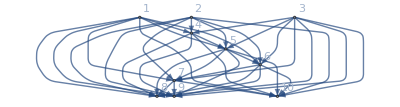

{1->4,1->5,1->6,1->7,1->8,1->9,1->10,2->4,2->5,2->6,2->7,2->8,2->9,2->10,3->4,3->5,3->6,3->7,3->8,3->9,3->10,4->5,4->8,4->9,4->10,5->6,5->7,5->8,5->9,5->10,6->7,6->8,6->9,6->10,7->8,7->9,7->10}

37

SparseArray[…]

{{0},{0},{0},{1,2,3},{1,2,3,4},{1,2,3,5},{1,2,3,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7}}

{15,23,12}

{10,37,3}

{2,1,2,1,2,1,2,2,2,1,2,2,2,2,2,1,2,2,1,2,1,2,1,1,1,1,1,1,2,1,1,2,2,1,2,2,2}

```mathematica
m=3;
n=3;
H=50;
(*Crearea unui graf cu m surse, n destinatii si noduri-m-n noduri intermediare*)
(*In acest graft exista drum din fiecare sursa in fiecare destinatie*)
noduri=10;
g= Graph[
Table[i,{i,noduri}],
DeleteDuplicates@Flatten[Table[
Join[
{source->m+1},
Table[source->j,{j,RandomSample[Range[m+2,noduri]]}],
Flatten[Table[i->j,{i,m+1,noduri-n-1},{j,RandomSample[Range[i+2,noduri-n],RandomInteger[noduri-i-n-1]]}]],
Table[i->i+1,{i,m+1,noduri-1-n}],
Flatten[Table[i->j,{j,noduri-n+1,noduri},{i,RandomSample[Range[m+1,noduri-n],RandomInteger[{1,noduri-n-m}]]}]]
],{source,m}]],
VertexLabels->Automatic
]
val=Sort[EdgeList[g]] (*care arce sunt in graf*)
muchii=EdgeCount[g] (*numarul de arce*)

M=muchii;
pos = SparseArray[MapIndexed[#⟦1⟧*noduri+#⟦2⟧->#2⟦1⟧&,val]] (*Se creaza un hastable pentru a accesa pozitia unei muchii*)

(*Lista nodurilor parinti pentru fiecare nod*)
adjList=Join[Table[{0},m],Sort[Gather[val,#1[[2]]==#2[[2]]&],#1[[1,2]]<#2[[1,2]]&][[All,All,1]]]



α=Differences[Flatten[{0,Sort[RandomSample[Range[H-1],m-1]],H}]]
β=Differences[Flatten[{0,Sort[RandomSample[Range[H-1],n-1]],H}]]


(*Se creaza functiile concave de cost*)
foo=Table[RandomInteger[Range[1,2]],M]
bar=foo;
f[j_,x_]:=Piecewise[{{foo⟦j⟧ x, x≤bar⟦j⟧}, {foo⟦j⟧ bar⟦j⟧, x>bar⟦j⟧}, {0, True}}]
```

```mathematica
Do[
Print[Style["Test ","Section"],Style[bigCount,"Section"]];
thisTimer=Timing[
(*Variabile necesare pentru algoritm*)
nrIteratii=10;

(*Se afla nodurile in care se poate ajunge din sursa i*)
subtrees=Table[VertexList@FindSpanningTree[{g,i}],{i,m}];

Print["------------------------------------------------------------------"];
Print["Virfurile ce pot fi atinse din fiecare sursa  ",subtrees];
(*Se creaza populatia intiala. Fiecare cromozom va fi format din {valoarea functiei, arborii din fiecare sursa, ordinea surselor, ordinea destinatiilor, ordinea transporturilor, ordinea produselor}*)
Print["------------------------------------------------------------------"];
Print["Populatia initiala"];
chromosomes=Table[
{
0,
Table[Table[RandomChoice[Intersection[adjList⟦i⟧,subtrees⟦j⟧]]->i,{i,Drop[subtrees⟦j⟧,1]}],{j,m}],
RandomSample[Range[m]],
RandomSample[Range[n]]
}
,4*noduri];
Print[chromosomes];
(*Se gaseste solutiile asociate fiecarui cromozom si functiile lor obiectiv*)
Do[
(*Maximul de flux care poate fi trimis din fiecare sursa, destinatie, transport, produs*)
curLimits={α,β};
(*Solutia cromozomului i*)
currentX=Table[0,muchii];
currentSol=0;
(*Fiecare arbore este evaluat aparte*)
Do[
(*Arborele este reprezentat ca un hashmap dintre nodul copil si nodul parinte*)
parents=SparseArray[chromosomes⟦i,2,source⟧[[All,2]]->chromosomes⟦i,2,source⟧[[All,1]]];
(*Se calculeaza fluxul care trebuie impins din destinatii catre sursa*)
curFlow=Table[0,noduri];
Do[
(*Se afla marimea fluxului care poate fi impins din source catre dest cu produsul k si transportul l*)
minVal=Min[{curLimits⟦1,source⟧,curLimits⟦2,dest⟧}];
curFlow⟦noduri-n+dest⟧+=minVal;
curLimits⟦1,source⟧-=minVal;
curLimits⟦2,dest⟧-=minVal;
,{dest,chromosomes⟦i,4⟧}];
(*Printr-un depth first search se impinge fluxul din destinatii catre sursa*)
DepthFirstScan[chromosomes⟦i,2,source⟧,source,"PostvisitVertex"->(
If[#≠source,
(*Se afla pozitia muchiei*)
edgeId=pos⟦parents⟦#⟧*noduri+#⟧;
(*Tot fluxul din nodul curent este impins catre parinte si solutia acestui cromozom este actualizata*)
curFlow⟦parents⟦#⟧⟧+=curFlow⟦#⟧;
currentX⟦edgeId⟧+=curFlow⟦#⟧;
]&)];
,{source,chromosomes⟦i,3⟧}];
(*Se afla valoarea funtiei obiectiv*)
chromosomes⟦i,1⟧=Sum[f[j,currentX⟦j⟧],{j,muchii}];
,{i,4*noduri}];
chromosomes=Sort[chromosomes];


Do[
Print["------------------------------------------------------------------"];
Print["Iteratia ",iteratia];
(*Sunt alesi cei mai buni parinti*)

chromosomes=Take[chromosomes,2*noduri];

(*Se creaza urmasii si urmatoarea populatie*)
chromosomes=Join[
(*Parintii nu sunt schimbati*)
chromosomes,

Print["Parintii si Urmasii"];
Flatten[Table[
(*Urmasii sunt creati prin impartirea aleatoarea a arborilor din cromozomii-parinti*)
(*Celelalte valori sunt luate de la ambii parinti*)

randPos=RandomInteger[{1,m-1}];
{
{0,Join[chromosomes⟦i,2,;;randPos⟧,chromosomes⟦i+1,2,randPos+1;;⟧],chromosomes⟦i,3⟧,chromosomes⟦i+1,4⟧},
{0,Join[chromosomes⟦i+1,2,;;randPos⟧,chromosomes⟦i,2,randPos+1;;⟧],chromosomes⟦i+1,3⟧,chromosomes⟦i,4⟧}
}
,{i,1,2*noduri,2}],1]];
(*Pentru fiecare lista de ordini din fiecare cromozom-copil mutatia se produce cu sansa de 50%*)
Do[
If[RandomInteger[100]≤50,
(*Doua pozitii sunt alese aleator si schimbate cu locurile*)
{it1,it2}=RandomSample[Range[Length@chromosomes⟦i⟧⟦j⟧],2];
chromosomes⟦i⟧⟦j⟧⟦{it1,it2}⟧=chromosomes⟦i⟧⟦j⟧⟦{it2,it1}⟧
];
,{i,2*noduri+1,4*noduri},{j,3,4}];
Print[chromosomes];
(*Se evalueaza cromozomii-copii*)
Do[
curLimits={α,β};
currentX=Table[0,muchii];
currentSol=0;
Do[
parents=SparseArray[chromosomes⟦i,2,source⟧[[All,2]]->chromosomes⟦i,2,source⟧[[All,1]]];
curFlow=Table[0,noduri];
Do[
minVal=Min[{curLimits⟦1,source⟧,curLimits⟦2,dest⟧}];
curFlow⟦noduri-n+dest⟧+=minVal;
curLimits⟦1,source⟧-=minVal;
curLimits⟦2,dest⟧-=minVal;
,{dest,chromosomes⟦i,4⟧}];
DepthFirstScan[chromosomes⟦i,2,source⟧,source,"PostvisitVertex"->(
If[#≠source,
edgeId=pos⟦parents⟦#⟧*noduri+#⟧;
curFlow⟦parents⟦#⟧⟧+=curFlow⟦#⟧;
currentX⟦edgeId⟧+=curFlow⟦#⟧;
]&)];
,{source,chromosomes⟦i,3⟧}];
chromosomes⟦i,1⟧=Sum[f[j,currentX⟦j⟧],{j,muchii}];
,{i,2*noduri+1,4*noduri}];

Print["Populatia noua "];
chromosomes=Sort[chromosomes];

Print[chromosomes];
Print["Cromozom cu cele mai bune caracteristici ",chromosomes⟦1⟧];
Print["Solutia cea mai buna ",getSol[chromosomes⟦1⟧]];
Print["Funtia obiectiv totala  ",Total@chromosomes⟦All,1⟧];
,{iteratia,nrIteratii}];];
Print[thisTimer];
,{bigCount,10}]
```

Test 1

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,5->6,5->7,1->8,6->9,6->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,6->9,5->10},{3->4,4->5,5->6,5->7,7->8,6->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,5->6,6->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,7->10},{2->4,4->5,5->6,2->7,5->8,7->9,4->10},{3->4,3->5,5->6,3->7,7->8,6->9,7->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,4->9,2->10},{3->4,4->5,5->6,5->7,4->8,6->9,7->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,1->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,6->8,5->9,5->10},{2->4,2->5,2->6,5->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,4->8,4->9,6->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,1->8,7->9,6->10},{2->4,4->5,2->6,2->7,4->8,5->9,7->10},{3->4,4->5,3->6,3->7,6->8,6->9,7->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,5->6,1->7,7->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,7->9,4->10},{3->4,4->5,5->6,5->7,5->8,6->9,7->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,5->6,6->7,4->8,7->9,1->10},{2->4,2->5,5->6,2->7,6->8,4->9,6->10},{3->4,4->5,5->6,3->7,3->8,6->9,3->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,6->8,1->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,6->7,6->8,7->9,3->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,4->10},{2->4,2->5,5->6,6->7,7->8,2->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,4->9,7->10},{2->4,2->5,2->6,5->7,7->8,5->9,4->10},{3->4,4->5,3->6,3->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,5->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,6->9,6->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,5->8,7->9,7->10},{2->4,2->5,5->6,6->7,5->8,2->9,2->10},{3->4,4->5,5->6,5->7,6->8,3->9,7->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,1->8,5->9,5->10},{2->4,2->5,2->6,2->7,5->8,7->9,6->10},{3->4,4->5,3->6,3->7,7->8,4->9,3->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,5->8,6->9,4->10},{2->4,4->5,5->6,5->7,2->8,5->9,6->10},{3->4,3->5,5->6,5->7,5->8,6->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,7->8,1->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,6->9,2->10},{3->4,4->5,3->6,5->7,6->8,4->9,6->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,4->8,6->9,1->10},{2->4,4->5,2->6,6->7,2->8,5->9,2->10},{3->4,3->5,5->6,3->7,4->8,4->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,4->8,7->9,4->10},{3->4,4->5,3->6,3->7,3->8,6->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,6->9,7->10},{2->4,2->5,2->6,2->7,5->8,7->9,5->10},{3->4,4->5,3->6,5->7,7->8,4->9,6->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,7->8,5->9,6->10},{2->4,2->5,5->6,2->7,6->8,5->9,6->10},{3->4,3->5,3->6,3->7,5->8,4->9,7->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,5->8,6->9,4->10},{2->4,4->5,5->6,5->7,2->8,7->9,5->10},{3->4,3->5,5->6,6->7,4->8,7->9,4->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,1->8,7->9,1->10},{2->4,4->5,5->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,6->8,3->9,4->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,7->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,7->9,4->10},{3->4,4->5,5->6,6->7,7->8,6->9,4->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,2->8,7->9,2->10},{3->4,4->5,5->6,5->7,5->8,5->9,4->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,7->8,7->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,5->9,7->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10},{2->4,2->5,2->6,2->7,6->8,2->9,4->10},{3->4,4->5,3->6,5->7,5->8,6->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,2->8,5->9,4->10},{3->4,3->5,5->6,6->7,6->8,6->9,7->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,6->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,3->5,3->6,6->7,7->8,7->9,7->10}},{2,3,1},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,4->8,7->9,6->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,4->8,4->9,5->10},{2->4,4->5,5->6,5->7,6->8,7->9,4->10},{3->4,4->5,3->6,6->7,7->8,5->9,5->10}},{2,1,3},{1,3,2}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,1,3}},{18,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,1,2},{1,3,2}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{3,1,2},{3,2,1}},{20,{{1->4,1->5,5->6,5->7,1->8,6->9,6->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{22,{{1->4,1->5,5->6,1->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,7->10}},{2,3,1},{2,3,1}},{24,{{1->4,1->5,5->6,1->7,5->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,6->9,6->10}},{2,3,1},{2,3,1}},{24,{{1->4,1->5,5->6,5->7,6->8,5->9,5->10},{2->4,2->5,2->6,5->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,4->8,4->9,6->10}},{1,3,2},{1,2,3}},{24,{{1->4,4->5,5->6,6->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,3,2},{1,3,2}},{25,{{1->4,1->5,5->6,6->7,6->8,5->9,4->10},{2->4,2->5,5->6,6->7,7->8,2->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,3->10}},{3,1,2},{2,3,1}},{25,{{1->4,4->5,5->6,5->7,7->8,1->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{26,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,6->9,5->10},{3->4,4->5,5->6,5->7,7->8,6->9,5->10}},{3,2,1},{1,3,2}},{26,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,4->8,7->9,6->10}},{1,2,3},{1,2,3}},{27,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,4->9,2->10},{3->4,4->5,5->6,5->7,4->8,6->9,7->10}},{3,2,1},{1,2,3}},{27,{{1->4,4->5,1->6,5->7,5->8,6->9,4->10},{2->4,4->5,5->6,5->7,2->8,5->9,6->10},{3->4,3->5,5->6,5->7,5->8,6->9,6->10}},{2,1,3},{1,2,3}},{28,{{1->4,1->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,6->9,2->10},{3->4,4->5,3->6,5->7,6->8,4->9,6->10}},{1,2,3},{1,3,2}},{28,{{1->4,1->5,5->6,1->7,1->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{3,2,1}},{28,{{1->4,1->5,5->6,5->7,4->8,4->9,7->10},{2->4,2->5,2->6,5->7,7->8,5->9,4->10},{3->4,4->5,3->6,3->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,1->8,6->9,6->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,3->7,5->8,4->9,7->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,5->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,4->8,4->9,6->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,6->9,6->10}},{2,3,1},{3,2,1}},{0,{{1->4,4->5,5->6,6->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,3->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,4->10},{2->4,2->5,5->6,6->7,7->8,2->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,7->8,1->9,1->10},{2->4,2->5,2->6,2->7,4->8,6->9,5->10},{3->4,4->5,5->6,5->7,7->8,6->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,4->8,6->9,7->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,4->9,2->10},{3->4,3->5,3->6,3->7,4->8,7->9,6->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,5->8,6->9,4->10},{2->4,4->5,5->6,2->7,2->8,6->9,2->10},{3->4,4->5,3->6,5->7,6->8,4->9,6->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,5->9,6->10},{3->4,3->5,5->6,5->7,5->8,6->9,6->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,1->8,4->9,5->10},{2->4,2->5,2->6,5->7,7->8,5->9,4->10},{3->4,4->5,3->6,3->7,5->8,7->9,6->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,4->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,5->6,3->7,5->8,7->9,3->10}},{2,3,1},{1,2,3}}}

Populatia noua

{{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,1,3}},{18,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,1,2},{1,3,2}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{1,2,3},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,1->8,6->9,6->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{1,3,2},{1,2,3}},{21,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,4->9,2->10},{3->4,3->5,3->6,3->7,4->8,7->9,6->10}},{1,2,3},{2,1,3}},{21,{{1->4,1->5,5->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,5->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,4->8,4->9,6->10}},{2,3,1},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{22,{{1->4,1->5,5->6,1->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,7->10}},{2,3,1},{2,3,1}},{22,{{1->4,1->5,5->6,1->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{2,3,1},{3,2,1}},{22,{{1->4,4->5,5->6,5->7,7->8,1->9,1->10},{2->4,2->5,2->6,2->7,4->8,6->9,5->10},{3->4,4->5,5->6,5->7,7->8,6->9,5->10}},{3,1,2},{1,3,2}},{22,{{1->4,4->5,5->6,6->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,3->10}},{3,1,2},{2,1,3}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,4->10},{2->4,2->5,5->6,6->7,7->8,2->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,3,2},{1,3,2}},{24,{{1->4,1->5,5->6,1->7,5->8,6->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,6->9,6->10}},{2,3,1},{2,3,1}},{24,{{1->4,1->5,5->6,5->7,6->8,5->9,5->10},{2->4,2->5,2->6,5->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,4->8,4->9,6->10}},{1,3,2},{1,2,3}},{24,{{1->4,4->5,5->6,6->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,3,2},{1,3,2}},{25,{{1->4,1->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,5->6,5->7,2->8,5->9,6->10},{3->4,3->5,5->6,5->7,5->8,6->9,6->10}},{3,2,1},{1,2,3}},{25,{{1->4,1->5,5->6,6->7,6->8,5->9,4->10},{2->4,2->5,5->6,6->7,7->8,2->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,3->10}},{3,1,2},{2,3,1}},{25,{{1->4,4->5,5->6,5->7,7->8,1->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{26,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,6->9,5->10},{3->4,4->5,5->6,5->7,7->8,6->9,5->10}},{3,2,1},{1,3,2}},{26,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,4->8,7->9,6->10}},{1,2,3},{1,2,3}},{27,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,4->9,2->10},{3->4,4->5,5->6,5->7,4->8,6->9,7->10}},{3,2,1},{1,2,3}},{27,{{1->4,1->5,5->6,5->7,4->8,4->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,5->6,3->7,5->8,7->9,3->10}},{2,3,1},{1,2,3}},{27,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{3,1,2},{2,1,3}},{27,{{1->4,4->5,1->6,5->7,5->8,6->9,4->10},{2->4,4->5,5->6,5->7,2->8,5->9,6->10},{3->4,3->5,5->6,5->7,5->8,6->9,6->10}},{2,1,3},{1,2,3}},{28,{{1->4,1->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,6->9,2->10},{3->4,4->5,3->6,5->7,6->8,4->9,6->10}},{1,2,3},{1,3,2}},{28,{{1->4,1->5,5->6,1->7,1->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{3,2,1}},{28,{{1->4,1->5,5->6,5->7,1->8,6->9,6->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,3->7,5->8,4->9,7->10}},{2,1,3},{1,3,2}},{28,{{1->4,1->5,5->6,5->7,4->8,4->9,7->10},{2->4,2->5,2->6,5->7,7->8,5->9,4->10},{3->4,4->5,3->6,3->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{28,{{1->4,4->5,1->6,5->7,5->8,6->9,4->10},{2->4,4->5,5->6,2->7,2->8,6->9,2->10},{3->4,4->5,3->6,5->7,6->8,4->9,6->10}},{1,2,3},{1,3,2}},{31,{{1->4,1->5,5->6,1->7,1->8,4->9,5->10},{2->4,2->5,2->6,5->7,7->8,5->9,4->10},{3->4,4->5,3->6,3->7,5->8,7->9,6->10}},{2,1,3},{3,1,2}},{31,{{1->4,1->5,5->6,5->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,6->10},{3->4,4->5,5->6,3->7,5->8,6->9,6->10}},{2,3,1},{3,2,1}},{31,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,4->8,6->9,7->10}},{1,2,3},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,23,0,0,0,0,10,0,0,0,0,0,2,0,10,0,0,0,0,0,0,0,0,0,22,1,0,0,0}

Funtia obiectiv totala  926

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,1,3}},{18,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,1,2},{1,3,2}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{1,2,3},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,1->8,6->9,6->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{1,3,2},{1,2,3}},{21,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,4->9,2->10},{3->4,3->5,3->6,3->7,4->8,7->9,6->10}},{1,2,3},{2,1,3}},{21,{{1->4,1->5,5->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,5->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,4->8,4->9,6->10}},{2,3,1},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{22,{{1->4,1->5,5->6,1->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,7->10}},{2,3,1},{2,3,1}},{22,{{1->4,1->5,5->6,1->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{2,3,1},{3,2,1}},{22,{{1->4,4->5,5->6,5->7,7->8,1->9,1->10},{2->4,2->5,2->6,2->7,4->8,6->9,5->10},{3->4,4->5,5->6,5->7,7->8,6->9,5->10}},{3,1,2},{1,3,2}},{22,{{1->4,4->5,5->6,6->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,3->10}},{3,1,2},{2,1,3}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,4->10},{2->4,2->5,5->6,6->7,7->8,2->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{3,2,1},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,1->8,6->9,6->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,2->5,2->6,5->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,4->8,4->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,5->8,6->9,4->10},{2->4,2->5,5->6,5->7,2->8,4->9,2->10},{3->4,3->5,3->6,3->7,4->8,7->9,6->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,7->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,5->7,7->8,6->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,7->8,1->9,1->10},{2->4,2->5,2->6,2->7,4->8,6->9,5->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,5->6,6->7,6->8,4->9,4->10},{2->4,2->5,5->6,6->7,7->8,2->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,3->10}},{3,1,2},{2,1,3}}}

Populatia noua

{{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,1,3}},{18,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,1,2},{1,3,2}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2}},{18,{{1->4,4->5,5->6,6->7,6->8,4->9,4->10},{2->4,2->5,5->6,6->7,7->8,2->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,7->10}},{1,2,3},{2,3,1}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{1,2,3},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,1->8,6->9,6->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{2,3,1},{3,2,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{1,3,2},{1,2,3}},{21,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,4->9,2->10},{3->4,3->5,3->6,3->7,4->8,7->9,6->10}},{1,2,3},{2,1,3}},{21,{{1->4,1->5,5->6,1->7,5->8,6->9,4->10},{2->4,2->5,2->6,5->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,4->8,4->9,6->10}},{2,3,1},{3,2,1}},{21,{{1->4,1->5,5->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{2,3,1},{2,3,1}},{21,{{1->4,1->5,5->6,5->7,1->8,6->9,6->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{3,1,2},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{21,{{1->4,4->5,5->6,5->7,7->8,1->9,1->10},{2->4,2->5,2->6,2->7,4->8,6->9,5->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{2,3,1}},{22,{{1->4,1->5,5->6,1->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,7->10}},{2,3,1},{2,3,1}},{22,{{1->4,1->5,5->6,1->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{2,3,1},{3,2,1}},{22,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{3,2,1},{2,1,3}},{22,{{1->4,4->5,5->6,5->7,7->8,1->9,1->10},{2->4,2->5,2->6,2->7,4->8,6->9,5->10},{3->4,4->5,5->6,5->7,7->8,6->9,5->10}},{3,1,2},{1,3,2}},{22,{{1->4,4->5,5->6,6->7,6->8,4->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,3->10}},{3,1,2},{2,1,3}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,3->10}},{3,1,2},{2,1,3}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,4->10},{2->4,2->5,5->6,6->7,7->8,2->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,3,2},{1,3,2}},{24,{{1->4,1->5,5->6,1->7,6->8,1->9,4->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,5->6,5->7,7->8,6->9,5->10}},{2,1,3},{1,3,2}},{25,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{1,2,3},{1,3,2}},{26,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,2->5,2->6,5->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,4->8,4->9,6->10}},{3,2,1},{3,2,1}},{27,{{1->4,1->5,5->6,1->7,5->8,6->9,4->10},{2->4,2->5,5->6,5->7,2->8,4->9,2->10},{3->4,3->5,3->6,3->7,4->8,7->9,6->10}},{1,3,2},{2,1,3}},{29,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,3,0,0,9,0,0,0,1,22,0,0,0,0,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  789

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,1,3}},{18,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,1,2},{1,3,2}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2}},{18,{{1->4,4->5,5->6,6->7,6->8,4->9,4->10},{2->4,2->5,5->6,6->7,7->8,2->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,7->10}},{1,2,3},{2,3,1}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{1,2,3},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,1->8,6->9,6->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,5->6,6->7,6->8,4->9,4->10},{2->4,2->5,5->6,6->7,7->8,2->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,3->7,5->8,4->9,7->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,1->8,6->9,6->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{2,1,3}}}

Populatia noua

{{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,3,2},{1,2,3}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,1,3}},{18,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{2,1,3},{2,1,3}},{18,{{1->4,1->5,5->6,5->7,1->8,6->9,6->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{2,1,3}},{18,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,1,2},{1,3,2}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2}},{18,{{1->4,4->5,5->6,6->7,6->8,4->9,4->10},{2->4,2->5,5->6,6->7,7->8,2->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,3->7,5->8,4->9,7->10}},{1,2,3},{2,3,1}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{1,2,3},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,1->8,6->9,6->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{1,3,2},{3,1,2}},{20,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,3->7,5->8,4->9,7->10}},{1,2,3},{2,3,1}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,3,1},{1,2,3}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{21,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,3,1}},{21,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,3,2},{1,3,2}},{22,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,3}},{22,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{1,2,3},{3,2,1}},{23,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,2,1},{2,3,1}},{25,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,3,2},{3,1,2}},{28,{{1->4,4->5,5->6,6->7,6->8,4->9,4->10},{2->4,2->5,5->6,6->7,7->8,2->9,6->10},{3->4,4->5,3->6,3->7,7->8,6->9,3->10}},{3,1,2},{3,2,1}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,3,0,0,9,0,0,0,1,22,0,0,0,0,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  731

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,3,2},{1,2,3}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,1,3}},{18,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,1,3}}}

Populatia noua

{{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,3,2},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{1,3,2}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,6->7,4->8,7->9,5->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,3,1}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,3,2},{1,2,3}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,2,3},{2,1,3}},{18,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{2,1,3},{2,1,3}},{18,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{2,1,3},{2,1,3}},{18,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{18,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,2,3}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{3,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2}},{20,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{1,3,2},{2,3,1}},{21,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,1,3}},{24,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,2,1},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,3,0,0,9,0,0,0,1,22,0,0,0,0,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  657

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,3,2},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{1,3,2}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,2,1},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{1,2,3},{3,1,2}}}

Populatia noua

{{10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,3,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,3,2},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{1,3,2}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,5->6,2->7,6->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,3->9,4->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{2,1,3}},{20,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,3,2},{2,3,1}},{20,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,3,1},{2,3,1}},{20,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,3,2},{2,1,3}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{1,2,3},{3,1,2}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,2,1},{3,2,1}},{23,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{2,3,1},{1,2,3}},{23,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{23,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{3,1,2}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,23,0,0,0,0,0,2,0,0,10,0,0,0,0,0,0,0,0,0,0,2,0,0,22,1,0,0,0}

Funtia obiectiv totala  647

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,3,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{2,3,1},{3,1,2}}}

Populatia noua

{{10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,3,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{16,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{3,2,1}},{16,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{19,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,3,2},{3,1,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{3,1,2}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{2,3,1},{3,1,2}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,3,2},{1,3,2}},{21,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{2,3,1},{1,3,2}},{21,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,3,1}},{22,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{3,1,2}},{22,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3}},{24,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,23,0,0,0,0,0,2,0,0,10,0,0,0,0,0,0,0,0,0,0,2,0,0,22,1,0,0,0}

Funtia obiectiv totala  631

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,3,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{1,3,2}}}

Populatia noua

{{10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,3,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{1,3,2}},{16,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{18,{{1->4,1->5,5->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{1,3,2}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,2,1}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{19,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{1,3,2},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,1,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,3,1}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,3,2},{1,3,2}},{21,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,23,0,0,0,0,0,2,0,0,10,0,0,0,0,0,0,0,0,0,0,2,0,0,22,1,0,0,0}

Funtia obiectiv totala  599

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,3,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,3,2},{3,1,2}}}

Populatia noua

{{10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,3,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,3,2},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,3,2},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{2,1,3}},{22,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,3,2},{3,1,2}},{22,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{3,1,2}},{22,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3}},{23,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{3,1,2}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,23,0,0,0,0,0,2,0,0,10,0,0,0,0,0,0,0,0,0,0,2,0,0,22,1,0,0,0}

Funtia obiectiv totala  579

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{2,3,1}}}

Populatia noua

{{10,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{2,1,3}},{17,{{1->4,1->5,5->6,6->7,1->8,5->9,1->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{1,2,3},{2,3,1}},{18,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,3,1},{2,3,1}},{22,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{1,3,2}},{23,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,3,0,0,9,0,0,0,1,22,0,0,0,0,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  539

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{10,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{1,2,3}}}

Populatia noua

{{10,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{10,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{10,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,1,2},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,3,2},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,2,1},{1,2,3}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{3,1,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{3,1,2},{1,2,3}},{22,{{1->4,1->5,5->6,5->7,6->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{1,2,3},{3,1,2}},{23,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,5->10}},{3,2,1},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,3,0,0,9,0,0,0,1,22,0,0,0,0,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  529

{0.390625,Null}

Test 2

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,1->6,6->7,6->8,6->9,1->10},{2->4,4->5,5->6,2->7,6->8,6->9,6->10},{3->4,4->5,5->6,5->7,5->8,7->9,7->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,5->8,2->9,7->10},{3->4,4->5,3->6,3->7,5->8,5->9,7->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,5->6,1->7,5->8,7->9,6->10},{2->4,4->5,5->6,6->7,7->8,7->9,5->10},{3->4,3->5,3->6,5->7,6->8,6->9,3->10}},{3,2,1},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,4->8,6->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,2->10},{3->4,4->5,5->6,5->7,5->8,7->9,4->10}},{2,3,1},{3,1,2}},{0,{{1->4,4->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,6->8,7->9,2->10},{3->4,4->5,5->6,6->7,6->8,4->9,4->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,1->10},{2->4,2->5,5->6,5->7,7->8,5->9,7->10},{3->4,3->5,3->6,3->7,3->8,4->9,7->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,4->8,6->9,5->10},{2->4,4->5,5->6,5->7,5->8,7->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,7->9,7->10},{3->4,4->5,3->6,3->7,7->8,7->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,2->7,6->8,2->9,5->10},{3->4,4->5,3->6,6->7,4->8,7->9,7->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,7->9,7->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,6->8,7->9,4->10},{2->4,4->5,2->6,2->7,2->8,2->9,4->10},{3->4,3->5,5->6,6->7,3->8,6->9,3->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,1->8,7->9,7->10},{2->4,4->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,3,1},{3,1,2}},{0,{{1->4,4->5,5->6,1->7,1->8,1->9,7->10},{2->4,4->5,2->6,5->7,7->8,6->9,7->10},{3->4,3->5,5->6,6->7,3->8,7->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,6->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,6->7,4->8,6->9,7->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,5->9,7->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,5->6,1->7,6->8,5->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,3->5,3->6,3->7,3->8,6->9,7->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,4->8,7->9,5->10},{2->4,2->5,2->6,2->7,2->8,2->9,5->10},{3->4,3->5,5->6,3->7,7->8,4->9,5->10}},{3,1,2},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{0,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,2->6,5->7,2->8,7->9,5->10},{3->4,3->5,3->6,6->7,3->8,7->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,6->8,5->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,4->8,7->9,4->10},{2->4,4->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,6->7,6->8,4->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,6->7,7->8,5->9,3->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,4->5,3->6,3->7,3->8,6->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,5->6,1->7,5->8,7->9,7->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,4->5,2->6,6->7,5->8,6->9,5->10},{3->4,4->5,5->6,5->7,4->8,3->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,5->9,2->10},{3->4,4->5,3->6,5->7,3->8,5->9,4->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,7->9,1->10},{2->4,4->5,5->6,6->7,2->8,6->9,5->10},{3->4,4->5,3->6,3->7,4->8,3->9,7->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,6->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,7->10},{3->4,4->5,5->6,5->7,4->8,3->9,7->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,4->9,6->10},{2->4,4->5,5->6,2->7,7->8,7->9,5->10},{3->4,4->5,5->6,3->7,7->8,4->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,4->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,7->10},{2->4,4->5,2->6,2->7,2->8,2->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,5->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,5->6,2->7,5->8,4->9,7->10},{3->4,4->5,5->6,5->7,5->8,6->9,3->10}},{1,3,2},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,1->8,4->9,1->10},{2->4,4->5,5->6,2->7,7->8,5->9,7->10},{3->4,3->5,3->6,5->7,3->8,7->9,3->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,5->8,4->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,6->9,4->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,4->10},{2->4,2->5,2->6,2->7,7->8,7->9,7->10},{3->4,4->5,5->6,6->7,5->8,5->9,6->10}},{1,3,2},{1,3,2}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{3,1,2}},{20,{{1->4,1->5,1->6,1->7,6->8,5->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,7->9,7->10},{3->4,4->5,3->6,3->7,7->8,7->9,5->10}},{2,1,3},{1,3,2}},{21,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{22,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,2,1},{2,1,3}},{23,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,2->7,6->8,2->9,5->10},{3->4,4->5,3->6,6->7,4->8,7->9,7->10}},{2,1,3},{2,1,3}},{23,{{1->4,4->5,5->6,1->7,5->8,7->9,7->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{1,2,3},{1,2,3}},{24,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,5->9,7->10}},{3,2,1},{1,2,3}},{24,{{1->4,1->5,5->6,5->7,1->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,3,2},{3,2,1}},{24,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,2->6,5->7,2->8,7->9,5->10},{3->4,3->5,3->6,6->7,3->8,7->9,5->10}},{2,1,3},{3,1,2}},{24,{{1->4,4->5,5->6,5->7,5->8,4->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,6->9,4->10}},{2,3,1},{1,2,3}},{24,{{1->4,4->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{1,2,3}},{25,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,4->5,2->6,6->7,5->8,6->9,5->10},{3->4,4->5,5->6,5->7,4->8,3->9,6->10}},{2,1,3},{2,1,3}},{27,{{1->4,1->5,1->6,6->7,1->8,7->9,7->10},{2->4,4->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,3,1},{3,1,2}},{27,{{1->4,4->5,1->6,1->7,5->8,5->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,4->5,3->6,3->7,3->8,6->9,4->10}},{1,2,3},{1,2,3}},{27,{{1->4,4->5,1->6,1->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,5->9,2->10},{3->4,4->5,3->6,5->7,3->8,5->9,4->10}},{2,3,1},{2,3,1}},{27,{{1->4,4->5,5->6,1->7,1->8,1->9,7->10},{2->4,4->5,2->6,5->7,7->8,6->9,7->10},{3->4,3->5,5->6,6->7,3->8,7->9,3->10}},{3,1,2},{3,2,1}},{27,{{1->4,4->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,4->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{28,{{1->4,4->5,5->6,5->7,4->8,6->9,5->10},{2->4,4->5,5->6,5->7,5->8,7->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,7->9,7->10},{3->4,4->5,3->6,3->7,7->8,7->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,5->6,1->7,5->8,7->9,7->10},{2->4,4->5,5->6,2->7,6->8,2->9,5->10},{3->4,4->5,3->6,6->7,4->8,7->9,7->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,2->9,7->10},{3->4,4->5,3->6,3->7,4->8,5->9,7->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,6->9,4->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,5->6,5->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,2->8,7->9,5->10},{3->4,3->5,3->6,6->7,3->8,7->9,5->10}},{2,3,1},{3,1,2}},{0,{{1->4,4->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,6->7,5->8,6->9,5->10},{3->4,4->5,5->6,5->7,4->8,3->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,1->8,7->9,7->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,4->5,3->6,3->7,3->8,6->9,4->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,7->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,5->6,1->7,1->8,1->9,7->10},{2->4,4->5,2->6,5->7,7->8,6->9,7->10},{3->4,4->5,3->6,5->7,3->8,5->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,4->8,6->9,5->10},{2->4,4->5,5->6,5->7,5->8,7->9,6->10},{3->4,4->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}}}

Populatia noua

{{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{3,1,2},{1,2,3}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{3,1,2}},{19,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,6->9,4->10}},{1,2,3},{2,1,3}},{19,{{1->4,4->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{3,1,2},{2,3,1}},{20,{{1->4,1->5,1->6,1->7,6->8,5->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,7->9,7->10},{3->4,4->5,3->6,3->7,7->8,7->9,5->10}},{2,1,3},{1,3,2}},{21,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{1,2,3}},{21,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{22,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{3,2,1},{3,2,1}},{22,{{1->4,4->5,1->6,1->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{1,3,2}},{22,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,2,1},{2,1,3}},{23,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,2->7,6->8,2->9,5->10},{3->4,4->5,3->6,6->7,4->8,7->9,7->10}},{2,1,3},{2,1,3}},{23,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{2,1,3},{2,1,3}},{23,{{1->4,4->5,5->6,1->7,5->8,7->9,7->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{1,2,3},{1,2,3}},{24,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,5->9,7->10}},{3,2,1},{1,2,3}},{24,{{1->4,1->5,5->6,5->7,1->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,3,2},{3,2,1}},{24,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{1,3,2},{3,1,2}},{24,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,2->6,5->7,2->8,7->9,5->10},{3->4,3->5,3->6,6->7,3->8,7->9,5->10}},{2,1,3},{3,1,2}},{24,{{1->4,4->5,5->6,5->7,5->8,4->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,6->9,4->10}},{2,3,1},{1,2,3}},{24,{{1->4,4->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{1,2,3}},{25,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,4->5,2->6,6->7,5->8,6->9,5->10},{3->4,4->5,5->6,5->7,4->8,3->9,6->10}},{2,1,3},{2,1,3}},{26,{{1->4,1->5,1->6,6->7,1->8,7->9,7->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,4->5,3->6,3->7,3->8,6->9,4->10}},{2,3,1},{1,2,3}},{27,{{1->4,1->5,1->6,6->7,1->8,7->9,7->10},{2->4,4->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{2,3,1},{3,1,2}},{27,{{1->4,4->5,1->6,1->7,5->8,5->9,4->10},{2->4,4->5,2->6,5->7,2->8,6->9,6->10},{3->4,4->5,3->6,3->7,3->8,6->9,4->10}},{1,2,3},{1,2,3}},{27,{{1->4,4->5,1->6,1->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,5->9,2->10},{3->4,4->5,3->6,5->7,3->8,5->9,4->10}},{2,3,1},{2,3,1}},{27,{{1->4,4->5,5->6,1->7,1->8,1->9,7->10},{2->4,4->5,2->6,5->7,7->8,6->9,7->10},{3->4,3->5,5->6,6->7,3->8,7->9,3->10}},{3,1,2},{3,2,1}},{27,{{1->4,4->5,5->6,1->7,5->8,7->9,7->10},{2->4,4->5,5->6,2->7,6->8,2->9,5->10},{3->4,4->5,3->6,6->7,4->8,7->9,7->10}},{3,2,1},{2,3,1}},{27,{{1->4,4->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,4->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{27,{{1->4,4->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,6->7,5->8,6->9,5->10},{3->4,4->5,5->6,5->7,4->8,3->9,6->10}},{2,1,3},{2,1,3}},{28,{{1->4,4->5,5->6,1->7,1->8,1->9,7->10},{2->4,4->5,2->6,5->7,7->8,6->9,7->10},{3->4,4->5,3->6,5->7,3->8,5->9,4->10}},{3,1,2},{3,2,1}},{28,{{1->4,4->5,5->6,5->7,4->8,6->9,5->10},{2->4,4->5,5->6,5->7,5->8,7->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{3,1,2},{2,3,1}},{28,{{1->4,4->5,5->6,5->7,4->8,6->9,5->10},{2->4,4->5,5->6,5->7,5->8,7->9,6->10},{3->4,4->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{28,{{1->4,4->5,5->6,5->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,2->8,7->9,5->10},{3->4,3->5,3->6,6->7,3->8,7->9,5->10}},{2,3,1},{3,1,2}},{29,{{1->4,1->5,5->6,5->7,1->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,2->9,7->10},{3->4,4->5,3->6,3->7,4->8,5->9,7->10}},{1,3,2},{1,2,3}},{30,{{1->4,4->5,1->6,1->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,5->9,2->10},{3->4,3->5,5->6,6->7,3->8,7->9,3->10}},{2,3,1},{2,3,1}},{31,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,2,3},{1,2,3}},{34,{{1->4,1->5,1->6,1->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,7->9,7->10},{3->4,4->5,3->6,3->7,7->8,7->9,5->10}},{3,1,2},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,23,0,0,0,0,0,0,3,0,0,9,0,0,0,0,0,0,0,1,0,22,3,0,0,0,0,1,0,0}

Funtia obiectiv totala  958

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{3,1,2},{1,2,3}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{3,1,2}},{19,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,6->9,4->10}},{1,2,3},{2,1,3}},{19,{{1->4,4->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{3,1,2},{2,3,1}},{20,{{1->4,1->5,1->6,1->7,6->8,5->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,7->9,7->10},{3->4,4->5,3->6,3->7,7->8,7->9,5->10}},{2,1,3},{1,3,2}},{21,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{1,2,3}},{21,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{22,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{3,2,1},{3,2,1}},{22,{{1->4,4->5,1->6,1->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{1,3,2}},{22,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,2,1},{2,1,3}},{23,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,2->7,6->8,2->9,5->10},{3->4,4->5,3->6,6->7,4->8,7->9,7->10}},{2,1,3},{2,1,3}},{23,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{2,1,3},{2,1,3}},{23,{{1->4,4->5,5->6,1->7,5->8,7->9,7->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{1,2,3},{1,2,3}},{24,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,5->9,7->10}},{3,2,1},{1,2,3}},{24,{{1->4,1->5,5->6,5->7,1->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,3,2},{3,2,1}},{24,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,6->9,4->10}},{3,2,1},{2,1,3}},{0,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,6->8,5->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,7->9,7->10},{3->4,4->5,3->6,3->7,7->8,7->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,4->5,5->6,2->7,6->8,2->9,5->10},{3->4,4->5,3->6,6->7,4->8,7->9,7->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,5->6,1->7,5->8,7->9,7->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,5->9,7->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,7->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{2,3,1},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,3,2},{3,2,1}}}

Populatia noua

{{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{3,1,2},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{3,1,2}},{19,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{1,3,2}},{19,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,6->9,4->10}},{1,2,3},{2,1,3}},{19,{{1->4,4->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{3,1,2},{2,3,1}},{20,{{1->4,1->5,1->6,1->7,6->8,5->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,7->9,7->10},{3->4,4->5,3->6,3->7,7->8,7->9,5->10}},{2,1,3},{1,3,2}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,3,2},{3,2,1}},{21,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{1,2,3}},{21,{{1->4,1->5,5->6,5->7,1->8,5->9,7->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{2,3,1},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{3,2,1}},{21,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{22,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{3,2,1},{3,2,1}},{22,{{1->4,4->5,1->6,1->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{1,3,2}},{22,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,2,1},{2,1,3}},{22,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,3->10}},{1,2,3},{1,3,2}},{23,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,2->7,6->8,2->9,5->10},{3->4,4->5,3->6,6->7,4->8,7->9,7->10}},{2,1,3},{2,1,3}},{23,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{2,1,3},{2,1,3}},{23,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{1,2,3},{3,1,2}},{23,{{1->4,4->5,5->6,1->7,5->8,7->9,7->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{1,2,3},{1,2,3}},{23,{{1->4,4->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,3,2},{1,2,3}},{24,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{2,3,1},{2,1,3}},{24,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,5->9,7->10}},{3,2,1},{1,2,3}},{24,{{1->4,1->5,5->6,5->7,1->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,3,2},{3,2,1}},{24,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{1,3,2},{3,1,2}},{25,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,6->9,4->10}},{3,2,1},{2,1,3}},{25,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,2,3},{2,1,3}},{26,{{1->4,1->5,1->6,1->7,6->8,5->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{3,2,1},{2,3,1}},{26,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,4->5,5->6,2->7,6->8,2->9,5->10},{3->4,4->5,3->6,6->7,4->8,7->9,7->10}},{2,1,3},{2,3,1}},{26,{{1->4,4->5,1->6,1->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{1,3,2},{2,1,3}},{28,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{2,1,3},{1,2,3}},{30,{{1->4,4->5,5->6,1->7,5->8,7->9,7->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,5->9,7->10}},{1,3,2},{1,3,2}},{31,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,7->9,7->10},{3->4,4->5,3->6,3->7,7->8,7->9,5->10}},{2,3,1},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,0,0,0,22,1,0,2,0,0,10,0,0,0,0,0,0,15,0,0,0,2,0,0,15,0,0,0,0}

Funtia obiectiv totala  868

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{3,1,2},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{3,1,2}},{19,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{1,3,2}},{19,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,6->9,4->10}},{1,2,3},{2,1,3}},{19,{{1->4,4->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{3,1,2},{2,3,1}},{20,{{1->4,1->5,1->6,1->7,6->8,5->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,7->9,7->10},{3->4,4->5,3->6,3->7,7->8,7->9,5->10}},{2,1,3},{1,3,2}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,3,2},{3,2,1}},{21,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{1,2,3}},{21,{{1->4,1->5,5->6,5->7,1->8,5->9,7->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{2,3,1},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{3,2,1}},{21,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{22,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,6->9,4->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,7->9,7->10},{3->4,4->5,3->6,3->7,7->8,7->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,4->5,2->6,2->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,7->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,3,1}}}

Populatia noua

{{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{2,1,3},{3,2,1}},{17,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,3,1},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{3,1,2},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{18,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{18,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{3,1,2}},{19,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{19,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,3,1}},{19,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{1,3,2}},{19,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,6->9,4->10}},{1,2,3},{2,1,3}},{19,{{1->4,4->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{3,1,2},{2,3,1}},{20,{{1->4,1->5,1->6,1->7,6->8,5->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,7->9,7->10},{3->4,4->5,3->6,3->7,7->8,7->9,5->10}},{2,1,3},{1,3,2}},{20,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{2,1,3},{1,2,3}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,3,2},{3,2,1}},{21,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,4->5,2->6,2->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{3,1,2},{3,2,1}},{21,{{1->4,1->5,1->6,5->7,6->8,4->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{1,2,3}},{21,{{1->4,1->5,5->6,5->7,1->8,5->9,7->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,3,1},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,1->8,5->9,7->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{2,3,1},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{3,2,1}},{21,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{22,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{3,2,1},{3,2,1}},{24,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{3,2,1},{2,1,3}},{24,{{1->4,4->5,5->6,1->7,6->8,4->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,6->9,4->10}},{1,3,2},{1,2,3}},{26,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,3,1}},{28,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{1,2,3},{1,3,2}},{29,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,2,3},{1,2,3}},{34,{{1->4,1->5,1->6,1->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,7->9,7->10},{3->4,4->5,3->6,3->7,7->8,7->9,5->10}},{3,2,1},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,3,0,0,20,0,2,0,0,0,10,0,0,0,0,2,0,0,0,0,0,0,0,0,0,3,0,0,0}

Funtia obiectiv totala  785

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{2,1,3},{3,2,1}},{17,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,3,1},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{3,1,2},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{18,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{18,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{3,1,2}},{19,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{19,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{3,2,1},{2,1,3}}}

Populatia noua

{{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{2,1,3},{3,2,1}},{17,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{2,1,3},{3,1,2}},{18,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{3,1,2},{1,2,3}},{18,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{3,1,2},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,3->7,3->8,7->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,3,1},{2,1,3}},{18,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{18,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{18,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{3,1,2}},{19,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{19,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{19,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,3,1}},{19,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,3,1}},{20,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{21,{{1->4,1->5,5->6,6->7,7->8,7->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{1,3,2},{1,2,3}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,7->10}},{3,2,1},{2,3,1}},{22,{{1->4,4->5,5->6,1->7,1->8,7->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{1,3,2},{2,1,3}},{24,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,5->6,5->7,5->8,7->9,3->10}},{3,2,1},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}}

Solutia cea mai buna {1,0,0,0,0,14,0,0,0,0,0,0,23,0,0,3,0,0,9,0,0,1,0,0,0,0,0,1,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  695

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{2,1,3},{3,2,1}},{17,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{1,3,2},{3,2,1}}}

Populatia noua

{{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,3,1},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{2,1,3},{3,2,1}},{17,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{2,3,1},{1,3,2}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,2,3}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,2,3}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,5->8,6->9,7->10}},{1,3,2},{3,2,1}},{21,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,4->8,6->9,6->10}},{3,2,1},{1,3,2}},{21,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,3,2}},{23,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{1,3,2}},{23,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,2}},{25,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{1,2,3}},{32,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}}

Solutia cea mai buna {1,0,0,0,0,14,0,0,0,0,0,0,23,0,0,3,0,0,9,0,0,1,0,0,0,0,0,1,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  696

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,2,1}}}

Populatia noua

{{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,3,1}},{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,1,3}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,3,1},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,3,1}},{21,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,2,3},{3,1,2}},{21,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{23,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{23,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{1,3,2}},{24,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,3,1}},{32,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}}

Solutia cea mai buna {1,0,0,0,0,14,0,0,0,0,0,0,23,0,0,3,0,0,9,0,0,0,1,0,0,0,0,0,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  666

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,3,1}},{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{1,2,3}}}

Populatia noua

{{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,3,1}},{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,2,3}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,1,3}},{20,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{21,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,2,1},{2,1,3}},{21,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,3,1},{2,3,1}},{21,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{1,2,3},{1,3,2}},{22,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{1,2,3}},{22,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,6->8,7->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{23,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,2}},{25,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,1,3},{1,2,3}},{26,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{3,1,2}},{28,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,1,3},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}}

Solutia cea mai buna {1,0,0,0,0,14,0,0,0,0,0,0,23,0,0,3,0,0,9,0,0,0,1,0,0,0,0,0,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  677

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,3,1}},{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,2,3}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,3,1}}}

Populatia noua

{{10,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,3,1}},{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,2,3}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{2,3,1}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,1,3}},{19,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,1,3}},{20,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,2,1},{2,1,3}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,2,1}},{21,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,3,1}},{21,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,3,2},{1,2,3}},{22,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{2,3,1},{2,1,3}},{23,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{1,3,2},{1,3,2}},{28,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,14,1,0,0,0,0,0,23,0,0,2,0,0,10,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  627

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{10,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,3,1}},{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}}}

Populatia noua

{{10,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,3,1}},{10,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{12,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,1,2},{2,3,1}},{15,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,2,1}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,3,1},{2,1,3}},{17,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,5->9,2->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,6->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,1,2}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,1,3}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{1,3,2}},{28,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,1,3}},{32,{{1->4,1->5,5->6,1->7,7->8,6->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,7->8,3->9,7->10}},{3,2,1},{3,2,1}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,0,0,0,22,1,0,2,0,0,10,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  594

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{10,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,3,1}},{10,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{12,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,3,1}}}

Populatia noua

{{10,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,3,1}},{10,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{1,3,2}},{10,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{12,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{13,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{15,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,1,2},{2,3,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,3->8,4->9,4->10}},{3,1,2},{2,3,1}},{18,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{3,2,1}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{2,3,1}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,2,3},{1,2,3}},{23,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,2->9,6->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{1,3,2}},{28,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,1,2}},{28,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{1,3,2},{2,1,3}},{28,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{2,1,3},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,5->7,7->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,3->7,3->8,5->9,5->10}},{3,2,1},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,0,0,0,22,1,0,2,0,0,10,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  589

{0.390625,Null}

Test 3

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,6->7,2->8,7->9,6->10},{3->4,4->5,3->6,6->7,6->8,6->9,7->10}},{2,1,3},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,6->9,7->10},{2->4,2->5,5->6,6->7,6->8,2->9,7->10},{3->4,3->5,3->6,3->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,7->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,5->8,6->9,7->10},{2->4,4->5,2->6,5->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,5->8,4->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,5->8,7->9,1->10},{2->4,4->5,5->6,6->7,6->8,6->9,2->10},{3->4,3->5,3->6,5->7,5->8,6->9,4->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,7->9,4->10},{2->4,2->5,2->6,5->7,6->8,5->9,7->10},{3->4,4->5,5->6,3->7,3->8,4->9,6->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,5->8,6->9,1->10},{2->4,2->5,2->6,2->7,6->8,7->9,2->10},{3->4,4->5,5->6,3->7,6->8,7->9,7->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,5->10},{3->4,3->5,3->6,6->7,3->8,6->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,5->6,6->7,7->8,6->9,7->10},{2->4,4->5,2->6,5->7,4->8,5->9,4->10},{3->4,3->5,5->6,6->7,7->8,5->9,7->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{3,2,1},{3,1,2}},{0,{{1->4,4->5,5->6,1->7,1->8,4->9,4->10},{2->4,2->5,5->6,2->7,6->8,2->9,5->10},{3->4,3->5,5->6,6->7,4->8,5->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,7->9,5->10},{2->4,4->5,2->6,5->7,4->8,2->9,5->10},{3->4,3->5,5->6,6->7,3->8,5->9,7->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,5->8,6->9,4->10},{2->4,4->5,5->6,5->7,6->8,5->9,4->10},{3->4,4->5,5->6,6->7,6->8,7->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,5->8,4->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,5->6,6->7,7->8,5->9,1->10},{2->4,4->5,5->6,6->7,5->8,7->9,4->10},{3->4,4->5,5->6,6->7,5->8,5->9,4->10}},{3,2,1},{3,1,2}},{0,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,5->8,7->9,2->10},{3->4,3->5,3->6,6->7,6->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,5->6,5->7,5->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,4->9,5->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,7->9,3->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,5->6,6->7,7->8,4->9,4->10},{2->4,2->5,5->6,6->7,5->8,7->9,2->10},{3->4,4->5,5->6,6->7,5->8,7->9,4->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,2->8,5->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,4->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,6->8,7->9,4->10},{2->4,2->5,5->6,5->7,2->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,4->5,1->6,6->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,5->10},{3->4,3->5,5->6,3->7,7->8,3->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,4->9,4->10},{2->4,2->5,5->6,5->7,2->8,5->9,7->10},{3->4,4->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,5->8,6->9,1->10},{2->4,2->5,5->6,5->7,7->8,2->9,5->10},{3->4,3->5,5->6,5->7,4->8,5->9,6->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,5->6,6->7,5->8,7->9,4->10},{2->4,2->5,5->6,6->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,7->8,5->9,3->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,6->8,6->9,6->10},{2->4,4->5,2->6,5->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,4->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,6->9,6->10},{2->4,4->5,2->6,5->7,4->8,2->9,5->10},{3->4,3->5,5->6,5->7,4->8,3->9,4->10}},{1,3,2},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,5->8,6->9,5->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,5->6,5->7,5->8,4->9,1->10},{2->4,4->5,2->6,2->7,5->8,7->9,6->10},{3->4,3->5,5->6,5->7,3->8,5->9,4->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,6->10},{2->4,2->5,5->6,5->7,4->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,4->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,5->8,4->9,7->10},{2->4,4->5,2->6,5->7,2->8,7->9,4->10},{3->4,3->5,5->6,5->7,4->8,6->9,3->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,7->10},{2->4,4->5,5->6,5->7,6->8,6->9,2->10},{3->4,3->5,3->6,3->7,4->8,5->9,6->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,6->7,5->8,6->9,4->10}},{2,1,3},{3,1,2}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{3,2,1},{3,2,1}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{3,2,1},{1,3,2}},{21,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{2,3,1},{2,3,1}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{3,2,1},{3,1,2}},{22,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,5->8,4->9,6->10}},{2,3,1},{1,3,2}},{23,{{1->4,1->5,5->6,5->7,4->8,6->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{3,2,1},{1,2,3}},{23,{{1->4,4->5,1->6,6->7,5->8,6->9,5->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{23,{{1->4,4->5,5->6,1->7,5->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,7->9,6->10}},{2,1,3},{2,3,1}},{24,{{1->4,1->5,1->6,1->7,1->8,7->9,4->10},{2->4,2->5,2->6,5->7,6->8,5->9,7->10},{3->4,4->5,5->6,3->7,3->8,4->9,6->10}},{3,2,1},{1,2,3}},{24,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,6->7,2->8,7->9,6->10},{3->4,4->5,3->6,6->7,6->8,6->9,7->10}},{2,1,3},{3,2,1}},{24,{{1->4,1->5,5->6,6->7,6->8,6->9,6->10},{2->4,4->5,2->6,5->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,4->10}},{1,2,3},{3,1,2}},{24,{{1->4,4->5,1->6,6->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,5->10},{3->4,3->5,5->6,3->7,7->8,3->9,4->10}},{2,1,3},{2,1,3}},{25,{{1->4,1->5,1->6,6->7,5->8,4->9,6->10},{2->4,2->5,5->6,5->7,4->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,4->10}},{2,3,1},{2,1,3}},{25,{{1->4,1->5,5->6,6->7,5->8,6->9,1->10},{2->4,2->5,5->6,5->7,7->8,2->9,5->10},{3->4,3->5,5->6,5->7,4->8,5->9,6->10}},{3,1,2},{2,3,1}},{25,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,2->8,5->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,4->10}},{3,1,2},{2,3,1}},{25,{{1->4,4->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{1,2,3}},{25,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,5->8,7->9,2->10},{3->4,3->5,3->6,6->7,6->8,5->9,5->10}},{1,2,3},{3,1,2}},{26,{{1->4,4->5,1->6,1->7,4->8,6->9,6->10},{2->4,4->5,2->6,5->7,4->8,2->9,5->10},{3->4,3->5,5->6,5->7,4->8,3->9,4->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,5->8,4->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,5->8,6->9,5->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,3->5,3->6,6->7,3->8,7->9,6->10}},{3,1,2},{2,1,3}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,6->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,7->9,4->10},{2->4,4->5,2->6,6->7,2->8,7->9,6->10},{3->4,4->5,3->6,6->7,6->8,6->9,7->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,6->8,5->9,7->10},{3->4,4->5,5->6,3->7,3->8,4->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,6->8,6->9,6->10},{2->4,4->5,2->6,6->7,5->8,6->9,5->10},{3->4,3->5,5->6,3->7,7->8,3->9,4->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,4->8,4->9,4->10},{2->4,4->5,2->6,5->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,4->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,5->8,4->9,6->10},{2->4,2->5,5->6,5->7,4->8,7->9,4->10},{3->4,3->5,5->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,5->8,6->9,1->10},{2->4,2->5,5->6,5->7,7->8,2->9,5->10},{3->4,3->5,3->6,3->7,6->8,3->9,4->10}},{3,1,2},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,2->6,5->7,2->8,5->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10},{2->4,4->5,2->6,5->7,4->8,2->9,5->10},{3->4,3->5,5->6,5->7,4->8,3->9,4->10}},{3,2,1},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,6->9,6->10},{2->4,4->5,5->6,6->7,5->8,7->9,2->10},{3->4,3->5,3->6,6->7,6->8,5->9,5->10}},{3,1,2},{1,3,2}}}

Populatia noua

{{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{3,2,1}},{18,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{3,2,1},{1,3,2}},{20,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{2,3,1},{1,2,3}},{20,{{1->4,4->5,1->6,6->7,4->8,4->9,4->10},{2->4,4->5,2->6,5->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,4->10}},{1,2,3},{3,1,2}},{21,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{3,1,2}},{21,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{2,3,1},{2,3,1}},{21,{{1->4,4->5,5->6,1->7,5->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,6->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{22,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{2,3,1},{2,3,1}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{3,2,1},{3,1,2}},{22,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,5->8,4->9,6->10}},{2,3,1},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,1->8,7->9,4->10},{2->4,4->5,2->6,6->7,2->8,7->9,6->10},{3->4,4->5,3->6,6->7,6->8,6->9,7->10}},{3,2,1},{3,2,1}},{23,{{1->4,1->5,5->6,5->7,4->8,6->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{3,2,1},{1,2,3}},{23,{{1->4,4->5,1->6,6->7,5->8,6->9,5->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{23,{{1->4,4->5,5->6,1->7,5->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,6->9,2->10},{3->4,3->5,3->6,6->7,3->8,7->9,6->10}},{2,1,3},{2,3,1}},{24,{{1->4,1->5,1->6,1->7,1->8,7->9,4->10},{2->4,2->5,2->6,5->7,6->8,5->9,7->10},{3->4,4->5,5->6,3->7,3->8,4->9,6->10}},{3,2,1},{1,2,3}},{24,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,4->5,2->6,6->7,2->8,7->9,6->10},{3->4,4->5,3->6,6->7,6->8,6->9,7->10}},{2,1,3},{3,2,1}},{24,{{1->4,1->5,5->6,5->7,4->8,6->9,1->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,5->8,4->9,6->10}},{2,3,1},{1,2,3}},{24,{{1->4,1->5,5->6,6->7,5->8,6->9,1->10},{2->4,2->5,5->6,5->7,7->8,2->9,5->10},{3->4,3->5,3->6,3->7,6->8,3->9,4->10}},{3,1,2},{2,1,3}},{24,{{1->4,1->5,5->6,6->7,6->8,6->9,6->10},{2->4,4->5,2->6,5->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,4->10}},{1,2,3},{3,1,2}},{24,{{1->4,4->5,1->6,6->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,6->9,5->10},{3->4,3->5,5->6,3->7,7->8,3->9,4->10}},{2,1,3},{2,1,3}},{24,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10},{2->4,4->5,2->6,5->7,4->8,2->9,5->10},{3->4,3->5,5->6,5->7,4->8,3->9,4->10}},{3,2,1},{3,1,2}},{25,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,6->8,5->9,7->10},{3->4,4->5,5->6,3->7,3->8,4->9,6->10}},{2,1,3},{1,2,3}},{25,{{1->4,1->5,1->6,6->7,5->8,4->9,6->10},{2->4,2->5,5->6,5->7,4->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,4->10}},{2,3,1},{2,1,3}},{25,{{1->4,1->5,5->6,6->7,5->8,6->9,1->10},{2->4,2->5,5->6,5->7,7->8,2->9,5->10},{3->4,3->5,5->6,5->7,4->8,5->9,6->10}},{3,1,2},{2,3,1}},{25,{{1->4,1->5,5->6,6->7,6->8,6->9,6->10},{2->4,4->5,2->6,6->7,5->8,6->9,5->10},{3->4,3->5,5->6,3->7,7->8,3->9,4->10}},{1,2,3},{2,3,1}},{25,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,2->8,5->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,4->10}},{3,1,2},{2,3,1}},{25,{{1->4,4->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{1,2,3}},{25,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,5->8,7->9,2->10},{3->4,3->5,3->6,6->7,6->8,5->9,5->10}},{1,2,3},{3,1,2}},{26,{{1->4,1->5,1->6,6->7,5->8,4->9,6->10},{2->4,2->5,5->6,5->7,4->8,7->9,4->10},{3->4,3->5,5->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,1,3}},{26,{{1->4,4->5,1->6,1->7,4->8,6->9,6->10},{2->4,4->5,2->6,5->7,4->8,2->9,5->10},{3->4,3->5,5->6,5->7,4->8,3->9,4->10}},{1,3,2},{2,1,3}},{27,{{1->4,4->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,2->6,5->7,2->8,5->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,4->10}},{2,1,3},{2,3,1}},{32,{{1->4,4->5,1->6,6->7,5->8,6->9,5->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,3->5,3->6,6->7,3->8,7->9,6->10}},{3,1,2},{2,1,3}},{33,{{1->4,4->5,1->6,1->7,4->8,6->9,6->10},{2->4,4->5,5->6,6->7,5->8,7->9,2->10},{3->4,3->5,3->6,6->7,6->8,5->9,5->10}},{3,1,2},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,13,0,0,0,10,0,0,0,0,0,0,0,12,0,0,0,10,3,0,0,0,0,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  916

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{3,2,1}},{18,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{3,2,1},{1,3,2}},{20,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{2,3,1},{1,2,3}},{20,{{1->4,4->5,1->6,6->7,4->8,4->9,4->10},{2->4,4->5,2->6,5->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,4->10}},{1,2,3},{3,1,2}},{21,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{3,1,2}},{21,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{2,3,1},{2,3,1}},{21,{{1->4,4->5,5->6,1->7,5->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,6->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{22,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{2,3,1},{2,3,1}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{3,2,1},{3,1,2}},{22,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,5->8,4->9,6->10}},{2,3,1},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,1->8,7->9,4->10},{2->4,4->5,2->6,6->7,2->8,7->9,6->10},{3->4,4->5,3->6,6->7,6->8,6->9,7->10}},{3,2,1},{3,2,1}},{23,{{1->4,1->5,5->6,5->7,4->8,6->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{3,2,1},{1,2,3}},{23,{{1->4,4->5,1->6,6->7,5->8,6->9,5->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{3,2,1},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,4->8,4->9,4->10},{2->4,4->5,2->6,5->7,7->8,5->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,4->5,2->6,6->7,2->8,7->9,6->10},{3->4,4->5,3->6,6->7,6->8,6->9,7->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,7->9,4->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,5->8,6->9,5->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{2,1,3},{1,3,2}}}

Populatia noua

{{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{3,2,1}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{2,1,3}},{18,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{3,2,1},{1,3,2}},{20,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{2,3,1},{1,2,3}},{20,{{1->4,4->5,1->6,6->7,4->8,4->9,4->10},{2->4,4->5,2->6,5->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,4->10}},{1,2,3},{3,1,2}},{21,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{3,1,2}},{21,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{2,3,1},{2,3,1}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{2,3,1},{2,3,1}},{21,{{1->4,4->5,5->6,1->7,5->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,6->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{22,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{22,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{3,2,1},{3,1,2}},{22,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{2,3,1},{2,3,1}},{22,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{1,3,2},{3,2,1}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{3,2,1},{3,1,2}},{22,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,5->8,4->9,6->10}},{2,3,1},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,1->8,7->9,4->10},{2->4,4->5,2->6,6->7,2->8,7->9,6->10},{3->4,4->5,3->6,6->7,6->8,6->9,7->10}},{3,2,1},{3,2,1}},{23,{{1->4,1->5,1->6,1->7,1->8,7->9,4->10},{2->4,4->5,5->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,5->8,4->9,6->10}},{3,2,1},{2,3,1}},{23,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{1,2,3},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{2,1,3},{1,3,2}},{23,{{1->4,1->5,5->6,5->7,4->8,6->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{3,2,1},{1,2,3}},{23,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{1,3,2},{3,1,2}},{23,{{1->4,4->5,1->6,6->7,5->8,6->9,5->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{24,{{1->4,1->5,5->6,5->7,4->8,6->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{2,1,3}},{24,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,4->10}},{2,1,3},{3,1,2}},{25,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,4->5,2->6,6->7,2->8,7->9,6->10},{3->4,4->5,3->6,6->7,6->8,6->9,7->10}},{1,3,2},{1,2,3}},{25,{{1->4,4->5,1->6,6->7,4->8,4->9,4->10},{2->4,4->5,2->6,5->7,7->8,5->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{1,2,3},{1,2,3}},{26,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,2,3},{3,1,2}},{27,{{1->4,4->5,1->6,6->7,5->8,6->9,5->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{2,1,3},{1,3,2}},{28,{{1->4,4->5,5->6,1->7,5->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,6->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{1,2,3},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,1,0,0,22,0,3,0,0,0,9,0,0,0,0,0,3,0,0,0,0,0,0,1,0,0,0,0,0}

Funtia obiectiv totala  847

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{3,2,1}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{2,1,3}},{18,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{3,2,1},{1,3,2}},{20,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{2,3,1},{1,2,3}},{20,{{1->4,4->5,1->6,6->7,4->8,4->9,4->10},{2->4,4->5,2->6,5->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,4->10}},{1,2,3},{3,1,2}},{21,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{3,1,2}},{21,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{2,3,1},{2,3,1}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{2,3,1},{2,3,1}},{21,{{1->4,4->5,5->6,1->7,5->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,6->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,1->6,6->7,4->8,4->9,4->10},{2->4,4->5,2->6,5->7,7->8,5->9,4->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,4->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,3,2},{2,1,3}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{2,1,3},{2,1,3}}}

Populatia noua

{{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,3,2},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,3,1},{2,3,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{3,2,1}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{2,1,3}},{18,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{19,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{3,1,2}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{3,2,1},{1,3,2}},{19,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{3,2,1},{1,3,2}},{20,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{2,3,1},{1,2,3}},{20,{{1->4,4->5,1->6,6->7,4->8,4->9,4->10},{2->4,4->5,2->6,5->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,4->10}},{1,2,3},{3,1,2}},{20,{{1->4,4->5,1->6,6->7,4->8,4->9,4->10},{2->4,4->5,2->6,5->7,7->8,5->9,4->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{1,2,3},{3,1,2}},{21,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,4->10}},{3,1,2},{2,1,3}},{21,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{3,1,2}},{21,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,2,1}},{21,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{2,3,1},{2,3,1}},{21,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{1,3,2},{2,3,1}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{2,3,1},{2,3,1}},{21,{{1->4,4->5,1->6,1->7,5->8,4->9,4->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{1,3,2}},{21,{{1->4,4->5,5->6,1->7,5->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,6->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{1,2,3},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{2,1,3},{2,3,1}},{23,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,4->9,7->10}},{2,1,3},{1,2,3}},{24,{{1->4,4->5,5->6,1->7,5->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{2,1,3},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,1,0,0,22,0,3,0,0,0,9,0,0,0,0,0,3,0,0,0,0,0,0,1,0,0,0,0,0}

Funtia obiectiv totala  765

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,3,2},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,3,1},{2,3,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{3,2,1}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{2,1,3}},{18,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{19,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{2,3,1},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{1,3,2}}}

Populatia noua

{{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,3,2},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,3,1},{2,3,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{1,3,2},{3,2,1}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{2,1,3}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,3,1},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{3,2,1}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,3,2},{3,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{2,1,3}},{18,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{19,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{19,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{3,1,2}},{19,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,6->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,6->10}},{2,3,1},{3,2,1}},{21,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{1,2,3},{1,3,2}},{21,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{2,1,3}},{22,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{3,1,2}},{22,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,2,1},{3,2,1}},{22,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{24,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{3,2,1},{1,3,2}},{25,{{1->4,4->5,1->6,1->7,5->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}}

Solutia cea mai buna {0,1,0,0,0,14,0,0,0,0,0,0,23,0,0,12,0,0,0,0,0,0,0,0,0,2,1,10,0,0,0,0,0,2,0,0,1}

Funtia obiectiv totala  726

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,3,2},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,3,1},{2,3,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{1,3,2},{3,2,1}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}}}

Populatia noua

{{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,3,2},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,3,1},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{1,3,2},{3,2,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{1,3,2},{3,2,1}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{1,2,3},{1,2,3}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,6->7,2->8,4->9,2->10},{3->4,3->5,5->6,6->7,7->8,7->9,6->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{2,1,3}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{2,1,3}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{19,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{3,2,1}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,1,3},{2,3,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{2,3,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,3,2},{1,2,3}},{22,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{1,2,3}},{22,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{24,{{1->4,1->5,5->6,1->7,1->8,7->9,6->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{3,1,2},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}}

Solutia cea mai buna {0,1,0,0,0,14,0,0,0,0,0,0,23,0,0,12,0,0,0,0,0,0,0,0,0,2,1,10,0,0,0,0,0,2,0,0,1}

Funtia obiectiv totala  696

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,3,2},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,3,1},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{1,3,2},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,2,1},{1,3,2}}}

Populatia noua

{{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,3,2}},{14,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,3,2},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,3,1},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,7->8,5->9,4->10}},{2,3,1},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{1,3,2},{2,3,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,2,1},{1,3,2}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,2,3},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,2,3},{1,3,2}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{2,1,3}},{21,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{23,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,12,0,0,0,0,0,0,0,10,22,3,0,0,0,0,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  661

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,3,2}},{14,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,3,2},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}}}

Populatia noua

{{11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{1,3,2},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{2,1,3}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,3,2},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,3,2},{1,3,2}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,3,2},{3,1,2}}}

Cromozom cu cele mai bune caracteristici {11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,0,0,0,22,1,0,12,0,0,0,0,0,0,0,0,0,2,0,10,0,0,0,0,0,2,0,0,0}

Funtia obiectiv totala  614

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}}}

Populatia noua

{{11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{1,2,3}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{2,1,3}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{19,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{1,2,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,2,1},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{1,2,3},{1,3,2}},{22,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,2,3}},{24,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,0,0,0,22,1,0,12,0,0,0,0,0,0,0,0,0,2,0,10,0,0,0,0,0,2,0,0,0}

Funtia obiectiv totala  621

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{1,2,3}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{1,2,3}}}

Populatia noua

{{11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,2,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{1,2,3}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{3,2,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{2,1,3}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{1,3,2},{2,1,3}},{19,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{3,1,2},{1,2,3}},{19,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,4->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,6->8,3->9,5->10}},{2,1,3},{3,2,1}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,3,1},{1,2,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{1,2,3},{1,2,3}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{2,1,3}},{24,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,0,0,0,22,1,0,12,0,0,0,0,0,0,0,0,0,2,0,10,0,0,0,0,0,2,0,0,0}

Funtia obiectiv totala  606

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,2,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{1,2,3}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,3,2},{3,1,2}}}

Populatia noua

{{11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,2,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{3,2,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,2,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{1,2,3}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{1,2,3}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{1,2,3}},{12,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,2,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{2,3,1}},{19,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,3->6,5->7,4->8,4->9,6->10}},{3,1,2},{3,2,1}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,3,2}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,2->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,5->7,3->8,4->9,4->10}},{3,2,1},{2,3,1}},{24,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,4->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{1,2,3},{3,1,2}}}

Cromozom cu cele mai bune caracteristici {11,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,2->5,2->6,6->7,6->8,7->9,6->10},{3->4,3->5,5->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,23,0,0,0,0,0,12,0,0,0,0,0,0,0,0,0,2,0,10,0,0,22,0,0,3,0,22,0}

Funtia obiectiv totala  554

{0.40625,Null}

Test 4

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,7->8,7->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,7->8,6->9,7->10},{2->4,4->5,2->6,5->7,7->8,5->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,3->10}},{1,3,2},{2,1,3}},{0,{{1->4,4->5,5->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,5->9,2->10},{3->4,3->5,3->6,5->7,6->8,7->9,7->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,4->8,6->9,7->10},{2->4,2->5,5->6,6->7,5->8,2->9,6->10},{3->4,3->5,5->6,6->7,6->8,7->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,2->6,2->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,7->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,1->8,6->9,1->10},{2->4,2->5,2->6,6->7,4->8,6->9,7->10},{3->4,4->5,5->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,6->8,5->9,7->10},{2->4,4->5,2->6,5->7,5->8,6->9,7->10},{3->4,3->5,5->6,6->7,5->8,5->9,6->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10},{2->4,4->5,5->6,6->7,4->8,2->9,6->10},{3->4,4->5,3->6,6->7,5->8,5->9,6->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,4->8,7->9,5->10},{2->4,4->5,2->6,2->7,6->8,7->9,4->10},{3->4,4->5,3->6,5->7,6->8,4->9,7->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,6->8,4->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,5->8,6->9,4->10},{2->4,4->5,5->6,2->7,6->8,5->9,4->10},{3->4,4->5,3->6,6->7,6->8,7->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,5->9,4->10},{3->4,4->5,3->6,5->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,4->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,6->8,7->9,4->10},{2->4,2->5,5->6,2->7,2->8,2->9,5->10},{3->4,4->5,3->6,5->7,3->8,5->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,5->6,6->7,7->8,1->9,4->10},{2->4,4->5,5->6,6->7,5->8,5->9,4->10},{3->4,3->5,5->6,3->7,7->8,4->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,4->5,1->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,3->6,3->7,4->8,7->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,6->8,7->9,1->10},{2->4,4->5,5->6,2->7,7->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,7->8,5->9,1->10},{2->4,4->5,5->6,5->7,2->8,2->9,6->10},{3->4,4->5,5->6,6->7,5->8,4->9,4->10}},{1,3,2},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,4->10},{2->4,2->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,6->8,7->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,7->8,6->9,7->10},{2->4,2->5,5->6,6->7,2->8,7->9,7->10},{3->4,3->5,3->6,3->7,7->8,6->9,3->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,1->8,7->9,1->10},{2->4,4->5,2->6,2->7,2->8,2->9,2->10},{3->4,3->5,3->6,6->7,4->8,6->9,7->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,5->6,1->7,7->8,5->9,7->10},{2->4,2->5,2->6,2->7,6->8,4->9,6->10},{3->4,4->5,5->6,3->7,4->8,6->9,4->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,2->10},{3->4,4->5,3->6,3->7,5->8,6->9,7->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,5->8,6->9,4->10},{2->4,4->5,5->6,6->7,7->8,2->9,6->10},{3->4,3->5,5->6,3->7,4->8,4->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,7->8,6->9,1->10},{2->4,4->5,5->6,6->7,7->8,7->9,5->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,4->10},{2->4,4->5,5->6,2->7,5->8,5->9,4->10},{3->4,3->5,5->6,6->7,3->8,6->9,7->10}},{3,2,1},{3,1,2}},{0,{{1->4,4->5,5->6,1->7,5->8,6->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,5->10},{3->4,4->5,3->6,6->7,7->8,5->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,5->8,7->9,6->10},{2->4,4->5,5->6,2->7,5->8,6->9,4->10},{3->4,3->5,3->6,6->7,7->8,7->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,6->10},{2->4,4->5,5->6,2->7,7->8,5->9,6->10},{3->4,4->5,5->6,3->7,4->8,7->9,7->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,4->9,7->10},{2->4,2->5,5->6,6->7,5->8,2->9,2->10},{3->4,4->5,3->6,3->7,7->8,5->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,5->6,6->7,5->8,5->9,4->10},{2->4,4->5,5->6,2->7,6->8,5->9,2->10},{3->4,4->5,5->6,5->7,4->8,7->9,3->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,6->7,4->8,2->9,2->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,7->10},{2->4,2->5,5->6,2->7,7->8,7->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,7->8,6->9,5->10},{3->4,3->5,3->6,3->7,7->8,3->9,6->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,5->8,2->9,7->10},{3->4,4->5,5->6,6->7,5->8,6->9,4->10}},{2,1,3},{3,1,2}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{1,2,3}},{20,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{21,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,7->8,7->9,6->10}},{3,1,2},{1,2,3}},{21,{{1->4,1->5,5->6,6->7,6->8,4->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{2,3,1}},{23,{{1->4,1->5,1->6,6->7,7->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,6->7,4->8,2->9,2->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,3,1},{2,3,1}},{23,{{1->4,4->5,1->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,3->6,3->7,4->8,7->9,4->10}},{2,1,3},{2,3,1}},{24,{{1->4,1->5,1->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,4->10}},{2,3,1},{3,2,1}},{24,{{1->4,1->5,5->6,1->7,4->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,2->10},{3->4,4->5,3->6,3->7,5->8,6->9,7->10}},{3,2,1},{2,3,1}},{24,{{1->4,4->5,1->6,1->7,7->8,1->9,4->10},{2->4,2->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,6->8,7->9,5->10}},{3,2,1},{3,2,1}},{24,{{1->4,4->5,5->6,5->7,6->8,5->9,7->10},{2->4,4->5,2->6,5->7,5->8,6->9,7->10},{3->4,3->5,5->6,6->7,5->8,5->9,6->10}},{1,2,3},{1,2,3}},{25,{{1->4,1->5,5->6,5->7,1->8,4->9,7->10},{2->4,2->5,5->6,2->7,7->8,7->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{2,1,3},{1,3,2}},{25,{{1->4,4->5,5->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,5->9,2->10},{3->4,3->5,3->6,5->7,6->8,7->9,7->10}},{2,1,3},{2,1,3}},{26,{{1->4,4->5,5->6,1->7,7->8,5->9,7->10},{2->4,2->5,2->6,2->7,6->8,4->9,6->10},{3->4,4->5,5->6,3->7,4->8,6->9,4->10}},{3,2,1},{3,1,2}},{27,{{1->4,1->5,1->6,1->7,7->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,5->9,4->10},{3->4,4->5,3->6,5->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{27,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,2->6,2->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,7->10}},{3,2,1},{1,2,3}},{27,{{1->4,4->5,5->6,6->7,7->8,1->9,4->10},{2->4,4->5,5->6,6->7,5->8,5->9,4->10},{3->4,3->5,5->6,3->7,7->8,4->9,6->10}},{2,1,3},{3,2,1}},{28,{{1->4,1->5,1->6,5->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,7->8,6->9,5->10},{3->4,3->5,3->6,3->7,7->8,3->9,6->10}},{1,3,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,6->8,4->9,5->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,7->8,7->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,5->9,5->10},{2->4,2->5,5->6,6->7,4->8,2->9,2->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,4->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,4->8,7->9,4->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,2->10},{3->4,4->5,5->6,5->7,6->8,7->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,4->10},{2->4,2->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,5->8,6->9,7->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,5->6,5->7,6->8,5->9,7->10},{2->4,4->5,2->6,5->7,5->8,6->9,7->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,7->10},{2->4,2->5,5->6,2->7,7->8,7->9,2->10},{3->4,3->5,5->6,6->7,5->8,5->9,6->10}},{2,3,1},{3,2,1}},{0,{{1->4,4->5,5->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,5->6,1->7,7->8,5->9,7->10},{2->4,2->5,2->6,2->7,6->8,4->9,6->10},{3->4,3->5,3->6,5->7,6->8,7->9,7->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,7->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,2->6,5->7,2->8,5->9,4->10},{3->4,4->5,3->6,5->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,5->6,6->7,7->8,1->9,4->10},{2->4,4->5,5->6,6->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,6->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,7->8,6->9,5->10},{3->4,3->5,5->6,3->7,7->8,4->9,6->10}},{3,1,2},{3,2,1}}}

Populatia noua

{{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{1,2,3}},{20,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{21,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,7->8,7->9,6->10}},{3,1,2},{1,2,3}},{21,{{1->4,1->5,5->6,6->7,6->8,4->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{2,3,1}},{21,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{23,{{1->4,1->5,1->6,6->7,7->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{2,3,1},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,6->7,4->8,2->9,2->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,3,1},{2,3,1}},{23,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{3,1,2},{3,1,2}},{23,{{1->4,4->5,1->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,3->6,3->7,4->8,7->9,4->10}},{2,1,3},{2,3,1}},{24,{{1->4,1->5,1->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,4->10}},{2,3,1},{3,2,1}},{24,{{1->4,1->5,5->6,1->7,4->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,2->10},{3->4,4->5,3->6,3->7,5->8,6->9,7->10}},{3,2,1},{2,3,1}},{24,{{1->4,4->5,1->6,1->7,7->8,1->9,4->10},{2->4,2->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,6->8,7->9,5->10}},{3,2,1},{3,2,1}},{24,{{1->4,4->5,5->6,5->7,6->8,5->9,7->10},{2->4,4->5,2->6,5->7,5->8,6->9,7->10},{3->4,3->5,5->6,6->7,5->8,5->9,6->10}},{1,2,3},{1,2,3}},{25,{{1->4,1->5,5->6,5->7,1->8,4->9,7->10},{2->4,2->5,5->6,2->7,7->8,7->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{2,1,3},{1,3,2}},{25,{{1->4,4->5,1->6,1->7,7->8,1->9,4->10},{2->4,2->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,5->8,6->9,7->10}},{3,1,2},{3,2,1}},{25,{{1->4,4->5,5->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,5->9,2->10},{3->4,3->5,3->6,5->7,6->8,7->9,7->10}},{2,1,3},{2,1,3}},{25,{{1->4,4->5,5->6,5->7,6->8,5->9,7->10},{2->4,4->5,2->6,5->7,5->8,6->9,7->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{26,{{1->4,1->5,1->6,5->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,7->8,6->9,5->10},{3->4,3->5,5->6,3->7,7->8,4->9,6->10}},{3,1,2},{3,2,1}},{26,{{1->4,1->5,1->6,6->7,7->8,5->9,5->10},{2->4,2->5,5->6,6->7,4->8,2->9,2->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{2,1,3}},{26,{{1->4,1->5,5->6,5->7,1->8,4->9,7->10},{2->4,2->5,5->6,2->7,7->8,7->9,2->10},{3->4,3->5,5->6,6->7,5->8,5->9,6->10}},{2,3,1},{3,2,1}},{26,{{1->4,4->5,5->6,1->7,7->8,5->9,7->10},{2->4,2->5,2->6,2->7,6->8,4->9,6->10},{3->4,4->5,5->6,3->7,4->8,6->9,4->10}},{3,2,1},{3,1,2}},{27,{{1->4,1->5,1->6,1->7,7->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,7->10}},{3,2,1},{3,2,1}},{27,{{1->4,1->5,1->6,1->7,7->8,4->9,5->10},{2->4,4->5,2->6,5->7,2->8,5->9,4->10},{3->4,4->5,3->6,5->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{27,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,2->6,2->7,5->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,7->10}},{3,2,1},{1,2,3}},{27,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,2->6,5->7,2->8,5->9,4->10},{3->4,4->5,3->6,5->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{27,{{1->4,4->5,5->6,6->7,7->8,1->9,4->10},{2->4,4->5,5->6,6->7,5->8,5->9,4->10},{3->4,3->5,5->6,3->7,7->8,4->9,6->10}},{2,1,3},{3,2,1}},{28,{{1->4,1->5,1->6,5->7,4->8,5->9,6->10},{2->4,2->5,5->6,5->7,7->8,6->9,5->10},{3->4,3->5,3->6,3->7,7->8,3->9,6->10}},{1,3,2},{3,2,1}},{28,{{1->4,1->5,1->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,4->8,7->9,4->10}},{3,2,1},{2,1,3}},{28,{{1->4,4->5,1->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,4->10}},{2,1,3},{3,2,1}},{29,{{1->4,1->5,5->6,1->7,4->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,2->10},{3->4,4->5,5->6,5->7,6->8,7->9,5->10}},{3,2,1},{2,3,1}},{29,{{1->4,1->5,5->6,6->7,6->8,4->9,5->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,7->8,7->9,6->10}},{3,2,1},{1,3,2}},{29,{{1->4,4->5,5->6,1->7,7->8,5->9,7->10},{2->4,2->5,2->6,2->7,6->8,4->9,6->10},{3->4,3->5,3->6,5->7,6->8,7->9,7->10}},{3,1,2},{2,1,3}},{30,{{1->4,4->5,5->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,5->7,6->8,5->9,2->10},{3->4,4->5,5->6,3->7,4->8,6->9,4->10}},{2,1,3},{1,3,2}},{30,{{1->4,4->5,5->6,6->7,7->8,1->9,4->10},{2->4,4->5,5->6,6->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,6->10}},{3,1,2},{3,1,2}}}

Cromozom cu cele mai bune caracteristici {17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,23,0,0,0,0,0,12,0,0,0,0,0,0,0,0,12,0,13,0,10,0,0,0,0,10,3,0,0,0}

Funtia obiectiv totala  978

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{1,2,3}},{20,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{21,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,7->8,7->9,6->10}},{3,1,2},{1,2,3}},{21,{{1->4,1->5,5->6,6->7,6->8,4->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{2,3,1}},{21,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{23,{{1->4,1->5,1->6,6->7,7->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{2,3,1},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,6->7,4->8,2->9,2->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,3,1},{2,3,1}},{23,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{3,1,2},{3,1,2}},{23,{{1->4,4->5,1->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,3->6,3->7,4->8,7->9,4->10}},{2,1,3},{2,3,1}},{24,{{1->4,1->5,1->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,4->10}},{2,3,1},{3,2,1}},{24,{{1->4,1->5,5->6,1->7,4->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,2->10},{3->4,4->5,3->6,3->7,5->8,6->9,7->10}},{3,2,1},{2,3,1}},{24,{{1->4,4->5,1->6,1->7,7->8,1->9,4->10},{2->4,2->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,6->8,7->9,5->10}},{3,2,1},{3,2,1}},{24,{{1->4,4->5,5->6,5->7,6->8,5->9,7->10},{2->4,4->5,2->6,5->7,5->8,6->9,7->10},{3->4,3->5,5->6,6->7,5->8,5->9,6->10}},{1,2,3},{1,2,3}},{25,{{1->4,1->5,5->6,5->7,1->8,4->9,7->10},{2->4,2->5,5->6,2->7,7->8,7->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,4->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,5->6,3->7,7->8,7->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,6->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{0,{{1->4,4->5,1->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,4->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,3->6,3->7,4->8,7->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,2->10},{3->4,4->5,5->6,5->7,6->8,7->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,4->10},{2->4,2->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,5->8,6->9,7->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,6->8,5->9,7->10},{2->4,2->5,5->6,2->7,7->8,7->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,7->10},{2->4,4->5,2->6,5->7,5->8,6->9,7->10},{3->4,3->5,5->6,6->7,5->8,5->9,6->10}},{3,1,2},{2,1,3}}}

Populatia noua

{{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{1,2,3}},{20,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{21,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,7->8,7->9,6->10}},{3,1,2},{1,2,3}},{21,{{1->4,1->5,5->6,6->7,6->8,4->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{2,3,1}},{21,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{23,{{1->4,1->5,1->6,6->7,7->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,3,2},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{2,3,1},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,6->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,6->7,4->8,2->9,2->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,3,1},{2,3,1}},{23,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{3,1,2},{3,1,2}},{23,{{1->4,4->5,1->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,3->6,3->7,4->8,7->9,4->10}},{2,1,3},{2,3,1}},{24,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{1,3,2}},{24,{{1->4,1->5,1->6,6->7,1->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,3->6,3->7,4->8,7->9,4->10}},{2,3,1},{1,3,2}},{24,{{1->4,1->5,1->6,6->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,4->10}},{2,3,1},{3,2,1}},{24,{{1->4,1->5,5->6,1->7,4->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,2->10},{3->4,4->5,3->6,3->7,5->8,6->9,7->10}},{3,2,1},{2,3,1}},{24,{{1->4,4->5,1->6,1->7,7->8,1->9,4->10},{2->4,2->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,6->8,7->9,5->10}},{3,2,1},{3,2,1}},{24,{{1->4,4->5,5->6,5->7,6->8,5->9,7->10},{2->4,4->5,2->6,5->7,5->8,6->9,7->10},{3->4,3->5,5->6,6->7,5->8,5->9,6->10}},{1,2,3},{1,2,3}},{25,{{1->4,1->5,5->6,5->7,1->8,4->9,7->10},{2->4,2->5,5->6,2->7,7->8,7->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{2,1,3},{1,3,2}},{25,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{25,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,3,2}},{26,{{1->4,4->5,1->6,1->7,7->8,1->9,4->10},{2->4,2->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,3->7,5->8,6->9,7->10}},{3,2,1},{1,3,2}},{27,{{1->4,1->5,1->6,6->7,7->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,3,2},{2,1,3}},{28,{{1->4,4->5,5->6,5->7,6->8,5->9,7->10},{2->4,2->5,5->6,2->7,7->8,7->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,3->10}},{1,2,3},{2,3,1}},{29,{{1->4,1->5,5->6,1->7,4->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,4->9,2->10},{3->4,4->5,5->6,5->7,6->8,7->9,5->10}},{3,2,1},{3,2,1}},{29,{{1->4,1->5,5->6,5->7,1->8,4->9,7->10},{2->4,4->5,2->6,5->7,5->8,6->9,7->10},{3->4,3->5,5->6,6->7,5->8,5->9,6->10}},{3,1,2},{2,1,3}},{29,{{1->4,4->5,1->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,5->8,3->9,4->10}},{2,1,3},{3,2,1}},{33,{{1->4,1->5,5->6,6->7,6->8,4->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,5->6,3->7,7->8,7->9,6->10}},{3,2,1},{3,2,1}}}

Cromozom cu cele mai bune caracteristici {16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,3,20,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,3,0,0,10,22,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  903

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{1,2,3}},{20,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{21,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,7->8,7->9,6->10}},{3,1,2},{1,2,3}},{21,{{1->4,1->5,5->6,6->7,6->8,4->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{2,3,1}},{21,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{23,{{1->4,1->5,1->6,6->7,7->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,3,2},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,3,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,7->8,7->9,6->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,6->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,7->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{3,2,1},{2,3,1}}}

Populatia noua

{{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,1,2},{2,3,1}},{19,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{1,2,3}},{20,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{20,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{21,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,7->8,7->9,6->10}},{3,1,2},{1,2,3}},{21,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,3,2},{3,2,1}},{21,{{1->4,1->5,5->6,6->7,6->8,4->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{2,3,1}},{21,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{3,1,2},{3,1,2}},{21,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{1,3,2}},{22,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,4->5,5->6,3->7,7->8,7->9,6->10}},{1,3,2},{1,2,3}},{22,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{2,1,3}},{23,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{23,{{1->4,1->5,1->6,6->7,7->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,3,2},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{2,3,1},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{3,2,1},{2,3,1}},{23,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,3,2}},{24,{{1->4,1->5,1->6,6->7,7->8,5->9,5->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{1,3,2},{1,3,2}},{24,{{1->4,1->5,5->6,1->7,6->8,7->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{1,3,2},{1,2,3}},{25,{{1->4,1->5,5->6,6->7,6->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,1,2}},{27,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,5->6,2->7,4->8,2->9,5->10},{3->4,4->5,5->6,3->7,5->8,7->9,6->10}},{3,1,2},{2,1,3}},{28,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,3,1},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,23,0,0,0,0,12,0,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,10,10,3,0,0,0}

Funtia obiectiv totala  815

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,1,2},{2,3,1}},{19,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{1,2,3}},{20,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,3,1},{1,2,3}}}

Populatia noua

{{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{3,1,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,3,2},{1,2,3}},{18,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{1,2,3}},{18,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,1,2},{2,3,1}},{19,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{19,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{1,2,3}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{3,2,1}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,2,3}},{20,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{20,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,1,3},{1,2,3}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,3,1},{1,2,3}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{20,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{2,3,1}},{20,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{2,1,3}},{21,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{1,3,2}},{21,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{2,3,1}},{21,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{1,3,2}},{28,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{3,1,2},{3,1,2}},{31,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,1,3},{3,2,1}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,23,0,0,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,0,0,0,10,10,3,0,0,0}

Funtia obiectiv totala  753

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{3,1,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}}}

Populatia noua

{{13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{3,1,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,3,2},{1,2,3}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,3,2},{1,2,3}},{19,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,2,1},{1,3,2}},{19,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,1,2},{3,1,2}},{20,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,1,2},{3,2,1}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{3,1,2}},{21,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{2,3,1}},{23,{{1->4,1->5,1->6,1->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,1,3},{1,3,2}},{23,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,1,3},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}}

Solutia cea mai buna {0,10,0,0,0,5,0,23,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,32,3,0,0,10,0,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  694

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,2,1},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,3,1},{1,2,3}}}

Populatia noua

{{13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{1,2,3},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{3,2,1},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{2,3,1},{1,3,2}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,3,2}},{17,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,3,1},{1,3,2}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{20,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{3,1,2}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{2,3,1}},{23,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{3,2,1},{3,1,2}},{24,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,1,3},{3,2,1}},{25,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,3->5,5->6,6->7,3->8,4->9,4->10}},{1,3,2},{1,3,2}},{25,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,3,1},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}}

Solutia cea mai buna {0,10,0,0,0,5,0,23,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,32,3,0,0,10,0,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  692

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{3,1,2}}}

Populatia noua

{{13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,2->7,4->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,2,3},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{3,2,1}},{17,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{1,2,3}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,1,2},{3,1,2}},{18,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,1,2},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,3,1},{3,2,1}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{23,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{3,1,2}},{25,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}}

Solutia cea mai buna {0,10,0,0,0,5,0,23,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,32,3,0,0,10,0,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  669

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,3,1},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,3,2},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{1,2,3}}}

Populatia noua

{{13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,3,2},{1,2,3}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{3,2,1}},{17,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,3,1},{3,2,1}},{17,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{3,1,2}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,1,3},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{1,2,3}},{21,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,3,2},{2,3,1}},{21,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{1,3,2}},{22,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}}

Solutia cea mai buna {0,10,0,0,0,5,0,23,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,32,3,0,0,10,0,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  664

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,3,2},{1,2,3}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,3,1},{3,2,1}}}

Populatia noua

{{10,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,3,2},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,5->6,2->7,4->8,4->9,7->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,7->8,3->9,4->10}},{2,3,1},{3,2,1}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,2,3},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{2,1,3}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{3,2,1},{2,1,3}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{2,3,1},{1,2,3}},{24,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,2,3}},{25,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,23,0,0,0,0,0,12,0,0,0,0,0,0,0,0,0,2,0,10,0,0,0,0,22,3,0,0,0}

Funtia obiectiv totala  641

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{10,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,3,2},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}}}

Populatia noua

{{10,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,3,2},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,3,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,2,1},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,3,2},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{1,3,2},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,4->8,4->9,4->10}},{3,2,1},{2,1,3}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,3,1},{1,2,3}},{21,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,5->7,6->8,4->9,5->10}},{1,2,3},{3,1,2}},{25,{{1->4,4->5,1->6,5->7,4->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{2,1,3},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,23,0,0,0,0,0,12,0,0,0,0,0,0,0,0,0,2,0,10,0,0,0,0,22,3,0,0,0}

Funtia obiectiv totala  632

{0.453125,Null}

Test 5

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,5->6,1->7,5->8,7->9,7->10},{2->4,2->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,3->6,5->7,6->8,6->9,4->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,2->6,6->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,4->8,7->9,7->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,5->6,6->7,7->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,5->6,1->7,5->8,6->9,1->10},{2->4,4->5,2->6,5->7,5->8,7->9,2->10},{3->4,3->5,5->6,6->7,7->8,5->9,6->10}},{1,3,2},{2,3,1}},{0,{{1->4,4->5,5->6,6->7,5->8,4->9,1->10},{2->4,2->5,5->6,2->7,7->8,6->9,7->10},{3->4,4->5,5->6,3->7,5->8,7->9,4->10}},{1,2,3},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,6->7,6->8,7->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,6->10}},{1,3,2},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,7->8,4->9,6->10},{2->4,2->5,2->6,2->7,6->8,2->9,5->10},{3->4,3->5,3->6,3->7,6->8,7->9,4->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,5->10},{2->4,2->5,5->6,5->7,4->8,4->9,6->10},{3->4,4->5,5->6,3->7,3->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,6->9,1->10},{2->4,2->5,5->6,5->7,4->8,7->9,6->10},{3->4,3->5,5->6,3->7,6->8,7->9,4->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,5->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,6->8,6->9,7->10},{2->4,2->5,5->6,5->7,2->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,2->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,7->9,5->10},{2->4,2->5,5->6,5->7,7->8,4->9,7->10},{3->4,3->5,3->6,6->7,3->8,7->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,4->9,4->10},{2->4,4->5,2->6,6->7,4->8,5->9,2->10},{3->4,4->5,5->6,6->7,6->8,5->9,7->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,7->8,6->9,5->10},{2->4,2->5,2->6,2->7,2->8,7->9,7->10},{3->4,3->5,5->6,6->7,6->8,6->9,7->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,4->5,3->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,6->7,1->8,5->9,1->10},{2->4,4->5,2->6,6->7,4->8,6->9,4->10},{3->4,3->5,3->6,5->7,6->8,6->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,5->6,6->7,7->8,4->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,3->5,5->6,3->7,3->8,6->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,4->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,4->5,5->6,5->7,6->8,1->9,6->10},{2->4,2->5,2->6,2->7,4->8,2->9,4->10},{3->4,3->5,5->6,5->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,7->8,7->9,5->10},{2->4,4->5,2->6,6->7,4->8,2->9,4->10},{3->4,4->5,3->6,3->7,5->8,3->9,4->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,1->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,3->7,6->8,6->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,6->8,4->9,6->10},{2->4,4->5,5->6,2->7,4->8,6->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,4->5,5->6,3->7,3->8,7->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,7->10},{2->4,2->5,5->6,5->7,4->8,6->9,7->10},{3->4,3->5,5->6,6->7,7->8,5->9,7->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,1->10},{2->4,4->5,5->6,2->7,2->8,7->9,6->10},{3->4,3->5,3->6,6->7,4->8,6->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,7->10},{2->4,2->5,5->6,2->7,6->8,4->9,7->10},{3->4,3->5,3->6,3->7,5->8,4->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,5->6,6->7,5->8,4->9,7->10},{2->4,4->5,2->6,6->7,6->8,7->9,4->10},{3->4,4->5,5->6,3->7,4->8,7->9,7->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,5->8,7->9,5->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,5->6,5->7,4->8,7->9,4->10},{3->4,4->5,5->6,6->7,4->8,5->9,3->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,7->8,7->9,5->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,4->5,5->6,5->7,6->8,3->9,6->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,6->9,5->10},{2->4,4->5,2->6,2->7,5->8,5->9,6->10},{3->4,4->5,5->6,5->7,7->8,5->9,5->10}},{2,3,1},{1,2,3}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{3,1,2}},{19,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,1,2},{1,3,2}},{19,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,4->5,5->6,3->7,3->8,7->9,6->10}},{2,1,3},{2,3,1}},{20,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{21,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,2,3},{2,3,1}},{21,{{1->4,1->5,1->6,6->7,5->8,7->9,5->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{2,1,3},{2,1,3}},{22,{{1->4,4->5,1->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,2->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{3,1,2}},{22,{{1->4,4->5,1->6,6->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,5->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,5->10}},{3,2,1},{2,3,1}},{23,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,2->6,6->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,4->8,7->9,7->10}},{2,1,3},{2,3,1}},{23,{{1->4,1->5,5->6,6->7,7->8,6->9,5->10},{2->4,2->5,2->6,2->7,2->8,7->9,7->10},{3->4,3->5,5->6,6->7,6->8,6->9,7->10}},{3,1,2},{1,2,3}},{23,{{1->4,4->5,5->6,6->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,4->5,3->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,2,1}},{24,{{1->4,4->5,1->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,6->7,6->8,7->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,6->10}},{1,3,2},{2,3,1}},{24,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,4->9,6->10}},{2,1,3},{3,2,1}},{25,{{1->4,1->5,1->6,1->7,1->8,7->9,5->10},{2->4,2->5,5->6,5->7,7->8,4->9,7->10},{3->4,3->5,3->6,6->7,3->8,7->9,5->10}},{2,1,3},{3,2,1}},{25,{{1->4,1->5,5->6,5->7,7->8,5->9,7->10},{2->4,2->5,5->6,5->7,4->8,6->9,7->10},{3->4,3->5,5->6,6->7,7->8,5->9,7->10}},{3,2,1},{1,3,2}},{25,{{1->4,4->5,5->6,6->7,5->8,4->9,7->10},{2->4,4->5,2->6,6->7,6->8,7->9,4->10},{3->4,4->5,5->6,3->7,4->8,7->9,7->10}},{3,2,1},{2,1,3}},{25,{{1->4,4->5,5->6,6->7,7->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,4->5,5->6,3->7,3->8,7->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,5->8,7->9,5->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,2->7,7->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,3,2},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,4->8,4->9,1->10},{2->4,4->5,2->6,6->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,4->8,7->9,7->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,2->8,5->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,7->8,6->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,4->5,3->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,5->6,6->7,4->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,7->9,7->10},{3->4,3->5,5->6,6->7,6->8,6->9,7->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,6->7,7->8,4->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,7->9,5->10},{2->4,2->5,5->6,5->7,4->8,6->9,7->10},{3->4,3->5,5->6,6->7,7->8,5->9,7->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,7->10},{2->4,2->5,5->6,5->7,7->8,4->9,7->10},{3->4,3->5,3->6,6->7,3->8,7->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,5->8,4->9,7->10},{2->4,2->5,2->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,5->6,6->7,7->8,5->9,4->10},{2->4,4->5,2->6,6->7,6->8,7->9,4->10},{3->4,4->5,5->6,3->7,4->8,7->9,7->10}},{1,2,3},{3,1,2}}}

Populatia noua

{{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{3,1,2}},{18,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{19,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,1,2},{1,3,2}},{19,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,4->5,5->6,3->7,3->8,7->9,6->10}},{2,1,3},{2,3,1}},{19,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,6->10}},{2,1,3},{1,3,2}},{19,{{1->4,4->5,5->6,6->7,5->8,4->9,7->10},{2->4,2->5,2->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{20,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{21,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,2,3},{2,3,1}},{21,{{1->4,1->5,1->6,6->7,5->8,7->9,5->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{2,1,3},{2,1,3}},{21,{{1->4,1->5,1->6,6->7,5->8,7->9,5->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,1,2}},{21,{{1->4,1->5,5->6,6->7,7->8,6->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,4->5,3->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,2,1}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}},{21,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{2,1,3},{1,3,2}},{22,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{2,3,1}},{22,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,2->8,5->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,5->10}},{2,3,1},{2,3,1}},{22,{{1->4,4->5,1->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,2->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,3,2},{3,1,2}},{22,{{1->4,4->5,1->6,6->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,2->8,5->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,5->10}},{3,2,1},{2,3,1}},{23,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,2->6,6->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,4->8,7->9,7->10}},{2,1,3},{2,3,1}},{23,{{1->4,1->5,5->6,6->7,7->8,6->9,5->10},{2->4,2->5,2->6,2->7,2->8,7->9,7->10},{3->4,3->5,5->6,6->7,6->8,6->9,7->10}},{3,1,2},{1,2,3}},{23,{{1->4,4->5,5->6,6->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,4->5,3->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,2,1}},{24,{{1->4,4->5,1->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,6->7,6->8,7->9,5->10},{3->4,4->5,5->6,3->7,6->8,3->9,6->10}},{1,3,2},{2,3,1}},{24,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,4->9,6->10}},{2,1,3},{3,2,1}},{25,{{1->4,1->5,1->6,1->7,1->8,7->9,5->10},{2->4,2->5,5->6,5->7,7->8,4->9,7->10},{3->4,3->5,3->6,6->7,3->8,7->9,5->10}},{2,1,3},{3,2,1}},{25,{{1->4,1->5,5->6,5->7,7->8,5->9,7->10},{2->4,2->5,5->6,5->7,4->8,6->9,7->10},{3->4,3->5,5->6,6->7,7->8,5->9,7->10}},{3,2,1},{1,3,2}},{25,{{1->4,4->5,5->6,6->7,4->8,4->9,4->10},{2->4,2->5,2->6,2->7,2->8,7->9,7->10},{3->4,3->5,5->6,6->7,6->8,6->9,7->10}},{3,2,1},{3,2,1}},{25,{{1->4,4->5,5->6,6->7,5->8,4->9,7->10},{2->4,4->5,2->6,6->7,6->8,7->9,4->10},{3->4,4->5,5->6,3->7,4->8,7->9,7->10}},{3,2,1},{2,1,3}},{25,{{1->4,4->5,5->6,6->7,7->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,1,3}},{26,{{1->4,1->5,1->6,1->7,1->8,7->9,5->10},{2->4,2->5,5->6,5->7,4->8,6->9,7->10},{3->4,3->5,5->6,6->7,7->8,5->9,7->10}},{3,1,2},{3,1,2}},{26,{{1->4,1->5,5->6,5->7,7->8,5->9,7->10},{2->4,2->5,5->6,5->7,7->8,4->9,7->10},{3->4,3->5,3->6,6->7,3->8,7->9,5->10}},{1,2,3},{1,2,3}},{26,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,1,2}},{27,{{1->4,4->5,1->6,6->7,4->8,4->9,1->10},{2->4,4->5,2->6,6->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,4->8,7->9,7->10}},{3,1,2},{2,3,1}},{28,{{1->4,4->5,5->6,6->7,7->8,5->9,4->10},{2->4,4->5,2->6,6->7,6->8,7->9,4->10},{3->4,4->5,5->6,3->7,4->8,7->9,7->10}},{1,2,3},{3,1,2}},{29,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,4->5,5->6,3->7,3->8,7->9,6->10}},{3,2,1},{3,2,1}},{29,{{1->4,4->5,1->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,2->7,7->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,3,2},{2,1,3}},{29,{{1->4,4->5,1->6,5->7,4->8,1->9,7->10},{2->4,4->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,6->7,7->8,4->9,6->10}},{3,1,2},{3,2,1}}}

Cromozom cu cele mai bune caracteristici {16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}}

Solutia cea mai buna {14,0,1,0,0,0,0,23,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,37,0,0,0,9,0,3,0,1,0,0,0,0,0}

Funtia obiectiv totala  891

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{3,1,2}},{18,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{19,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,1,2},{1,3,2}},{19,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,4->5,5->6,3->7,3->8,7->9,6->10}},{2,1,3},{2,3,1}},{19,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,6->10}},{2,1,3},{1,3,2}},{19,{{1->4,4->5,5->6,6->7,5->8,4->9,7->10},{2->4,2->5,2->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{20,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{21,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,2,3},{2,3,1}},{21,{{1->4,1->5,1->6,6->7,5->8,7->9,5->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{2,1,3},{2,1,3}},{21,{{1->4,1->5,1->6,6->7,5->8,7->9,5->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,1,2}},{21,{{1->4,1->5,5->6,6->7,7->8,6->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,4->5,3->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,2,1}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}},{21,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{2,1,3},{1,3,2}},{22,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{2,3,1}},{22,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,2->8,5->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{2,1,3},{3,2,1}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,4->5,5->6,3->7,6->8,3->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,7->9,6->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,5->6,6->7,5->8,4->9,7->10},{2->4,2->5,2->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,5->8,7->9,5->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,5->8,7->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,4->5,3->6,5->7,5->8,4->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,7->8,6->9,5->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,5->6,5->7,2->8,5->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{2,1,3}}}

Populatia noua

{{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{3,1,2}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{1,3,2}},{18,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{2,1,3}},{18,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{19,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,1,2},{1,3,2}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{3,2,1},{2,1,3}},{19,{{1->4,1->5,5->6,6->7,7->8,6->9,5->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{3,1,2}},{19,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,4->5,5->6,3->7,3->8,7->9,6->10}},{2,1,3},{2,3,1}},{19,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,6->10}},{2,1,3},{1,3,2}},{19,{{1->4,4->5,5->6,6->7,5->8,4->9,7->10},{2->4,2->5,2->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{20,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{3,2,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,1,2},{1,2,3}},{20,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,4->5,5->6,3->7,6->8,3->9,6->10}},{2,3,1},{1,3,2}},{20,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,7->9,6->10}},{1,2,3},{2,1,3}},{21,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,2,3},{2,3,1}},{21,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{2,1,3},{3,2,1}},{21,{{1->4,1->5,1->6,6->7,5->8,7->9,5->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{2,1,3},{2,1,3}},{21,{{1->4,1->5,1->6,6->7,5->8,7->9,5->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,1,2}},{21,{{1->4,1->5,5->6,6->7,7->8,6->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,4->5,3->6,5->7,5->8,4->9,6->10}},{3,1,2},{3,2,1}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{3,1,2},{1,2,3}},{21,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{2,1,3},{1,3,2}},{22,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{2,3,1}},{22,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,2->8,5->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,5->10}},{2,3,1},{2,3,1}},{22,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,3,2},{2,3,1}},{22,{{1->4,4->5,5->6,6->7,5->8,4->9,7->10},{2->4,2->5,2->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,3,2},{1,3,2}},{23,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{2,3,1}},{23,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{24,{{1->4,1->5,1->6,6->7,5->8,7->9,5->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{3,1,2},{2,1,3}},{25,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,3,2}},{26,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{2,1,3},{1,3,2}},{26,{{1->4,1->5,1->6,6->7,5->8,7->9,5->10},{2->4,2->5,2->6,5->7,6->8,6->9,4->10},{3->4,4->5,3->6,5->7,5->8,4->9,6->10}},{3,2,1},{3,2,1}},{31,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,5->6,5->7,2->8,5->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,5->10}},{2,3,1},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}}

Solutia cea mai buna {14,0,1,0,0,0,0,23,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,37,0,0,0,9,0,3,0,1,0,0,0,0,0}

Funtia obiectiv totala  817

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{3,1,2}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{1,3,2}},{18,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{2,1,3}},{18,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{19,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,1,2},{1,3,2}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{3,2,1},{2,1,3}},{19,{{1->4,1->5,5->6,6->7,7->8,6->9,5->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{3,1,2}},{19,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,4->5,5->6,3->7,3->8,7->9,6->10}},{2,1,3},{2,3,1}},{19,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,6->10}},{2,1,3},{1,3,2}},{19,{{1->4,4->5,5->6,6->7,5->8,4->9,7->10},{2->4,2->5,2->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{20,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{3,2,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,7->8,6->9,5->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{2,3,1},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,4->5,5->6,3->7,6->8,3->9,6->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,7->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,5->6,6->7,5->8,4->9,7->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}}}

Populatia noua

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{3,1,2}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{3,1,2}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{1,3,2}},{18,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{2,1,3}},{18,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{18,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{1,2,3},{1,2,3}},{19,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,1,2},{1,3,2}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{3,2,1},{2,1,3}},{19,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,5->6,6->7,7->8,6->9,5->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{3,1,2}},{19,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,4->5,5->6,3->7,3->8,7->9,6->10}},{2,1,3},{2,3,1}},{19,{{1->4,4->5,1->6,6->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,7->8,4->9,4->10},{3->4,4->5,5->6,3->7,6->8,3->9,6->10}},{1,2,3},{3,1,2}},{19,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,6->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,6->10}},{2,1,3},{1,3,2}},{19,{{1->4,4->5,5->6,6->7,5->8,4->9,7->10},{2->4,2->5,2->6,6->7,4->8,6->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{1,2,3},{2,3,1}},{20,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{3,2,1}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,1,2},{1,2,3}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,3,2},{2,3,1}},{22,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{2,1,3}},{23,{{1->4,1->5,5->6,6->7,7->8,6->9,5->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{2,3,1},{3,1,2}},{23,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,2,3},{1,3,2}},{24,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,3,2},{3,2,1}},{25,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{3,1,2},{2,3,1}},{25,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{25,{{1->4,4->5,5->6,6->7,5->8,4->9,7->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,3,2},{1,3,2}},{29,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,2->6,5->7,4->8,6->9,2->10},{3->4,4->5,5->6,3->7,3->8,7->9,6->10}},{3,1,2},{3,2,1}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,0,0,0,22,1,0,12,0,0,0,0,0,0,0,0,0,0,0,10,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  771

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{3,1,2}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{3,1,2}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{1,3,2}},{18,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{2,1,3}},{18,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{18,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{1,2,3},{1,2,3}},{19,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,1,2},{1,3,2}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{1,3,2},{1,3,2}}}

Populatia noua

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{15,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{3,1,2}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{3,2,1},{2,1,3}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{3,1,2}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{1,3,2}},{18,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{2,1,3}},{18,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{18,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,1,2}},{18,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{1,3,2}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{1,2,3},{1,2,3}},{19,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,1,2},{1,3,2}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{20,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,5->7,6->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{1,3,2},{1,3,2}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{2,3,1},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,6->10}},{3,2,1},{1,2,3}},{23,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{1,3,2}},{24,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{1,3,2}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{27,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{3,2,1},{2,1,3}},{27,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,0,0,0,22,1,0,12,0,0,0,0,0,0,0,0,0,0,0,10,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  736

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{15,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{3,1,2}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{3,2,1},{2,1,3}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{3,1,2}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,3,2},{2,1,3}}}

Populatia noua

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,2,3}},{15,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{3,1,2}},{17,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,1,2}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{1,2,3},{2,3,1}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{3,2,1},{2,1,3}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{3,1,2}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{18,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{1,3,2}},{18,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,3,1},{2,3,1}},{18,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,1,2}},{19,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,2,3},{1,3,2}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{20,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{2,1,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,3->7,3->8,6->9,7->10}},{1,2,3},{1,2,3}},{22,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,2,3}},{23,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,6->7,5->8,5->9,6->10}},{1,3,2},{2,1,3}},{23,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{2,1,3}},{25,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,6->7,4->8,4->9,3->10}},{3,1,2},{2,3,1}},{25,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,22,1,0,0,10,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  688

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,2,3}},{15,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,3,2}}}

Populatia noua

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,2,3}},{15,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{3,1,2}},{17,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,3,2}},{18,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{18,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,1,2}},{19,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{3,2,1},{1,3,2}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{3,1,2},{1,2,3}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{1,2,3}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,1,3}},{21,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,2,1}},{22,{{1->4,1->5,1->6,1->7,5->8,4->9,1->10},{2->4,2->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,3,2},{2,1,3}},{22,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,5->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,2,3}},{23,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{3,2,1}},{28,{{1->4,4->5,5->6,6->7,1->8,1->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,5->8,7->9,6->10}},{2,3,1},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,22,1,0,0,10,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  665

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,2,3}},{15,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}}}

Populatia noua

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,2,3}},{15,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,2->6,2->7,2->8,5->9,6->10},{3->4,3->5,5->6,3->7,3->8,5->9,4->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{17,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{2,1,3}},{18,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,1,2}},{20,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{2,3,1},{3,1,2}},{22,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{1,3,2}},{22,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{3,1,2},{1,2,3}},{23,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{27,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,22,1,0,0,10,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  618

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,2,3}},{15,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,3,1},{1,3,2}}}

Populatia noua

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,2,3}},{15,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{15,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{3,2,1}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{3,1,2},{1,3,2}},{19,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{1,3,2}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,3,1},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{2,1,3}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,3,1},{3,1,2}},{24,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,22,1,0,0,10,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  575

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{2,1,3}}}

Populatia noua

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{3,1,2}},{13,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{1,2,3},{1,2,3}},{15,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,5->6,5->7,7->8,6->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{2,1,3}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,1,3}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,3,1},{2,1,3}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,3,1},{2,3,1}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,3,1},{2,1,3}},{20,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{27,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,3->10}},{3,2,1},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,22,1,0,0,10,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  547

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}}}

Populatia noua

{{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,1,3}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,1,3}},{16,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{2,1,3}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{1,3,2}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{1,3,2}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{1,3,2}},{19,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,3,2},{1,3,2}},{23,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,2->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{2,1,3},{3,1,2}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,5->6,6->7,1->8,1->9,1->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,3->5,5->6,5->7,5->8,5->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,22,1,0,0,10,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  497

{0.359375,Null}

Test 6

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,5->6,1->7,7->8,7->9,6->10},{2->4,4->5,5->6,6->7,6->8,5->9,5->10},{3->4,4->5,5->6,3->7,7->8,7->9,4->10}},{3,2,1},{2,3,1}},{0,{{1->4,4->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,7->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,7->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,7->8,6->9,6->10},{2->4,4->5,5->6,2->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,6->8,5->9,5->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,7->8,4->9,4->10},{2->4,2->5,5->6,6->7,6->8,4->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,6->8,4->9,6->10},{2->4,2->5,2->6,5->7,6->8,7->9,5->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,6->9,6->10},{2->4,2->5,5->6,6->7,7->8,7->9,4->10},{3->4,4->5,3->6,6->7,5->8,5->9,4->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,7->9,5->10},{2->4,2->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,7->8,5->9,3->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,4->8,7->9,6->10},{3->4,4->5,3->6,6->7,5->8,5->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,7->8,4->9,6->10},{2->4,4->5,5->6,6->7,5->8,6->9,2->10},{3->4,4->5,5->6,5->7,6->8,6->9,7->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,5->8,4->9,1->10},{2->4,4->5,2->6,6->7,6->8,7->9,7->10},{3->4,4->5,3->6,5->7,4->8,5->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,5->7,4->8,6->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,5->8,7->9,7->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,3->5,5->6,5->7,4->8,4->9,4->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,6->7,5->8,6->9,1->10},{2->4,2->5,2->6,5->7,2->8,2->9,5->10},{3->4,4->5,5->6,6->7,3->8,7->9,3->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,5->6,1->7,1->8,7->9,4->10},{2->4,4->5,5->6,6->7,4->8,7->9,2->10},{3->4,4->5,5->6,3->7,6->8,3->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,7->9,5->10},{2->4,2->5,2->6,2->7,2->8,4->9,5->10},{3->4,4->5,5->6,6->7,4->8,6->9,4->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,7->8,7->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{2,3,1},{3,2,1}},{0,{{1->4,4->5,5->6,5->7,5->8,5->9,1->10},{2->4,2->5,2->6,6->7,2->8,7->9,6->10},{3->4,3->5,3->6,3->7,3->8,7->9,7->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,5->6,5->7,1->8,7->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,7->10},{3->4,3->5,5->6,5->7,7->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,2->6,2->7,7->8,7->9,5->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,3,1},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,5->6,2->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,5->8,4->9,4->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,5->7,7->8,5->9,6->10},{3->4,3->5,5->6,3->7,7->8,4->9,4->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,7->8,6->9,5->10},{2->4,2->5,2->6,6->7,5->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10},{2->4,2->5,2->6,6->7,6->8,2->9,5->10},{3->4,4->5,3->6,6->7,5->8,7->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,6->8,6->9,1->10},{2->4,4->5,2->6,5->7,6->8,5->9,4->10},{3->4,4->5,5->6,5->7,3->8,4->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,7->8,3->9,7->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,5->8,6->9,6->10},{2->4,2->5,2->6,2->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,7->8,7->9,7->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,1->8,6->9,1->10},{2->4,2->5,5->6,2->7,5->8,7->9,6->10},{3->4,3->5,3->6,3->7,7->8,3->9,7->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,6->8,5->9,1->10},{2->4,4->5,2->6,6->7,7->8,4->9,7->10},{3->4,4->5,3->6,6->7,6->8,3->9,7->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,7->8,7->9,6->10},{2->4,2->5,2->6,6->7,6->8,4->9,4->10},{3->4,3->5,3->6,3->7,7->8,6->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,5->6,1->7,6->8,4->9,7->10},{2->4,4->5,2->6,6->7,7->8,6->9,5->10},{3->4,3->5,3->6,3->7,3->8,6->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,4->9,7->10},{2->4,2->5,5->6,6->7,2->8,7->9,2->10},{3->4,3->5,5->6,3->7,4->8,4->9,4->10}},{3,2,1},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,1->8,7->9,7->10},{2->4,4->5,5->6,5->7,5->8,6->9,5->10},{3->4,3->5,3->6,5->7,3->8,7->9,6->10}},{1,2,3},{1,3,2}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{2,3,1},{3,2,1}},{20,{{1->4,1->5,1->6,5->7,7->8,7->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,3,1},{2,1,3}},{20,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{21,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,5->6,2->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,5->8,4->9,4->10}},{3,2,1},{1,3,2}},{22,{{1->4,4->5,1->6,1->7,7->8,6->9,5->10},{2->4,2->5,2->6,6->7,5->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{23,{{1->4,1->5,1->6,6->7,7->8,4->9,4->10},{2->4,2->5,5->6,6->7,6->8,4->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,6->10}},{3,1,2},{3,2,1}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,7->8,3->9,7->10}},{1,2,3},{2,1,3}},{24,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,4->8,7->9,6->10},{3->4,4->5,3->6,6->7,5->8,5->9,5->10}},{2,3,1},{2,3,1}},{24,{{1->4,4->5,1->6,1->7,5->8,6->9,6->10},{2->4,2->5,2->6,2->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,7->8,7->9,7->10}},{3,1,2},{2,3,1}},{24,{{1->4,4->5,1->6,5->7,6->8,6->9,1->10},{2->4,4->5,2->6,5->7,6->8,5->9,4->10},{3->4,4->5,5->6,5->7,3->8,4->9,3->10}},{3,1,2},{1,3,2}},{24,{{1->4,4->5,5->6,6->7,6->8,4->9,6->10},{2->4,2->5,2->6,5->7,6->8,7->9,5->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{3,1,2},{2,3,1}},{26,{{1->4,4->5,5->6,5->7,1->8,7->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,7->10},{3->4,3->5,5->6,5->7,7->8,5->9,5->10}},{1,2,3},{2,1,3}},{27,{{1->4,1->5,5->6,1->7,4->8,6->9,6->10},{2->4,2->5,5->6,6->7,7->8,7->9,4->10},{3->4,4->5,3->6,6->7,5->8,5->9,4->10}},{3,2,1},{1,3,2}},{27,{{1->4,4->5,1->6,1->7,1->8,7->9,5->10},{2->4,2->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,7->8,5->9,3->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,7->8,7->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,5->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,7->8,6->9,5->10},{2->4,2->5,2->6,6->7,5->8,4->9,7->10},{3->4,4->5,5->6,6->7,5->8,4->9,4->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,4->9,4->10},{2->4,2->5,5->6,6->7,6->8,4->9,5->10},{3->4,3->5,3->6,3->7,7->8,3->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,5->10},{2->4,2->5,2->6,2->7,4->8,7->9,6->10},{3->4,4->5,3->6,6->7,5->8,5->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,7->8,3->9,7->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,5->8,6->9,6->10},{2->4,2->5,2->6,2->7,6->8,7->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,6->8,6->9,1->10},{2->4,4->5,2->6,5->7,6->8,5->9,4->10},{3->4,3->5,3->6,5->7,7->8,7->9,7->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,5->6,6->7,6->8,4->9,6->10},{2->4,2->5,2->6,5->7,6->8,7->9,5->10},{3->4,3->5,5->6,5->7,7->8,5->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,1->8,7->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,7->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,6->9,6->10},{2->4,2->5,5->6,6->7,7->8,7->9,4->10},{3->4,3->5,5->6,6->7,7->8,5->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,7->9,5->10},{2->4,2->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,6->7,5->8,5->9,4->10}},{2,1,3},{1,3,2}}}

Populatia noua

{{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{2,3,1},{3,2,1}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,7->8,3->9,7->10}},{2,3,1},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,7->8,7->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,3,1},{2,1,3}},{20,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{21,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{1,2,3},{1,3,2}},{21,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,5->6,2->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,5->8,4->9,4->10}},{3,2,1},{1,3,2}},{22,{{1->4,4->5,1->6,1->7,7->8,6->9,5->10},{2->4,2->5,2->6,6->7,5->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{1,3,2},{1,2,3}},{23,{{1->4,1->5,1->6,6->7,7->8,4->9,4->10},{2->4,2->5,5->6,6->7,6->8,4->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,6->10}},{3,1,2},{3,2,1}},{23,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,1,3},{1,2,3}},{23,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,5->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,7->8,3->9,7->10}},{1,2,3},{2,1,3}},{24,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,4->8,7->9,6->10},{3->4,4->5,3->6,6->7,5->8,5->9,5->10}},{2,3,1},{2,3,1}},{24,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{2,3,1},{2,3,1}},{24,{{1->4,4->5,1->6,1->7,5->8,6->9,6->10},{2->4,2->5,2->6,2->7,6->8,7->9,6->10},{3->4,3->5,3->6,5->7,7->8,7->9,7->10}},{3,1,2},{2,3,1}},{24,{{1->4,4->5,1->6,1->7,5->8,6->9,6->10},{2->4,2->5,2->6,2->7,6->8,7->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,3->10}},{3,1,2},{1,2,3}},{24,{{1->4,4->5,1->6,5->7,6->8,6->9,1->10},{2->4,4->5,2->6,5->7,6->8,5->9,4->10},{3->4,4->5,5->6,5->7,3->8,4->9,3->10}},{3,1,2},{1,3,2}},{24,{{1->4,4->5,5->6,6->7,6->8,4->9,6->10},{2->4,2->5,2->6,5->7,6->8,7->9,5->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{3,1,2},{2,3,1}},{26,{{1->4,1->5,1->6,6->7,7->8,4->9,4->10},{2->4,2->5,5->6,6->7,6->8,4->9,5->10},{3->4,3->5,3->6,3->7,7->8,3->9,6->10}},{2,1,3},{3,2,1}},{26,{{1->4,1->5,5->6,1->7,4->8,6->9,6->10},{2->4,2->5,5->6,6->7,7->8,7->9,4->10},{3->4,3->5,5->6,6->7,7->8,5->9,3->10}},{2,3,1},{2,3,1}},{26,{{1->4,4->5,1->6,1->7,7->8,6->9,5->10},{2->4,2->5,2->6,6->7,5->8,4->9,7->10},{3->4,4->5,5->6,6->7,5->8,4->9,4->10}},{3,1,2},{1,3,2}},{26,{{1->4,4->5,5->6,5->7,1->8,7->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,7->10},{3->4,3->5,5->6,5->7,7->8,5->9,5->10}},{1,2,3},{2,1,3}},{27,{{1->4,1->5,5->6,1->7,4->8,6->9,6->10},{2->4,2->5,5->6,6->7,7->8,7->9,4->10},{3->4,4->5,3->6,6->7,5->8,5->9,4->10}},{3,2,1},{1,3,2}},{27,{{1->4,4->5,1->6,1->7,1->8,7->9,5->10},{2->4,2->5,5->6,6->7,4->8,5->9,2->10},{3->4,3->5,5->6,6->7,7->8,5->9,3->10}},{2,3,1},{2,1,3}},{27,{{1->4,4->5,5->6,5->7,1->8,7->9,4->10},{2->4,2->5,2->6,2->7,5->8,2->9,7->10},{3->4,4->5,5->6,3->7,5->8,3->9,6->10}},{1,3,2},{3,2,1}},{28,{{1->4,1->5,1->6,1->7,1->8,5->9,5->10},{2->4,2->5,2->6,2->7,4->8,7->9,6->10},{3->4,4->5,3->6,6->7,5->8,5->9,5->10}},{1,3,2},{2,3,1}},{28,{{1->4,1->5,1->6,5->7,7->8,7->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,5->10}},{1,3,2},{1,2,3}},{29,{{1->4,4->5,5->6,6->7,6->8,4->9,6->10},{2->4,2->5,2->6,5->7,6->8,7->9,5->10},{3->4,3->5,5->6,5->7,7->8,5->9,5->10}},{3,2,1},{1,2,3}},{30,{{1->4,4->5,1->6,1->7,1->8,7->9,5->10},{2->4,2->5,5->6,6->7,4->8,5->9,2->10},{3->4,4->5,3->6,6->7,5->8,5->9,4->10}},{2,1,3},{1,3,2}},{33,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,3,1},{2,3,1}},{35,{{1->4,4->5,1->6,5->7,6->8,6->9,1->10},{2->4,4->5,2->6,5->7,6->8,5->9,4->10},{3->4,3->5,3->6,5->7,7->8,7->9,7->10}},{3,1,2},{3,2,1}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,23,0,0,0,0,0,0,0,0,10,0,2,0,0,0,0,0,0,0,14,1,0,0,23,0,0,0,0}

Funtia obiectiv totala  922

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{2,3,1},{3,2,1}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,7->8,3->9,7->10}},{2,3,1},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,7->8,7->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,3,1},{2,1,3}},{20,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{21,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{1,2,3},{1,3,2}},{21,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,5->6,2->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,5->8,4->9,4->10}},{3,2,1},{1,3,2}},{22,{{1->4,4->5,1->6,1->7,7->8,6->9,5->10},{2->4,2->5,2->6,6->7,5->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{1,3,2},{1,2,3}},{23,{{1->4,1->5,1->6,6->7,7->8,4->9,4->10},{2->4,2->5,5->6,6->7,6->8,4->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,6->10}},{3,1,2},{3,2,1}},{23,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,1,3},{1,2,3}},{23,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,5->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,7->8,3->9,7->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,7->8,7->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,5->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,5->6,2->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,5->8,4->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,7->8,6->9,5->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,5->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,4->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,7->8,4->9,4->10},{2->4,2->5,5->6,6->7,6->8,4->9,5->10},{3->4,3->5,3->6,3->7,7->8,3->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,4->5,5->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{3,1,2},{1,2,3}}}

Populatia noua

{{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,7->8,3->9,7->10}},{2,3,1},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,7->8,7->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,3,1},{2,1,3}},{20,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{3,1,2}},{20,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{20,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{1,2,3},{1,2,3}},{20,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,4->5,5->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,4->10}},{3,1,2},{1,2,3}},{21,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{1,2,3},{1,3,2}},{21,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{1,2,3},{3,1,2}},{21,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,5->6,2->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,5->8,4->9,4->10}},{3,2,1},{1,3,2}},{22,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,2,1}},{22,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,5->6,2->7,2->8,4->9,6->10},{3->4,4->5,5->6,6->7,5->8,4->9,4->10}},{2,1,3},{2,3,1}},{22,{{1->4,4->5,1->6,1->7,7->8,6->9,5->10},{2->4,2->5,2->6,6->7,5->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{1,3,2},{1,2,3}},{23,{{1->4,1->5,1->6,6->7,7->8,4->9,4->10},{2->4,2->5,5->6,6->7,6->8,4->9,5->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,7->8,3->9,6->10}},{3,1,2},{3,2,1}},{23,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,1,3},{1,2,3}},{23,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{3,1,2},{1,2,3}},{23,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,5->6,2->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,3->8,4->9,4->10}},{3,1,2},{2,1,3}},{25,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{2,1,3},{2,3,1}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,6->7,5->8,4->9,7->10},{3->4,3->5,5->6,3->7,3->8,4->9,4->10}},{1,3,2},{2,1,3}},{26,{{1->4,1->5,1->6,5->7,7->8,7->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,5->10}},{2,3,1},{1,2,3}},{27,{{1->4,1->5,1->6,6->7,7->8,4->9,4->10},{2->4,2->5,5->6,6->7,6->8,4->9,5->10},{3->4,3->5,3->6,3->7,7->8,3->9,6->10}},{3,1,2},{3,2,1}},{28,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,7->8,3->9,7->10}},{3,2,1},{2,1,3}},{29,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{30,{{1->4,4->5,1->6,1->7,7->8,6->9,5->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{2,1,3},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,23,0,0,0,0,0,0,0,0,10,0,2,0,0,0,0,0,0,0,14,1,0,0,23,0,0,0,0}

Funtia obiectiv totala  829

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,7->8,3->9,7->10}},{2,3,1},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,7->8,7->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,3,1},{2,1,3}},{20,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{3,1,2}},{20,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{20,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,5->7,7->8,3->9,7->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,7->8,7->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,5->10}},{1,2,3},{1,3,2}}}

Populatia noua

{{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{1,2,3}},{18,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,7->8,3->9,7->10}},{2,3,1},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{1,2,3}},{20,{{1->4,1->5,1->6,5->7,7->8,7->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,3,1},{2,1,3}},{20,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{3,1,2}},{20,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,3,1},{1,2,3}},{20,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{20,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{1,2,3},{1,2,3}},{21,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,1,2},{3,2,1}},{23,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,1,3}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{1,3,2}},{23,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,5->7,7->8,3->9,7->10}},{3,2,1},{2,3,1}},{25,{{1->4,1->5,1->6,5->7,7->8,7->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{1,3,2}},{25,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,4->5,2->6,2->7,2->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,1,3},{2,1,3}},{26,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{3,1,2},{3,2,1}},{26,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{27,{{1->4,4->5,1->6,5->7,4->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,6->7,5->8,4->9,5->10}},{1,2,3},{1,3,2}},{28,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{28,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,1,2},{1,2,3}},{30,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{1,2,3},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,23,0,0,0,0,0,0,0,0,10,0,2,0,0,0,0,0,0,0,14,1,0,0,23,0,0,0,0}

Funtia obiectiv totala  808

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{1,2,3}},{18,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}}}

Populatia noua

{{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{1,2,3}},{18,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,2}},{19,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,3,2}},{19,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,3,1},{1,2,3}},{20,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{23,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{23,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{1,3,2}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,1,3},{1,3,2}},{24,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{1,2,3},{1,3,2}},{24,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{1,3,2}},{27,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,3,1},{1,3,2}},{28,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,2,1}},{29,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,5->6,3->7,4->8,3->9,7->10}},{3,1,2},{3,2,1}},{32,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{1,3,2}},{34,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,2,1},{3,2,1}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,23,0,0,0,0,0,0,0,0,10,0,2,0,0,0,0,0,0,0,14,1,0,0,23,0,0,0,0}

Funtia obiectiv totala  782

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{1,2,3}},{18,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{3,2,1}}}

Populatia noua

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{1,2,3}},{18,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{1,3,2}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,3,2},{1,2,3}},{19,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{1,2,3},{1,3,2}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,3,1},{1,3,2}},{20,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{22,{{1->4,1->5,1->6,1->7,6->8,4->9,1->10},{2->4,2->5,2->6,2->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{22,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,2,1}},{23,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{24,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{2,1,3}},{28,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,1,2},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,0,0,0,23,0,0,9,0,0,0,0,3,0,0,0,0,0,0,10,14,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  698

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}}}

Populatia noua

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{16,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{16,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,3,1},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{17,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{2,1,3}},{19,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1}},{19,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{20,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,2,1}},{20,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{1,3,2},{3,2,1}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{1,3,2},{2,3,1}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{24,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{2,1,3}},{26,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,0,0,0,23,0,0,9,0,0,0,0,3,0,0,0,0,0,0,10,14,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  658

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2}}}

Populatia noua

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,5->6,2->7,5->8,5->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1}},{17,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{2,1,3}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,5->7,5->8,7->9,2->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,2,1}},{22,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,3,1},{2,1,3}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{25,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,1,3},{3,1,2}},{26,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{1,3,2},{2,3,1}},{27,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{3,1,2},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,0,0,0,23,0,0,9,0,0,0,0,3,0,0,0,0,0,0,10,14,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  656

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{2,1,3}}}

Populatia noua

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{2,1,3}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,2,1},{2,1,3}},{19,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,1,3},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{1,3,2},{3,1,2}},{20,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,1,3}},{22,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{1,3,2},{3,1,2}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{23,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,3,1},{2,1,3}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{1,3,2}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{2,3,1}},{27,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{1,3,2}},{27,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{1,3,2}},{27,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,3,1},{3,2,1}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,0,0,0,23,0,0,9,0,0,0,0,3,0,0,0,0,0,0,10,14,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  666

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{2,1,3}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}}}

Populatia noua

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{2,1,3}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{1,2,3}},{16,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,1,3},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{2,1,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,3,1}},{19,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1}},{19,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,3,2},{3,1,2}},{20,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,3,1}},{22,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{2,1,3}},{22,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{3,2,1}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,3,1},{1,3,2}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{2,1,3}},{23,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{2,1,3}},{27,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{1,3,2},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,0,0,0,23,0,0,9,0,0,0,0,3,0,0,0,0,0,0,10,14,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  630

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{2,1,3}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}}}

Populatia noua

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{2,1,3}},{12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{12,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{2,3,1}},{13,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{14,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{14,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,1,3},{3,1,2}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{2,1,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{2,3,1},{2,1,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{2,1,3}},{20,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,3->10}},{2,3,1},{1,2,3}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{23,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{23,{{1->4,1->5,1->6,6->7,6->8,5->9,5->10},{2->4,4->5,2->6,2->7,2->8,6->9,7->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,2,1},{2,1,3}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,1,3},{3,2,1}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,3,1},{2,1,3}},{23,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,3,1},{2,3,1}},{27,{{1->4,1->5,5->6,6->7,6->8,5->9,6->10},{2->4,2->5,5->6,2->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,5->9,3->10}},{2,3,1},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,2->7,4->8,2->9,4->10},{3->4,3->5,3->6,6->7,5->8,3->9,3->10}},{3,1,2},{3,1,2}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,0,0,0,23,0,0,9,0,0,0,0,3,0,0,0,0,0,0,10,14,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  633

{0.40625,Null}

Test 7

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,5->6,6->7,6->8,7->9,4->10},{2->4,2->5,5->6,5->7,2->8,2->9,4->10},{3->4,3->5,3->6,3->7,5->8,4->9,5->10}},{2,3,1},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,6->8,7->9,5->10},{2->4,4->5,2->6,5->7,2->8,5->9,6->10},{3->4,3->5,5->6,6->7,5->8,4->9,7->10}},{2,3,1},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,1->8,4->9,7->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,5->9,2->10},{3->4,3->5,3->6,3->7,5->8,6->9,4->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,7->10},{3->4,3->5,3->6,5->7,6->8,7->9,4->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,4->8,5->9,5->10},{2->4,4->5,2->6,5->7,2->8,7->9,6->10},{3->4,4->5,3->6,5->7,3->8,4->9,7->10}},{3,2,1},{3,1,2}},{0,{{1->4,4->5,5->6,6->7,7->8,5->9,5->10},{2->4,4->5,2->6,5->7,7->8,4->9,6->10},{3->4,3->5,3->6,6->7,4->8,6->9,4->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,4->8,5->9,1->10},{2->4,4->5,5->6,6->7,7->8,7->9,7->10},{3->4,3->5,3->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,5->6,6->7,1->8,6->9,5->10},{2->4,2->5,5->6,2->7,6->8,2->9,6->10},{3->4,4->5,3->6,6->7,6->8,5->9,4->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,6->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,4->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,6->9,7->10},{3->4,3->5,3->6,3->7,4->8,5->9,4->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,6->10},{2->4,4->5,5->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,5->7,3->8,6->9,4->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,5->6,1->7,6->8,1->9,1->10},{2->4,4->5,5->6,2->7,7->8,7->9,6->10},{3->4,3->5,3->6,6->7,7->8,4->9,7->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,1->8,4->9,1->10},{2->4,2->5,2->6,6->7,6->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,4->9,7->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,5->9,1->10},{2->4,4->5,5->6,2->7,5->8,4->9,2->10},{3->4,4->5,5->6,6->7,3->8,5->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,1->8,7->9,5->10},{2->4,4->5,5->6,5->7,2->8,2->9,6->10},{3->4,3->5,5->6,5->7,7->8,7->9,7->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,1->6,6->7,5->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,7->8,6->9,7->10},{2->4,4->5,5->6,5->7,2->8,4->9,7->10},{3->4,3->5,3->6,5->7,6->8,6->9,3->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,5->7,4->8,4->9,5->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,1->8,5->9,1->10},{2->4,2->5,5->6,5->7,6->8,5->9,6->10},{3->4,3->5,5->6,3->7,4->8,5->9,6->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,1->8,5->9,7->10},{2->4,2->5,2->6,6->7,7->8,2->9,6->10},{3->4,4->5,3->6,6->7,6->8,6->9,3->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,7->8,5->9,6->10},{2->4,2->5,2->6,6->7,4->8,7->9,7->10},{3->4,3->5,5->6,6->7,7->8,4->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,7->10},{2->4,4->5,5->6,2->7,2->8,5->9,2->10},{3->4,4->5,3->6,5->7,5->8,7->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,7->8,1->9,5->10},{2->4,4->5,2->6,5->7,5->8,6->9,5->10},{3->4,4->5,3->6,5->7,7->8,3->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,7->8,5->9,7->10},{2->4,2->5,2->6,5->7,7->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,6->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,3->6,3->7,5->8,7->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,4->5,5->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,6->7,6->8,6->9,6->10},{3->4,4->5,3->6,5->7,7->8,6->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,2->5,2->6,2->7,5->8,7->9,5->10},{3->4,4->5,5->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,5->8,2->9,7->10},{3->4,4->5,5->6,6->7,7->8,5->9,7->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,5->8,7->9,6->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,5->6,6->7,4->8,6->9,7->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,5->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,7->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,7->10},{2->4,4->5,5->6,5->7,4->8,6->9,4->10},{3->4,3->5,3->6,5->7,6->8,6->9,4->10}},{2,3,1},{1,3,2}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{14,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,1,2},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{1,2,3},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{2,3,1},{2,1,3}},{19,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,2->5,2->6,2->7,5->8,7->9,5->10},{3->4,4->5,5->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,2,3}},{19,{{1->4,4->5,1->6,6->7,5->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{1,2,3},{2,1,3}},{19,{{1->4,4->5,5->6,5->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,5->7,4->8,4->9,5->10}},{2,3,1},{1,3,2}},{20,{{1->4,4->5,5->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,3->6,3->7,5->8,7->9,5->10}},{1,3,2},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{21,{{1->4,4->5,1->6,5->7,1->8,4->9,7->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{2,3,1}},{22,{{1->4,1->5,5->6,1->7,1->8,4->9,1->10},{2->4,2->5,2->6,6->7,6->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,4->9,7->10}},{3,2,1},{1,2,3}},{22,{{1->4,4->5,5->6,6->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,7->10},{3->4,3->5,3->6,5->7,6->8,7->9,4->10}},{3,2,1},{1,3,2}},{23,{{1->4,1->5,1->6,5->7,7->8,5->9,7->10},{2->4,2->5,2->6,5->7,7->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,6->10}},{2,3,1},{3,2,1}},{23,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,6->9,5->10}},{2,1,3},{3,1,2}},{23,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,5->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,7->9,4->10}},{3,1,2},{1,2,3}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,5->9,2->10},{3->4,3->5,3->6,3->7,5->8,6->9,4->10}},{3,2,1},{1,2,3}},{24,{{1->4,1->5,1->6,1->7,7->8,4->9,7->10},{2->4,4->5,5->6,5->7,4->8,6->9,4->10},{3->4,3->5,3->6,5->7,6->8,6->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,5->8,7->9,5->10},{3->4,4->5,5->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{0,{{1->4,4->5,5->6,5->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,3->6,3->7,5->8,7->9,5->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,5->7,4->8,4->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,1->8,4->9,7->10},{2->4,4->5,5->6,2->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,3->5,5->6,3->7,4->8,4->9,7->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,1->8,4->9,1->10},{2->4,2->5,2->6,6->7,6->8,5->9,7->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,5->6,6->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,7->10},{3->4,4->5,5->6,6->7,5->8,3->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,7->8,5->9,7->10},{2->4,2->5,2->6,5->7,7->8,4->9,2->10},{3->4,3->5,3->6,5->7,6->8,7->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,4->5,2->6,5->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,7->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,6->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,5->9,2->10},{3->4,3->5,3->6,5->7,6->8,6->9,4->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,7->10},{2->4,4->5,5->6,5->7,4->8,6->9,4->10},{3->4,3->5,3->6,3->7,5->8,6->9,4->10}},{2,1,3},{2,1,3}}}

Populatia noua

{{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{1,2,3},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{2,3,1},{2,1,3}},{19,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,2->5,2->6,2->7,5->8,7->9,5->10},{3->4,4->5,5->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,2,3}},{19,{{1->4,4->5,1->6,6->7,5->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{1,2,3},{2,1,3}},{19,{{1->4,4->5,5->6,5->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,5->7,4->8,4->9,5->10}},{2,3,1},{1,3,2}},{20,{{1->4,4->5,5->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,3->6,3->7,5->8,7->9,5->10}},{1,3,2},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{3,2,1},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{21,{{1->4,4->5,1->6,5->7,1->8,4->9,7->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{2,3,1}},{22,{{1->4,1->5,5->6,1->7,1->8,4->9,1->10},{2->4,2->5,2->6,6->7,6->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,4->9,7->10}},{3,2,1},{1,2,3}},{22,{{1->4,4->5,5->6,6->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,7->10},{3->4,3->5,3->6,5->7,6->8,7->9,4->10}},{3,2,1},{1,3,2}},{23,{{1->4,1->5,1->6,5->7,7->8,5->9,7->10},{2->4,2->5,2->6,5->7,7->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,3->9,6->10}},{2,3,1},{3,2,1}},{23,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,6->9,5->10}},{2,1,3},{3,1,2}},{23,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,4->5,2->6,5->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,7->9,4->10}},{3,1,2},{1,2,3}},{23,{{1->4,4->5,1->6,6->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,5->8,7->9,5->10},{3->4,4->5,5->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,3->5,5->6,3->7,4->8,4->9,7->10}},{2,3,1},{1,2,3}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,5->9,2->10},{3->4,3->5,3->6,3->7,5->8,6->9,4->10}},{3,2,1},{1,2,3}},{24,{{1->4,1->5,1->6,1->7,7->8,4->9,7->10},{2->4,4->5,5->6,5->7,4->8,6->9,4->10},{3->4,3->5,3->6,5->7,6->8,6->9,4->10}},{2,3,1},{1,3,2}},{24,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{1,2,3},{2,1,3}},{24,{{1->4,1->5,5->6,6->7,4->8,5->9,4->10},{2->4,2->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,6->9,5->10}},{1,3,2},{3,1,2}},{24,{{1->4,4->5,5->6,5->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,3->6,3->7,5->8,7->9,5->10}},{2,3,1},{1,2,3}},{24,{{1->4,4->5,5->6,6->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,7->10},{3->4,4->5,5->6,6->7,5->8,3->9,6->10}},{3,2,1},{3,2,1}},{25,{{1->4,1->5,5->6,1->7,1->8,4->9,1->10},{2->4,2->5,2->6,6->7,6->8,5->9,7->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{2,3,1},{2,3,1}},{25,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{1,3,2},{2,3,1}},{25,{{1->4,4->5,1->6,5->7,1->8,4->9,7->10},{2->4,4->5,5->6,2->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{2,1,3},{2,1,3}},{25,{{1->4,4->5,5->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,5->7,4->8,4->9,5->10}},{1,3,2},{1,3,2}},{26,{{1->4,1->5,1->6,1->7,4->8,5->9,6->10},{2->4,2->5,5->6,2->7,4->8,5->9,2->10},{3->4,3->5,3->6,5->7,6->8,6->9,4->10}},{3,1,2},{2,3,1}},{28,{{1->4,1->5,1->6,1->7,7->8,4->9,7->10},{2->4,4->5,5->6,5->7,4->8,6->9,4->10},{3->4,3->5,3->6,3->7,5->8,6->9,4->10}},{2,1,3},{2,1,3}},{28,{{1->4,1->5,1->6,5->7,7->8,5->9,7->10},{2->4,2->5,2->6,5->7,7->8,4->9,2->10},{3->4,3->5,3->6,5->7,6->8,7->9,4->10}},{2,1,3},{1,3,2}},{33,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{2,1,3}},{35,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,4->5,2->6,5->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,3->8,7->9,4->10}},{2,1,3},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}}

Solutia cea mai buna {0,0,1,0,0,14,0,0,0,23,0,0,0,0,0,0,0,0,9,0,3,0,0,0,0,0,0,0,0,0,1,0,23,0,1,0,0}

Funtia obiectiv totala  875

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{1,2,3},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{2,3,1},{2,1,3}},{19,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,2->5,2->6,2->7,5->8,7->9,5->10},{3->4,4->5,5->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,2,3}},{19,{{1->4,4->5,1->6,6->7,5->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{1,2,3},{2,1,3}},{19,{{1->4,4->5,5->6,5->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,5->7,4->8,4->9,5->10}},{2,3,1},{1,3,2}},{20,{{1->4,4->5,5->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,3->6,3->7,5->8,7->9,5->10}},{1,3,2},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{3,2,1},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{21,{{1->4,4->5,1->6,5->7,1->8,4->9,7->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{2,3,1}},{22,{{1->4,1->5,5->6,1->7,1->8,4->9,1->10},{2->4,2->5,2->6,6->7,6->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,4->9,7->10}},{3,2,1},{1,2,3}},{22,{{1->4,4->5,5->6,6->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,7->10},{3->4,3->5,3->6,5->7,6->8,7->9,4->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,5->8,7->9,5->10},{3->4,4->5,5->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,3->6,3->7,5->8,7->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,5->7,4->8,4->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,4->5,5->6,2->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,1->8,4->9,7->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,1->8,4->9,1->10},{2->4,4->5,5->6,2->7,2->8,2->9,7->10},{3->4,3->5,3->6,5->7,6->8,7->9,4->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,5->6,6->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,6->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,4->9,7->10}},{1,2,3},{1,2,3}}}

Populatia noua

{{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2}},{18,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{1,2,3},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{2,3,1},{2,1,3}},{19,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,2->5,2->6,2->7,5->8,7->9,5->10},{3->4,4->5,5->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{1,2,3},{2,1,3}},{19,{{1->4,4->5,1->6,6->7,5->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{1,2,3},{2,1,3}},{19,{{1->4,4->5,5->6,5->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,5->7,4->8,4->9,5->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,2,1}},{20,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{20,{{1->4,4->5,1->6,5->7,1->8,4->9,7->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,1,2},{1,3,2}},{20,{{1->4,4->5,5->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,3->6,3->7,5->8,7->9,5->10}},{1,3,2},{2,1,3}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,3,1},{1,2,3}},{21,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{3,2,1},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{21,{{1->4,4->5,1->6,5->7,1->8,4->9,7->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,6->10},{2->4,4->5,5->6,2->7,4->8,2->9,6->10},{3->4,3->5,5->6,5->7,7->8,3->9,5->10}},{3,2,1},{2,3,1}},{22,{{1->4,1->5,5->6,1->7,1->8,4->9,1->10},{2->4,2->5,2->6,6->7,6->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,4->9,7->10}},{3,2,1},{1,2,3}},{22,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{2,3,1},{1,2,3}},{22,{{1->4,4->5,5->6,6->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,7->10},{3->4,3->5,3->6,5->7,6->8,7->9,4->10}},{3,2,1},{1,3,2}},{23,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,3,1},{3,2,1}},{23,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{3,1,2},{2,3,1}},{23,{{1->4,4->5,1->6,6->7,5->8,1->9,5->10},{2->4,2->5,2->6,2->7,5->8,7->9,5->10},{3->4,4->5,5->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,3,2}},{24,{{1->4,1->5,5->6,1->7,1->8,4->9,1->10},{2->4,4->5,5->6,2->7,2->8,2->9,7->10},{3->4,3->5,3->6,5->7,6->8,7->9,4->10}},{3,1,2},{1,3,2}},{24,{{1->4,4->5,5->6,5->7,7->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,5->7,4->8,4->9,5->10}},{1,3,2},{1,2,3}},{28,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,4->5,5->6,2->7,4->8,5->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{2,3,1},{1,2,3}},{28,{{1->4,4->5,5->6,5->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,3->6,3->7,5->8,7->9,5->10}},{2,3,1},{2,3,1}},{29,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{1,2,3},{1,2,3}},{31,{{1->4,4->5,5->6,6->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,6->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,4->9,7->10}},{1,2,3},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,1,0,22,0,0,0,0,0,0,0,0,10,0,2,1,0,0,0,0,0,0,0,1,0,0,22,0,0,0,0}

Funtia obiectiv totala  794

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2}},{18,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{1,2,3},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{2,3,1},{2,1,3}},{19,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,2->5,2->6,2->7,5->8,7->9,5->10},{3->4,4->5,5->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{1,2,3},{2,1,3}},{19,{{1->4,4->5,1->6,6->7,5->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{1,2,3},{2,1,3}},{19,{{1->4,4->5,5->6,5->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,5->7,4->8,4->9,5->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,6->7,6->8,7->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,2->7,5->8,7->9,5->10},{3->4,4->5,5->6,6->7,3->8,3->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,5->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{1,3,2},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,7->8,4->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,5->7,4->8,4->9,5->10}},{3,1,2},{1,3,2}}}

Populatia noua

{{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,3,1},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2}},{18,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,6->7,6->8,7->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{1,2,3},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,2->5,2->6,2->7,5->8,7->9,5->10},{3->4,4->5,5->6,6->7,3->8,3->9,4->10}},{2,3,1},{1,3,2}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{2,3,1},{2,1,3}},{19,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,2->5,2->6,2->7,5->8,7->9,5->10},{3->4,4->5,5->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{1,2,3},{2,1,3}},{19,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{3,2,1},{3,1,2}},{19,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,2->5,5->6,6->7,6->8,7->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{19,{{1->4,4->5,1->6,6->7,5->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{1,2,3},{2,1,3}},{19,{{1->4,4->5,5->6,5->7,7->8,4->9,6->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,5->7,4->8,4->9,5->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,2,1}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,5->7,4->8,4->9,5->10}},{3,1,2},{1,3,2}},{20,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{1,2,3}},{21,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{2,1,3},{1,2,3}},{22,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{2,1,3}},{22,{{1->4,4->5,1->6,6->7,5->8,1->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,5->6,5->7,7->8,5->9,3->10}},{1,3,2},{2,3,1}},{24,{{1->4,1->5,5->6,5->7,1->8,7->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{3,2,1},{1,2,3}},{25,{{1->4,4->5,5->6,5->7,7->8,4->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{3,2,1}},{28,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,22,1,0,0,0,0,0,0,0,9,0,3,0,0,0,0,0,0,0,0,0,0,0,22,0,1,0,0}

Funtia obiectiv totala  716

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,3,1},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2}},{18,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}}}

Populatia noua

{{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,3,1},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,1,2},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,1,2},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,3,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{1,3,2}},{17,{{1->4,1->5,5->6,1->7,4->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{3,2,1}},{17,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2}},{18,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{19,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{20,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{2,1,3},{1,2,3}},{20,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,1,3}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,3,2},{3,1,2}},{21,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,3,1}},{22,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{28,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{1,3,2},{3,2,1}},{33,{{1->4,1->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{3,2,1},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,22,1,0,0,0,0,0,0,0,9,0,3,0,0,0,0,0,0,0,0,0,0,0,22,0,1,0,0}

Funtia obiectiv totala  664

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,3,1},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}}}

Populatia noua

{{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,3,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,3,1},{2,1,3}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{1,3,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,3,1}},{18,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,2,3},{1,3,2}},{21,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,3,1}},{21,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{1,2,3},{3,2,1}},{22,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,2,3},{1,3,2}},{26,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{1,2,3},{3,2,1}},{27,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}}

Solutia cea mai buna {0,1,0,0,0,14,0,0,0,23,0,0,0,0,0,0,0,0,10,0,2,0,0,0,0,0,0,0,0,1,0,0,23,0,0,0,0}

Funtia obiectiv totala  615

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,3,1},{1,3,2}}}

Populatia noua

{{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,5->8,4->9,6->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,3,1},{2,3,1}},{16,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,5->8,5->9,5->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{1,2,3}},{19,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{1,2,3},{3,2,1}},{19,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{19,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{3,1,2}},{19,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{3,2,1},{1,2,3}},{20,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{1,2,3}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{1,2,3},{2,3,1}},{21,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,2,3},{1,2,3}},{24,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,3,1},{1,3,2}},{28,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,3,2},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}}

Solutia cea mai buna {0,1,0,0,0,14,0,0,0,23,0,0,0,0,0,0,0,0,10,0,2,0,0,0,0,0,0,0,0,1,0,0,23,0,0,0,0}

Funtia obiectiv totala  598

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}}}

Populatia noua

{{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,5->7,7->8,5->9,5->10}},{3,2,1},{3,2,1}},{16,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{19,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,2,3}},{20,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1}},{23,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{1,3,2}},{26,{{1->4,1->5,5->6,5->7,4->8,6->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,5->6,6->7,6->8,4->9,6->10}},{2,1,3},{3,2,1}},{27,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{27,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}}

Solutia cea mai buna {0,1,0,0,0,14,0,0,0,23,0,0,0,0,0,0,0,0,10,0,2,0,0,0,0,0,0,0,0,1,0,0,23,0,0,0,0}

Funtia obiectiv totala  561

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,1,3}}}

Populatia noua

{{9,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{3,1,2}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{3,1,2},{3,2,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,2,3},{3,2,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{1,2,3},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{3,2,1}},{21,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,3->5,3->6,3->7,7->8,5->9,3->10}},{1,2,3},{3,2,1}},{21,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{1,3,2}},{21,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,1,3}},{27,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,1,2}},{28,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,3,2},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,0,0,0,9,0,3,0,1,22,0,0,0,0,0,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  531

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{9,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,3,1}}}

Populatia noua

{{9,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{3,2,1}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{12,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,2,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,1,3}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{15,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{16,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,3,2},{3,1,2}},{20,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{21,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{3,1,2}},{21,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,3,1}},{21,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,2,1},{2,3,1}},{22,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,3,1},{1,2,3}},{27,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{27,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{27,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,0,0,0,9,0,3,0,1,22,0,0,0,0,0,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  559

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{9,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,2,3}}}

Populatia noua

{{9,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{9,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,3,2}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{10,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{2,1,3},{3,2,1}},{12,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,3,1}},{13,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{3,2,1}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,3->5,5->6,6->7,5->8,5->9,5->10}},{3,2,1},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,2->5,2->6,5->7,6->8,5->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,1,3}},{20,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{1,2,3}},{21,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,3,1},{2,3,1}},{23,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,2->7,7->8,6->9,4->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{27,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{27,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{3,1,2},{2,3,1}},{28,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,2->6,2->7,7->8,6->9,5->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,3,2},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,1->5,1->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,4->8,4->9,2->10},{3->4,4->5,3->6,5->7,3->8,3->9,3->10}},{1,2,3},{2,1,3}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,0,0,0,9,0,3,0,1,22,0,0,0,0,0,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  532

{0.421875,Null}

Test 8

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,6->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,4->5,5->6,6->7,5->8,4->9,4->10},{2->4,4->5,2->6,2->7,5->8,5->9,5->10},{3->4,3->5,5->6,3->7,6->8,7->9,4->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,5->7,7->8,4->9,2->10},{3->4,4->5,5->6,5->7,3->8,5->9,7->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,5->8,1->9,4->10},{2->4,4->5,2->6,5->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,6->8,5->9,4->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,2->6,6->7,5->8,2->9,2->10},{3->4,4->5,5->6,5->7,5->8,3->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,7->9,7->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,7->8,6->9,1->10},{2->4,4->5,2->6,2->7,7->8,2->9,6->10},{3->4,4->5,3->6,5->7,7->8,4->9,4->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,7->8,5->9,7->10},{3->4,4->5,5->6,5->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{3,1,2},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,1->8,5->9,1->10},{2->4,2->5,5->6,2->7,5->8,4->9,6->10},{3->4,4->5,5->6,5->7,7->8,3->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,4->8,1->9,7->10},{2->4,2->5,5->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,5->7,7->8,7->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,7->8,1->9,7->10},{2->4,4->5,2->6,5->7,2->8,7->9,5->10},{3->4,3->5,5->6,6->7,6->8,3->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,5->6,1->7,4->8,7->9,1->10},{2->4,2->5,5->6,2->7,7->8,6->9,6->10},{3->4,4->5,5->6,5->7,6->8,5->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,1->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,4->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,6->8,7->9,1->10},{2->4,4->5,2->6,2->7,7->8,5->9,5->10},{3->4,3->5,3->6,6->7,6->8,6->9,3->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,1->8,7->9,6->10},{2->4,2->5,2->6,6->7,5->8,6->9,5->10},{3->4,3->5,5->6,5->7,3->8,3->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,6->8,4->9,7->10},{2->4,2->5,5->6,6->7,6->8,2->9,5->10},{3->4,4->5,3->6,5->7,6->8,7->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,6->8,7->9,1->10},{2->4,4->5,2->6,5->7,6->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,4->10},{2->4,2->5,5->6,2->7,7->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,7->9,7->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,6->8,4->9,1->10},{2->4,4->5,5->6,6->7,6->8,6->9,7->10},{3->4,3->5,5->6,6->7,6->8,7->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,7->10},{2->4,4->5,5->6,2->7,6->8,2->9,6->10},{3->4,3->5,3->6,5->7,5->8,7->9,5->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,4->8,5->9,1->10},{2->4,4->5,2->6,6->7,6->8,4->9,2->10},{3->4,4->5,5->6,6->7,4->8,6->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,7->10},{2->4,2->5,2->6,2->7,2->8,7->9,2->10},{3->4,3->5,3->6,6->7,7->8,3->9,4->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,6->10},{2->4,2->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,5->8,4->9,4->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,7->8,7->9,1->10},{2->4,4->5,2->6,2->7,5->8,2->9,7->10},{3->4,4->5,5->6,3->7,7->8,3->9,6->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,5->6,6->7,5->8,6->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,7->10},{2->4,2->5,2->6,2->7,4->8,6->9,2->10},{3->4,3->5,3->6,6->7,7->8,6->9,4->10}},{2,3,1},{3,1,2}},{0,{{1->4,4->5,5->6,5->7,1->8,1->9,5->10},{2->4,4->5,2->6,5->7,5->8,6->9,2->10},{3->4,4->5,3->6,5->7,6->8,7->9,6->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,5->8,4->9,7->10},{2->4,4->5,2->6,6->7,4->8,4->9,6->10},{3->4,4->5,5->6,5->7,3->8,5->9,6->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,5->6,5->7,4->8,7->9,4->10},{2->4,4->5,2->6,2->7,6->8,4->9,7->10},{3->4,4->5,5->6,6->7,3->8,5->9,5->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,4->8,5->9,1->10},{2->4,2->5,2->6,6->7,2->8,5->9,7->10},{3->4,4->5,3->6,5->7,3->8,6->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,6->8,6->9,4->10},{2->4,2->5,5->6,6->7,4->8,7->9,2->10},{3->4,4->5,3->6,6->7,4->8,4->9,7->10}},{3,1,2},{3,1,2}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{3,1,2},{2,1,3}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{3,2,1},{2,3,1}},{22,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,7->9,7->10}},{1,2,3},{2,3,1}},{23,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{3,2,1}},{23,{{1->4,1->5,1->6,1->7,7->8,4->9,4->10},{2->4,2->5,5->6,2->7,7->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{1,3,2},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,7->9,7->10}},{2,3,1},{3,2,1}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,7->8,5->9,7->10},{3->4,4->5,5->6,5->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{24,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,3,2},{3,2,1}},{24,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,6->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{24,{{1->4,1->5,5->6,6->7,6->8,7->9,1->10},{2->4,4->5,2->6,5->7,6->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{1,3,2},{1,2,3}},{25,{{1->4,1->5,5->6,6->7,7->8,6->9,1->10},{2->4,4->5,2->6,2->7,7->8,2->9,6->10},{3->4,4->5,3->6,5->7,7->8,4->9,4->10}},{1,3,2},{2,1,3}},{25,{{1->4,4->5,1->6,6->7,4->8,1->9,7->10},{2->4,4->5,5->6,2->7,6->8,2->9,6->10},{3->4,3->5,3->6,5->7,5->8,7->9,5->10}},{2,3,1},{3,1,2}},{25,{{1->4,4->5,5->6,6->7,5->8,6->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,2,1},{3,1,2}},{26,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,2->6,6->7,5->8,2->9,2->10},{3->4,4->5,5->6,5->7,5->8,3->9,5->10}},{2,1,3},{3,1,2}},{26,{{1->4,1->5,5->6,6->7,4->8,1->9,7->10},{2->4,2->5,5->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,5->7,7->8,7->9,5->10}},{3,2,1},{1,2,3}},{27,{{1->4,1->5,1->6,6->7,1->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,4->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,7->9,7->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,4->10},{2->4,2->5,5->6,2->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,3->8,7->9,7->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,7->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,2->10},{3->4,4->5,5->6,5->7,5->8,7->9,6->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,6->7,6->8,7->9,1->10},{2->4,4->5,2->6,5->7,6->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,7->8,6->9,1->10},{2->4,4->5,2->6,2->7,7->8,2->9,6->10},{3->4,3->5,3->6,5->7,5->8,7->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,4->8,1->9,7->10},{2->4,4->5,5->6,2->7,6->8,2->9,6->10},{3->4,4->5,3->6,5->7,7->8,4->9,4->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,5->6,6->7,5->8,6->9,5->10},{2->4,4->5,2->6,6->7,5->8,2->9,2->10},{3->4,4->5,5->6,5->7,5->8,3->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,4->8,1->9,7->10},{2->4,2->5,5->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,1->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,5->10}},{1,2,3},{1,2,3}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{18,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{3,1,2},{2,1,3}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{3,2,1},{2,3,1}},{21,{{1->4,1->5,1->6,6->7,1->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,5->10}},{1,2,3},{1,2,3}},{21,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,3,1},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{3,1,2},{3,2,1}},{21,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{1,2,3},{1,3,2}},{22,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,7->9,7->10}},{1,2,3},{2,3,1}},{22,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{1,2,3},{2,3,1}},{22,{{1->4,1->5,5->6,6->7,4->8,1->9,7->10},{2->4,2->5,5->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{23,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,7->9,7->10}},{2,3,1},{2,1,3}},{23,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{3,2,1}},{23,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{23,{{1->4,1->5,1->6,1->7,7->8,4->9,4->10},{2->4,2->5,5->6,2->7,7->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{1,3,2},{2,1,3}},{23,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,2->10},{3->4,4->5,5->6,5->7,5->8,7->9,6->10}},{1,2,3},{2,3,1}},{23,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,6->10},{3->4,3->5,3->6,5->7,3->8,7->9,7->10}},{2,3,1},{3,2,1}},{23,{{1->4,4->5,5->6,6->7,5->8,6->9,5->10},{2->4,4->5,2->6,6->7,5->8,2->9,2->10},{3->4,4->5,5->6,5->7,5->8,3->9,5->10}},{1,2,3},{3,1,2}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,7->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,2,3},{3,1,2}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,7->8,5->9,7->10},{3->4,4->5,5->6,5->7,5->8,7->9,6->10}},{1,2,3},{2,1,3}},{24,{{1->4,1->5,1->6,1->7,7->8,4->9,4->10},{2->4,2->5,5->6,2->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,3->8,7->9,7->10}},{1,3,2},{3,2,1}},{24,{{1->4,1->5,1->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,2->8,2->9,2->10},{3->4,3->5,5->6,5->7,3->8,5->9,3->10}},{1,3,2},{3,2,1}},{24,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,3->6,6->7,4->8,4->9,6->10}},{2,1,3},{3,2,1}},{24,{{1->4,1->5,5->6,6->7,6->8,7->9,1->10},{2->4,4->5,2->6,5->7,6->8,6->9,2->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{1,3,2},{1,2,3}},{24,{{1->4,4->5,1->6,6->7,4->8,1->9,7->10},{2->4,4->5,5->6,2->7,6->8,2->9,6->10},{3->4,4->5,3->6,5->7,7->8,4->9,4->10}},{2,3,1},{2,1,3}},{25,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{1,3,2}},{25,{{1->4,1->5,5->6,6->7,7->8,6->9,1->10},{2->4,4->5,2->6,2->7,7->8,2->9,6->10},{3->4,4->5,3->6,5->7,7->8,4->9,4->10}},{1,3,2},{2,1,3}},{25,{{1->4,4->5,1->6,6->7,4->8,1->9,7->10},{2->4,4->5,5->6,2->7,6->8,2->9,6->10},{3->4,3->5,3->6,5->7,5->8,7->9,5->10}},{2,3,1},{3,1,2}},{25,{{1->4,4->5,5->6,6->7,5->8,6->9,5->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,2,1},{3,1,2}},{26,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,2->6,6->7,5->8,2->9,2->10},{3->4,4->5,5->6,5->7,5->8,3->9,5->10}},{2,1,3},{3,1,2}},{26,{{1->4,1->5,5->6,6->7,4->8,1->9,7->10},{2->4,2->5,5->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,5->7,7->8,7->9,5->10}},{3,2,1},{1,2,3}},{26,{{1->4,1->5,5->6,6->7,6->8,7->9,1->10},{2->4,4->5,2->6,5->7,6->8,6->9,2->10},{3->4,3->5,3->6,6->7,4->8,4->9,6->10}},{3,1,2},{3,2,1}},{26,{{1->4,1->5,5->6,6->7,7->8,6->9,1->10},{2->4,4->5,2->6,2->7,7->8,2->9,6->10},{3->4,3->5,3->6,5->7,5->8,7->9,5->10}},{1,3,2},{2,1,3}},{27,{{1->4,1->5,1->6,6->7,1->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,4->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,14,1,0,0,23,0,0,0,0,10,0,0,0,0,0,2,0,10,0,0,0,0,0,0,0,0,0,23,0,0,0,0}

Funtia obiectiv totala  883

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{18,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{3,1,2},{2,1,3}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{3,2,1},{2,3,1}},{21,{{1->4,1->5,1->6,6->7,1->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,5->10}},{1,2,3},{1,2,3}},{21,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,3,1},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{3,1,2},{3,2,1}},{21,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{1,2,3},{1,3,2}},{22,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,7->9,7->10}},{1,2,3},{2,3,1}},{22,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{1,2,3},{2,3,1}},{22,{{1->4,1->5,5->6,6->7,4->8,1->9,7->10},{2->4,2->5,5->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{23,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,7->9,7->10}},{2,3,1},{2,1,3}},{23,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{3,2,1}},{23,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,1->8,7->9,1->10},{2->4,4->5,2->6,6->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,7->9,7->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,6->7,4->8,1->9,7->10},{2->4,2->5,5->6,2->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,5->8,7->9,7->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,3,1},{2,3,1}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{3,1,2},{2,1,3}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{3,2,1},{2,3,1}},{20,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{3,2,1},{1,2,3}},{21,{{1->4,1->5,1->6,6->7,1->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,5->10}},{1,2,3},{1,2,3}},{21,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,3,1},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{3,1,2},{3,2,1}},{21,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{1,2,3},{1,3,2}},{21,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{2,3,1},{2,3,1}},{22,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,7->9,7->10}},{1,2,3},{2,3,1}},{22,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{1,2,3},{2,3,1}},{22,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{1,2,3},{2,3,1}},{22,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{3,2,1},{1,3,2}},{22,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{3,2,1},{3,2,1}},{22,{{1->4,1->5,5->6,6->7,4->8,1->9,7->10},{2->4,2->5,5->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{23,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,7->9,7->10}},{2,3,1},{2,1,3}},{23,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{3,2,1}},{23,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{2,3,1}},{23,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{23,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,3->6,3->7,5->8,7->9,7->10}},{2,1,3},{2,1,3}},{25,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{3,2,1},{2,1,3}},{25,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{3,2,1},{3,2,1}},{26,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,1,2},{2,1,3}},{26,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,2->6,6->7,2->8,6->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,5->10}},{1,3,2},{1,3,2}},{27,{{1->4,1->5,1->6,6->7,1->8,7->9,1->10},{2->4,4->5,2->6,6->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{29,{{1->4,1->5,5->6,6->7,4->8,1->9,7->10},{2->4,2->5,5->6,2->7,5->8,5->9,2->10},{3->4,3->5,3->6,3->7,5->8,7->9,7->10}},{1,2,3},{3,1,2}},{30,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,1,3},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,14,1,0,0,23,0,0,0,0,10,0,0,0,0,0,2,0,10,0,0,0,0,0,0,0,0,0,23,0,0,0,0}

Funtia obiectiv totala  832

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,3,1},{2,3,1}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{3,1,2},{2,1,3}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{3,2,1},{2,3,1}},{20,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{3,2,1},{1,2,3}},{21,{{1->4,1->5,1->6,6->7,1->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,5->10}},{1,2,3},{1,2,3}},{21,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,3,1},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,1->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,2->6,6->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,1,2},{2,3,1}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{2,1,3}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{16,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{3,2,1}},{18,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,2,1},{3,1,2}},{18,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,3,1},{2,3,1}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{2,1,3}},{19,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{3,1,2},{2,1,3}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{3,2,1},{2,3,1}},{20,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{3,2,1},{1,2,3}},{20,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,2->6,6->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,1,2},{2,3,1}},{21,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,2,1}},{21,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{3,2,1},{3,2,1}},{21,{{1->4,1->5,1->6,6->7,1->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,4->10},{3->4,3->5,5->6,5->7,7->8,7->9,5->10}},{1,2,3},{1,2,3}},{21,{{1->4,1->5,5->6,1->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,3,1},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{3,1,2},{3,2,1}},{21,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{3,1,2},{2,3,1}},{22,{{1->4,1->5,5->6,5->7,6->8,6->9,6->10},{2->4,4->5,5->6,5->7,4->8,2->9,2->10},{3->4,3->5,5->6,3->7,7->8,5->9,6->10}},{3,2,1},{1,3,2}},{23,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,3,2},{3,1,2}},{23,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{24,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,1,3},{1,3,2}},{24,{{1->4,1->5,1->6,6->7,1->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,6->9,4->10},{3->4,4->5,3->6,3->7,4->8,4->9,4->10}},{1,2,3},{1,2,3}},{24,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{3,1,2}},{26,{{1->4,1->5,5->6,5->7,7->8,4->9,7->10},{2->4,2->5,5->6,6->7,7->8,2->9,5->10},{3->4,3->5,5->6,5->7,7->8,7->9,5->10}},{3,1,2},{3,2,1}},{27,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,1,3},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,14,1,0,0,23,0,0,0,0,10,0,0,0,0,0,2,0,10,0,0,0,0,0,0,0,0,0,23,0,0,0,0}

Funtia obiectiv totala  769

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{2,1,3}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{16,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,1,3},{1,3,2}},{18,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{3,2,1}},{18,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,2,1},{3,1,2}},{18,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,3,1},{2,3,1}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{3,2,1}}}

Populatia noua

{{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{2,1,3}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,2,3},{2,3,1}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{16,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,1,3},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{18,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{3,2,1}},{18,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,2,1},{3,1,2}},{18,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{2,1,3},{1,2,3}},{19,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,3,1},{2,3,1}},{19,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,4->5,5->6,6->7,2->8,2->9,5->10},{3->4,3->5,5->6,3->7,5->8,7->9,3->10}},{1,2,3},{1,2,3}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,3,1},{3,2,1}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,3,1},{2,3,1}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{2,1,3}},{20,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,1,2},{3,2,1}},{20,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,1,3},{3,2,1}},{20,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{2,1,3}},{21,{{1->4,1->5,5->6,1->7,4->8,7->9,4->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{2,3,1},{3,2,1}},{23,{{1->4,1->5,5->6,6->7,1->8,4->9,1->10},{2->4,4->5,5->6,5->7,5->8,4->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{30,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,1,3},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}}

Solutia cea mai buna {0,0,0,0,0,15,0,0,0,22,0,0,0,1,0,2,0,0,10,0,0,0,0,0,0,2,0,0,0,0,0,0,22,2,0,0,0}

Funtia obiectiv totala  700

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{2,1,3}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,2,3},{2,3,1}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{16,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,3,1},{2,3,1}}}

Populatia noua

{{10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{2,1,3}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,2,3},{2,3,1}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,1,2},{2,3,1}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{3,1,2},{2,1,3}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{1,3,2}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{16,{{1->4,1->5,5->6,6->7,5->8,4->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,4->5,5->6,6->7,7->8,4->9,7->10}},{1,2,3},{1,3,2}},{16,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{3,1,2}},{16,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,1,3},{3,2,1}},{17,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,2,1},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,2,3}},{18,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,1,2}},{20,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{1,2,3}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{2,1,3}},{21,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,3,1},{2,3,1}},{24,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,2->6,6->7,4->8,2->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{3,1,2}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,2,0,0,10,0,0,0,0,22,1,0,0,0,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  644

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{2,1,3}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,2,3},{2,3,1}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{3,2,1}}}

Populatia noua

{{10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{2,1,3}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,2,3},{2,3,1}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{1,2,3}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{16,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,1,3},{3,2,1}},{19,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{2,1,3},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,2->7,4->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,1,2}},{20,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,1,3},{1,3,2}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,1,2},{3,2,1}},{21,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,2,1}},{21,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{1,3,2}},{21,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{2,1,3},{3,1,2}},{23,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,3,2},{2,3,1}},{23,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,3,2},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,2,0,0,10,0,0,0,0,22,1,0,0,0,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  658

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{2,1,3}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,2,3},{2,3,1}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{3,2,1}}}

Populatia noua

{{10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,1,3}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{2,1,3}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,2,3},{2,3,1}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,4->8,3->9,6->10}},{1,2,3},{2,3,1}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,1,2}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,1,3},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,2,3},{1,3,2}},{16,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{1,2,3}},{17,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,2,1},{3,1,2}},{19,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{1,2,3},{3,2,1}},{20,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{3,2,1}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{2,1,3}},{21,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{1,3,2}},{21,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{3,2,1}},{24,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,6->8,6->9,5->10}},{3,1,2},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,2,0,0,10,0,0,0,0,22,1,0,0,0,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  644

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,1,3}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{2,3,1}}}

Populatia noua

{{10,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{14,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{14,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,1,3}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{2,1,3}},{15,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,3,1},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{2,1,3},{2,1,3}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{3,2,1}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{2,3,1}},{21,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{3,2,1}},{22,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,2,1}},{22,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{3,2,1}},{23,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{2,3,1}},{23,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{1,2,3}},{23,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{1,2,3}},{23,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{2,1,3},{3,1,2}},{24,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,1,3},{1,3,2}},{24,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,1,3},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,2,0,0,10,0,0,0,0,22,1,0,0,0,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  644

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{10,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{11,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{14,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{14,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{2,1,3}}}

Populatia noua

{{10,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{13,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,1,3}},{14,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{14,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,2,3}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{3,1,2}},{15,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,4->8,5->9,5->10}},{3,2,1},{3,1,2}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,3,2},{2,3,1}},{16,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{1,2,3}},{19,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{19,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{2,3,1}},{21,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,1,2},{3,2,1}},{21,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,2,1}},{23,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{2,1,3}},{24,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,1,3},{1,3,2}},{24,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,2,0,0,10,0,0,0,0,22,1,0,0,0,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  592

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{10,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{13,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,1,3}},{14,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,1,3},{3,1,2}}}

Populatia noua

{{10,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,1,2},{1,3,2}},{11,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{12,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,2,1},{1,3,2}},{13,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{13,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,1,3}},{14,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,3,2}},{14,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{3,1,2}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{15,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{1,2,3}},{16,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,3,2},{1,2,3}},{17,{{1->4,4->5,5->6,5->7,4->8,1->9,6->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{3,2,1}},{19,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,4->9,6->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{2,1,3}},{19,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,2,3},{1,3,2}},{19,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,1,3}},{19,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{3,2,1},{2,3,1}},{20,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{3,1,2},{1,2,3}},{23,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{1,3,2},{2,1,3}},{23,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{1,2,3}},{23,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{2,3,1},{1,3,2}},{23,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,2->5,5->6,5->7,4->8,5->9,7->10},{3->4,3->5,5->6,5->7,3->8,3->9,6->10}},{3,1,2},{2,3,1}},{24,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10},{2->4,2->5,2->6,5->7,7->8,6->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,3->10}},{2,1,3},{3,1,2}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,1->7,7->8,1->9,1->10},{2->4,4->5,5->6,6->7,5->8,4->9,4->10},{3->4,3->5,5->6,6->7,3->8,3->9,5->10}},{1,2,3},{2,3,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,0,2,0,0,10,0,0,0,0,22,1,0,0,0,0,2,0,0,0,0,0,0,0}

Funtia obiectiv totala  602

{0.390625,Null}

Test 9

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,1->6,6->7,5->8,5->9,7->10},{2->4,2->5,5->6,2->7,2->8,5->9,2->10},{3->4,4->5,5->6,3->7,7->8,7->9,7->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,5->7,7->8,6->9,7->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,5->8,5->9,7->10},{2->4,4->5,2->6,5->7,2->8,2->9,6->10},{3->4,4->5,3->6,6->7,5->8,4->9,3->10}},{1,2,3},{3,2,1}},{0,{{1->4,4->5,5->6,6->7,1->8,6->9,1->10},{2->4,4->5,2->6,2->7,6->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,5->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,5->8,6->9,6->10},{2->4,2->5,5->6,2->7,6->8,2->9,6->10},{3->4,4->5,3->6,6->7,7->8,5->9,7->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,6->10},{2->4,4->5,5->6,5->7,4->8,7->9,7->10},{3->4,4->5,5->6,5->7,6->8,5->9,6->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,7->8,7->9,7->10},{2->4,2->5,2->6,6->7,2->8,4->9,4->10},{3->4,4->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,1->8,7->9,4->10},{2->4,4->5,5->6,6->7,5->8,2->9,7->10},{3->4,4->5,5->6,6->7,7->8,4->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,5->7,7->8,2->9,6->10},{3->4,3->5,5->6,5->7,5->8,3->9,6->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,7->8,1->9,1->10},{2->4,4->5,2->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,5->7,6->8,5->9,7->10}},{1,3,2},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,4->8,5->9,7->10},{2->4,4->5,2->6,6->7,6->8,6->9,5->10},{3->4,4->5,5->6,3->7,3->8,3->9,6->10}},{1,3,2},{2,3,1}},{0,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,7->8,7->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,5->8,5->9,1->10},{2->4,2->5,2->6,5->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,7->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,6->8,1->9,5->10},{2->4,2->5,2->6,2->7,2->8,4->9,6->10},{3->4,3->5,3->6,5->7,6->8,7->9,6->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,6->8,5->9,7->10},{2->4,4->5,5->6,6->7,7->8,4->9,6->10},{3->4,4->5,3->6,5->7,6->8,3->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,4->8,6->9,5->10},{2->4,4->5,5->6,2->7,7->8,6->9,7->10},{3->4,4->5,5->6,5->7,4->8,4->9,4->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,5->6,3->7,4->8,5->9,4->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,7->10},{2->4,4->5,5->6,6->7,2->8,7->9,7->10},{3->4,4->5,3->6,3->7,4->8,4->9,6->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,5->6,6->7,7->8,5->9,4->10},{2->4,2->5,2->6,2->7,7->8,2->9,6->10},{3->4,4->5,3->6,3->7,3->8,7->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{3,1,2},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,5->9,2->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,6->10},{2->4,2->5,5->6,2->7,2->8,5->9,7->10},{3->4,3->5,3->6,3->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,5->6,1->7,7->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,1->8,4->9,1->10},{2->4,2->5,2->6,6->7,7->8,6->9,4->10},{3->4,3->5,5->6,3->7,7->8,7->9,7->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,5->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,6->8,5->9,1->10},{2->4,4->5,2->6,5->7,7->8,7->9,7->10},{3->4,3->5,5->6,5->7,6->8,3->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,5->6,5->7,5->8,7->9,5->10},{2->4,4->5,5->6,5->7,6->8,6->9,4->10},{3->4,3->5,5->6,3->7,6->8,4->9,7->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,4->10}},{1,3,2},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,4->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,5->6,5->7,5->8,7->9,5->10},{2->4,4->5,5->6,6->7,5->8,7->9,7->10},{3->4,3->5,3->6,5->7,7->8,3->9,3->10}},{2,3,1},{3,1,2}},{0,{{1->4,4->5,1->6,6->7,6->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,7->9,2->10},{3->4,3->5,3->6,5->7,4->8,6->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,1->8,6->9,6->10},{2->4,2->5,2->6,2->7,2->8,5->9,4->10},{3->4,3->5,5->6,5->7,4->8,7->9,6->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,5->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,5->7,7->8,7->9,6->10},{3->4,4->5,5->6,6->7,6->8,6->9,7->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,5->7,7->8,6->9,6->10},{3->4,3->5,3->6,6->7,6->8,5->9,5->10}},{2,1,3},{1,3,2}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{18,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{19,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{3,1,2},{1,2,3}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{21,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{21,{{1->4,4->5,5->6,1->7,7->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,1,3},{2,3,1}},{22,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,5->6,3->7,4->8,5->9,4->10}},{3,2,1},{2,3,1}},{23,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,2,3},{2,1,3}},{23,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,3,1},{2,1,3}},{24,{{1->4,1->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,5->9,2->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{24,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,7->8,7->9,6->10}},{2,1,3},{1,2,3}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,4->10}},{1,3,2},{2,1,3}},{25,{{1->4,4->5,5->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{3,1,2},{1,3,2}},{25,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,5->7,7->8,6->9,6->10},{3->4,3->5,3->6,6->7,6->8,5->9,5->10}},{2,1,3},{1,3,2}},{26,{{1->4,1->5,1->6,1->7,5->8,1->9,6->10},{2->4,2->5,5->6,2->7,2->8,5->9,7->10},{3->4,3->5,3->6,3->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{26,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,5->7,7->8,6->9,7->10}},{2,1,3},{2,3,1}},{26,{{1->4,4->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{3,1,2},{3,1,2}},{27,{{1->4,1->5,1->6,6->7,5->8,5->9,1->10},{2->4,2->5,2->6,5->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,7->10}},{3,1,2},{2,3,1}},{27,{{1->4,1->5,1->6,6->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,5->10}},{2,1,3},{1,2,3}},{27,{{1->4,1->5,5->6,5->7,7->8,1->9,1->10},{2->4,4->5,2->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,5->7,6->8,5->9,7->10}},{1,3,2},{2,3,1}},{27,{{1->4,4->5,1->6,6->7,1->8,4->9,1->10},{2->4,2->5,2->6,6->7,7->8,6->9,4->10},{3->4,3->5,5->6,3->7,7->8,7->9,7->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,5->6,1->7,7->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,3->6,6->7,7->8,7->9,6->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,5->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,4->10}},{1,3,2},{2,1,3}},{0,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,5->6,2->7,2->8,5->9,7->10},{3->4,3->5,3->6,3->7,6->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,6->10},{2->4,4->5,2->6,5->7,7->8,6->9,6->10},{3->4,3->5,3->6,6->7,6->8,5->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,4->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,4->10},{3->4,4->5,3->6,5->7,7->8,6->9,7->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,5->8,5->9,1->10},{2->4,4->5,2->6,6->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,4->10},{2->4,2->5,2->6,5->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,7->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,7->8,1->9,1->10},{2->4,4->5,2->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,3->7,7->8,7->9,7->10}},{2,3,1},{3,2,1}},{0,{{1->4,4->5,1->6,6->7,1->8,4->9,1->10},{2->4,2->5,2->6,6->7,7->8,6->9,4->10},{3->4,3->5,5->6,5->7,6->8,5->9,7->10}},{3,1,2},{2,3,1}}}

Populatia noua

{{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{1,3,2},{1,3,2}},{19,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{3,1,2},{1,2,3}},{20,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{1,2,3},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{21,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{21,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{3,2,1}},{21,{{1->4,4->5,5->6,1->7,7->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,1,3},{2,3,1}},{22,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,5->6,3->7,4->8,5->9,4->10}},{3,2,1},{2,3,1}},{22,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,5->6,2->7,2->8,5->9,7->10},{3->4,3->5,3->6,3->7,6->8,4->9,5->10}},{2,1,3},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,2,3},{2,1,3}},{23,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,3,1},{2,1,3}},{24,{{1->4,1->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,5->9,2->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{24,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1}},{24,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,7->8,7->9,6->10}},{2,1,3},{1,2,3}},{25,{{1->4,1->5,1->6,1->7,5->8,1->9,6->10},{2->4,4->5,2->6,5->7,7->8,6->9,6->10},{3->4,3->5,3->6,6->7,6->8,5->9,5->10}},{2,1,3},{1,3,2}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,2->6,5->7,4->8,4->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,4->10}},{1,3,2},{2,1,3}},{25,{{1->4,4->5,1->6,6->7,1->8,4->9,1->10},{2->4,2->5,2->6,6->7,7->8,6->9,4->10},{3->4,3->5,5->6,5->7,6->8,5->9,7->10}},{3,1,2},{2,3,1}},{25,{{1->4,4->5,5->6,1->7,5->8,5->9,5->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{3,1,2},{1,3,2}},{25,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,5->7,7->8,6->9,6->10},{3->4,3->5,3->6,6->7,6->8,5->9,5->10}},{2,1,3},{1,3,2}},{26,{{1->4,1->5,1->6,1->7,5->8,1->9,6->10},{2->4,2->5,5->6,2->7,2->8,5->9,7->10},{3->4,3->5,3->6,3->7,6->8,4->9,5->10}},{2,1,3},{3,1,2}},{26,{{1->4,1->5,1->6,6->7,5->8,5->9,1->10},{2->4,4->5,2->6,6->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,5->10}},{3,2,1},{2,1,3}},{26,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,5->7,7->8,6->9,7->10}},{2,1,3},{2,3,1}},{26,{{1->4,4->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{3,1,2},{3,1,2}},{27,{{1->4,1->5,1->6,6->7,5->8,5->9,1->10},{2->4,2->5,2->6,5->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,7->10}},{3,1,2},{2,3,1}},{27,{{1->4,1->5,1->6,6->7,6->8,5->9,4->10},{2->4,2->5,2->6,5->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,6->8,4->9,7->10}},{3,1,2},{2,3,1}},{27,{{1->4,1->5,1->6,6->7,6->8,5->9,4->10},{2->4,4->5,2->6,6->7,5->8,5->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,5->10}},{2,1,3},{1,2,3}},{27,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,1,3},{2,1,3}},{27,{{1->4,1->5,5->6,5->7,7->8,1->9,1->10},{2->4,4->5,2->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,5->7,6->8,5->9,7->10}},{1,3,2},{2,3,1}},{27,{{1->4,4->5,1->6,6->7,1->8,4->9,1->10},{2->4,2->5,2->6,6->7,7->8,6->9,4->10},{3->4,3->5,5->6,3->7,7->8,7->9,7->10}},{3,1,2},{3,2,1}},{31,{{1->4,1->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,5->9,2->10},{3->4,4->5,3->6,6->7,7->8,7->9,6->10}},{3,2,1},{1,2,3}},{31,{{1->4,1->5,5->6,5->7,7->8,1->9,1->10},{2->4,4->5,2->6,5->7,7->8,2->9,7->10},{3->4,3->5,5->6,3->7,7->8,7->9,7->10}},{2,3,1},{3,2,1}},{31,{{1->4,4->5,5->6,1->7,6->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,4->10},{3->4,4->5,3->6,5->7,7->8,6->9,7->10}},{3,1,2},{2,1,3}},{31,{{1->4,4->5,5->6,1->7,7->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,4->10}},{2,1,3},{1,3,2}},{32,{{1->4,4->5,5->6,1->7,5->8,5->9,5->10},{2->4,2->5,2->6,5->7,4->8,4->9,7->10},{3->4,3->5,5->6,5->7,5->8,7->9,4->10}},{1,3,2},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{2,1,3}}

Solutia cea mai buna {0,15,0,0,0,0,0,23,0,0,0,0,0,0,0,12,0,0,0,0,0,20,0,0,3,0,0,10,37,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  957

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,3,2}},{18,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{1,3,2},{1,3,2}},{19,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{3,1,2},{1,2,3}},{20,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{1,2,3},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{21,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{21,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{3,2,1}},{21,{{1->4,4->5,5->6,1->7,7->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,1,3},{2,3,1}},{22,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,5->6,3->7,4->8,5->9,4->10}},{3,2,1},{2,3,1}},{22,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,5->6,2->7,2->8,5->9,7->10},{3->4,3->5,3->6,3->7,6->8,4->9,5->10}},{2,1,3},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,2,3},{2,1,3}},{23,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,3,1},{2,1,3}},{24,{{1->4,1->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,5->9,2->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{24,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1}},{24,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,7->8,7->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,5->6,1->7,7->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,2->5,5->6,2->7,2->8,5->9,7->10},{3->4,3->5,3->6,3->7,6->8,4->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,7->8,7->9,6->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}}}

Populatia noua

{{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,3,2}},{18,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{1,3,2},{1,3,2}},{19,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{3,1,2},{1,2,3}},{20,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{1,2,3},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,2,3}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{1,3,2},{3,1,2}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{20,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,2->5,5->6,2->7,2->8,5->9,7->10},{3->4,3->5,3->6,3->7,6->8,4->9,5->10}},{1,2,3},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,2,3}},{21,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{21,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{3,2,1}},{21,{{1->4,4->5,5->6,1->7,7->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,4->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,1,3},{2,3,1}},{22,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,5->6,3->7,4->8,5->9,4->10}},{3,2,1},{2,3,1}},{22,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,2->5,5->6,2->7,2->8,5->9,7->10},{3->4,3->5,3->6,3->7,6->8,4->9,5->10}},{2,1,3},{2,1,3}},{23,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,2,3},{2,1,3}},{23,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,3,1},{2,1,3}},{23,{{1->4,4->5,5->6,1->7,7->8,1->9,7->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,2,3},{2,1,3}},{24,{{1->4,1->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,5->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,1,3}},{24,{{1->4,1->5,1->6,1->7,6->8,1->9,4->10},{2->4,4->5,2->6,6->7,6->8,5->9,2->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{24,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{1,2,3},{1,3,2}},{24,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1}},{24,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,7->8,7->9,6->10}},{1,3,2},{1,2,3}},{24,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{1,3,2},{1,3,2}},{24,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,7->8,7->9,6->10}},{2,1,3},{1,2,3}},{25,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,3,1},{2,3,1}},{25,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{2,3,1}},{26,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{3,2,1},{2,1,3}},{27,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,2,3},{2,3,1}},{31,{{1->4,4->5,5->6,1->7,7->8,6->9,4->10},{2->4,4->5,2->6,5->7,2->8,4->9,2->10},{3->4,3->5,5->6,3->7,4->8,5->9,4->10}},{2,1,3},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}}

Solutia cea mai buna {0,12,0,0,0,0,3,23,0,0,0,0,0,0,0,12,0,0,0,0,0,0,10,13,0,0,0,0,24,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  851

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,3,2}},{18,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{1,3,2},{1,3,2}},{19,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{3,1,2},{1,2,3}},{20,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{1,2,3},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,2,3}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{1,3,2},{3,1,2}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{20,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,2->5,5->6,2->7,2->8,5->9,7->10},{3->4,3->5,3->6,3->7,6->8,4->9,5->10}},{1,2,3},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{3,1,2},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,2->7,2->8,5->9,7->10},{3->4,3->5,3->6,3->7,6->8,4->9,5->10}},{1,2,3},{2,3,1}}}

Populatia noua

{{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{3,1,2},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,3,2}},{18,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{1,3,2},{1,3,2}},{19,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{3,1,2},{1,2,3}},{20,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{1,2,3},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{3,2,1},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{20,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{1,2,3}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{1,3,2},{3,1,2}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{3,2,1},{1,3,2}},{20,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{21,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,2->5,5->6,2->7,2->8,5->9,7->10},{3->4,3->5,3->6,3->7,6->8,4->9,5->10}},{1,2,3},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,2,3}},{21,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{21,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,1,2}},{22,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{2,1,3},{2,3,1}},{23,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,2->7,2->8,5->9,7->10},{3->4,3->5,3->6,3->7,6->8,4->9,5->10}},{1,2,3},{2,3,1}},{23,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1}},{23,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,1,3},{1,3,2}},{24,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,3,1},{2,3,1}},{24,{{1->4,4->5,1->6,5->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,4->8,7->9,7->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{1,2,3}},{27,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{2,1,3}},{28,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{1,2,3},{3,1,2}},{30,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,1,3},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}}

Solutia cea mai buna {0,15,0,0,0,0,0,3,0,0,0,0,20,0,0,12,0,0,0,0,0,0,0,0,3,0,0,10,17,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  799

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{3,1,2},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,3,2}},{18,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{1,3,2},{1,3,2}},{19,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{3,1,2},{1,2,3}},{20,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{1,2,3},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{1,2,3}}}

Populatia noua

{{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{3,1,2},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,3,2}},{18,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{3,1,2},{1,3,2}},{18,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,1,2},{3,2,1}},{18,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{1,3,2},{3,1,2}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,4->5,5->6,6->7,3->8,4->9,6->10}},{1,3,2},{1,3,2}},{19,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,2,1}},{19,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{3,2,1}},{19,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{3,1,2},{1,2,3}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{1,3,2},{3,1,2}},{20,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{1,2,3},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{1,2,3}},{20,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{2,1,3},{3,2,1}},{20,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{1,2,3}},{21,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,1,3},{2,1,3}},{21,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,1,3}},{22,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{3,1,2}},{23,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{3,2,1}},{28,{{1->4,1->5,5->6,1->7,4->8,5->9,7->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{1,2,3},{3,2,1}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}}

Solutia cea mai buna {0,12,0,0,0,0,3,0,0,0,0,0,23,0,0,12,0,0,0,0,0,0,0,0,0,0,0,10,14,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  739

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{3,1,2},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,3,2}},{18,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{1,2,3},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}}}

Populatia noua

{{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{3,2,1}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{3,1,2},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{2,3,1}},{18,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{1,2,3},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,3,2}},{18,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{3,1,2},{1,3,2}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,2,1}},{19,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,1,2},{3,2,1}},{20,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{2,1,3}},{20,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{1,2,3}},{21,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,4->10}},{3,2,1},{3,2,1}},{24,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{1,2,3},{3,2,1}},{27,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,7->8,5->9,2->10},{3->4,3->5,3->6,3->7,3->8,4->9,3->10}},{1,3,2},{3,1,2}},{27,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,2,3},{2,1,3}},{28,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{1,3,2},{1,2,3}},{28,{{1->4,1->5,5->6,5->7,6->8,6->9,5->10},{2->4,4->5,2->6,6->7,7->8,7->9,2->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{3,2,1}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}}

Solutia cea mai buna {0,12,0,0,0,0,3,0,0,0,0,0,23,0,0,12,0,0,0,0,0,0,0,0,0,0,0,10,14,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  732

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{3,2,1}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{3,1,2},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{2,3,1},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{3,2,1},{1,2,3}}}

Populatia noua

{{13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{1,3,2},{2,1,3}},{16,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{1,2,3}},{17,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{3,2,1}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{3,1,2},{3,1,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{1,3,2}},{17,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,2,3},{3,1,2}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,3,2}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{2,3,1}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,2,3}},{20,{{1->4,4->5,5->6,6->7,4->8,4->9,5->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,2,3},{1,2,3}},{21,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,1,3},{1,2,3}},{22,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{1,3,2}},{22,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{3,2,1},{1,2,3}},{23,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{1,3,2},{1,2,3}},{23,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,5->8,5->9,4->10},{3->4,3->5,3->6,3->7,3->8,5->9,7->10}},{2,3,1},{2,1,3}},{24,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,4->5,3->6,3->7,4->8,7->9,4->10}},{2,3,1},{3,1,2}},{25,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,4->5,2->6,6->7,5->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,3->9,4->10}},{1,3,2},{3,2,1}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}}

Solutia cea mai buna {0,15,0,0,0,0,0,23,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,23,0,0,0,10,14,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  699

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{2,3,1}}}

Populatia noua

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{3,1,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,2,1}},{16,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,2,3}},{16,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{1,2,3}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{3,2,1},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{2,1,3}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,2,3}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,2,3}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,3,1},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,2->7,4->8,4->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{2,3,1}},{23,{{1->4,1->5,5->6,5->7,7->8,5->9,1->10},{2->4,4->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,3->7,6->8,3->9,3->10}},{2,3,1},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,0,0,0,23,0,0,12,0,0,0,0,0,0,0,0,0,0,0,10,14,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  663

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,3,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{3,1,2}}}

Populatia noua

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{2,3,1}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,1->6,6->7,6->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{16,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{2,3,1},{1,3,2}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{2,3,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,3,2}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,2,1}},{19,{{1->4,1->5,5->6,5->7,4->8,1->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,5->10},{3->4,3->5,3->6,5->7,5->8,5->9,4->10}},{1,3,2},{3,1,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,1,3},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{2,1,3}},{20,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,3,1},{3,1,2}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,0,0,0,23,0,0,12,0,0,0,0,0,0,0,0,0,0,0,10,14,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  649

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,2,1}}}

Populatia noua

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{12,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,1,2}},{15,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,1,3},{1,2,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{3,1,2}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{2,1,3}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,1,3},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,1,3},{3,2,1}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,0,0,0,23,0,0,12,0,0,0,0,0,0,0,0,0,0,0,10,14,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  642

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{12,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{3,1,2}}}

Populatia noua

{{12,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{12,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,1,2},{3,1,2}},{13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{3,2,1},{3,2,1}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{3,1,2}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{1,3,2},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{3,2,1}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,1,3},{3,2,1}},{16,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,3,2},{1,3,2}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{1,3,2}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{3,1,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,1,3},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,1,3},{3,1,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{3,1,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,1,2},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,5->6,3->7,5->8,5->9,6->10}},{2,3,1},{3,1,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{2,3,1},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,2,3}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,4->5,5->6,6->7,2->8,4->9,5->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{3,2,1},{1,2,3}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10},{2->4,2->5,5->6,6->7,5->8,2->9,4->10},{3->4,3->5,3->6,6->7,4->8,5->9,5->10}},{1,2,3},{1,2,3}}

Solutia cea mai buna {0,15,0,0,0,0,0,0,0,0,0,0,23,0,0,12,0,0,0,0,0,0,0,0,0,0,0,10,14,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  643

{0.375,Null}

Test 10

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,5->6,1->7,5->8,6->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,4->5,5->6,1->7,6->8,1->9,5->10},{2->4,2->5,5->6,2->7,2->8,5->9,2->10},{3->4,4->5,5->6,5->7,7->8,5->9,6->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,6->8,6->9,5->10},{2->4,2->5,2->6,6->7,6->8,6->9,4->10},{3->4,4->5,3->6,3->7,6->8,7->9,4->10}},{2,1,3},{1,2,3}},{0,{{1->4,4->5,1->6,5->7,6->8,6->9,1->10},{2->4,2->5,2->6,6->7,2->8,7->9,7->10},{3->4,3->5,3->6,6->7,3->8,4->9,6->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,7->8,7->9,7->10},{2->4,2->5,5->6,6->7,7->8,5->9,7->10},{3->4,4->5,5->6,6->7,5->8,6->9,4->10}},{3,2,1},{2,3,1}},{0,{{1->4,4->5,5->6,6->7,7->8,1->9,5->10},{2->4,2->5,5->6,2->7,5->8,7->9,4->10},{3->4,3->5,3->6,3->7,7->8,4->9,3->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,1->8,6->9,7->10},{2->4,2->5,2->6,2->7,6->8,5->9,5->10},{3->4,4->5,5->6,6->7,5->8,4->9,3->10}},{1,3,2},{3,2,1}},{0,{{1->4,4->5,5->6,6->7,5->8,7->9,1->10},{2->4,4->5,2->6,5->7,4->8,2->9,5->10},{3->4,3->5,3->6,3->7,3->8,4->9,4->10}},{3,2,1},{2,1,3}},{0,{{1->4,4->5,5->6,1->7,4->8,6->9,5->10},{2->4,4->5,5->6,2->7,6->8,5->9,5->10},{3->4,4->5,3->6,6->7,7->8,7->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,7->8,6->9,7->10},{2->4,2->5,2->6,6->7,2->8,2->9,4->10},{3->4,4->5,5->6,5->7,5->8,3->9,4->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,7->10},{2->4,2->5,2->6,5->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,6->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,4->5,2->6,2->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,7->8,6->9,7->10}},{2,3,1},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10},{2->4,2->5,5->6,5->7,6->8,5->9,7->10},{3->4,4->5,5->6,3->7,7->8,6->9,3->10}},{3,2,1},{3,2,1}},{0,{{1->4,4->5,5->6,5->7,4->8,7->9,7->10},{2->4,4->5,2->6,5->7,7->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,6->9,7->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,7->9,4->10},{2->4,2->5,5->6,5->7,6->8,6->9,2->10},{3->4,4->5,3->6,5->7,5->8,5->9,7->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,1->8,4->9,7->10},{2->4,2->5,5->6,2->7,5->8,4->9,7->10},{3->4,4->5,3->6,5->7,6->8,5->9,7->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,1->8,6->9,1->10},{2->4,2->5,5->6,2->7,4->8,5->9,4->10},{3->4,3->5,3->6,6->7,5->8,5->9,4->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,6->8,7->9,1->10},{2->4,2->5,5->6,5->7,6->8,2->9,4->10},{3->4,4->5,5->6,6->7,5->8,6->9,7->10}},{2,1,3},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,4->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,6->7,6->8,5->9,4->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,1->8,6->9,7->10},{2->4,4->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,3->9,6->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,6->8,4->9,7->10},{2->4,4->5,5->6,2->7,4->8,6->9,6->10},{3->4,3->5,5->6,5->7,5->8,7->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,6->8,1->9,5->10},{2->4,4->5,5->6,5->7,7->8,7->9,6->10},{3->4,4->5,5->6,5->7,3->8,6->9,5->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,7->8,6->9,4->10},{2->4,4->5,5->6,6->7,4->8,6->9,7->10},{3->4,4->5,3->6,5->7,4->8,6->9,7->10}},{2,3,1},{3,1,2}},{0,{{1->4,4->5,5->6,1->7,1->8,6->9,7->10},{2->4,4->5,5->6,5->7,5->8,5->9,6->10},{3->4,4->5,5->6,3->7,7->8,5->9,7->10}},{1,3,2},{3,2,1}},{0,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,7->9,6->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,6->8,3->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,7->8,6->9,5->10},{2->4,2->5,2->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,6->8,6->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,5->6,3->7,7->8,3->9,6->10}},{1,3,2},{3,1,2}},{0,{{1->4,4->5,5->6,6->7,7->8,4->9,1->10},{2->4,2->5,2->6,2->7,7->8,6->9,6->10},{3->4,3->5,3->6,5->7,3->8,5->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,1->6,6->7,4->8,6->9,6->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,7->8,5->9,6->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,1->7,7->8,7->9,6->10},{2->4,4->5,5->6,5->7,7->8,5->9,7->10},{3->4,3->5,3->6,5->7,6->8,7->9,3->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,4->9,7->10},{3->4,3->5,5->6,5->7,4->8,3->9,4->10}},{2,3,1},{3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,3,1}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,7->8,5->9,6->10}},{2,1,3},{3,1,2}},{19,{{1->4,4->5,1->6,6->7,4->8,6->9,6->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{1,2,3},{3,1,2}},{19,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,7->9,6->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{1,2,3},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,4->5,2->6,2->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{2,3,1},{1,2,3}},{20,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{21,{{1->4,1->5,5->6,1->7,5->8,6->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,7->8,6->9,7->10}},{2,3,1},{3,2,1}},{22,{{1->4,1->5,1->6,5->7,5->8,1->9,7->10},{2->4,2->5,2->6,5->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,6->10}},{3,1,2},{3,1,2}},{22,{{1->4,4->5,1->6,1->7,4->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,6->7,6->8,5->9,4->10}},{1,2,3},{2,3,1}},{23,{{1->4,1->5,1->6,5->7,7->8,6->9,5->10},{2->4,2->5,2->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,6->8,6->9,3->10}},{2,3,1},{2,3,1}},{23,{{1->4,4->5,1->6,1->7,4->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,4->9,7->10},{3->4,3->5,5->6,5->7,4->8,3->9,4->10}},{2,3,1},{3,1,2}},{23,{{1->4,4->5,5->6,6->7,7->8,1->9,5->10},{2->4,2->5,5->6,2->7,5->8,7->9,4->10},{3->4,3->5,3->6,3->7,7->8,4->9,3->10}},{3,1,2},{1,3,2}},{24,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,6->8,3->9,6->10}},{2,1,3},{2,3,1}},{25,{{1->4,1->5,5->6,5->7,1->8,6->9,7->10},{2->4,4->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,3->9,6->10}},{1,3,2},{3,2,1}},{25,{{1->4,4->5,5->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,5->6,3->7,7->8,3->9,6->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{2,3,1},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,7->8,5->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,4->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,7->9,6->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,4->5,2->6,2->7,2->8,7->9,4->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{1,2,3},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,1->7,5->8,6->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,3->7,7->8,6->9,7->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,7->10},{2->4,2->5,2->6,5->7,2->8,7->9,4->10},{3->4,3->5,3->6,6->7,6->8,5->9,4->10}},{3,1,2},{3,2,1}},{0,{{1->4,4->5,1->6,1->7,4->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,7->8,6->9,5->10},{2->4,2->5,2->6,6->7,7->8,4->9,7->10},{3->4,3->5,5->6,5->7,4->8,3->9,4->10}},{3,2,1},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,6->8,6->9,3->10}},{3,2,1},{2,3,1}},{0,{{1->4,4->5,5->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,6->8,3->9,6->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,7->9,4->10},{3->4,3->5,3->6,3->7,7->8,4->9,3->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,1->8,6->9,7->10},{2->4,2->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,5->6,3->7,7->8,3->9,6->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,3->9,6->10}},{2,3,1},{3,2,1}}}

Populatia noua

{{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,3,1}},{15,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,7->8,5->9,6->10}},{2,1,3},{3,1,2}},{19,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{3,1,2},{3,2,1}},{19,{{1->4,4->5,1->6,6->7,4->8,6->9,6->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{1,2,3},{3,1,2}},{19,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,7->9,6->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{1,2,3},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,3,1},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,4->5,2->6,2->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{2,3,1},{1,2,3}},{20,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{21,{{1->4,1->5,5->6,1->7,5->8,6->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,7->8,6->9,7->10}},{2,3,1},{3,2,1}},{21,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{1,2,3},{2,1,3}},{21,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,7->9,4->10},{3->4,3->5,3->6,3->7,7->8,4->9,3->10}},{3,1,2},{3,1,2}},{22,{{1->4,1->5,1->6,5->7,5->8,1->9,7->10},{2->4,2->5,2->6,5->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,6->10}},{3,1,2},{3,1,2}},{22,{{1->4,4->5,1->6,1->7,4->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,6->10}},{1,2,3},{3,2,1}},{22,{{1->4,4->5,1->6,1->7,4->8,7->9,1->10},{2->4,2->5,2->6,6->7,2->8,7->9,4->10},{3->4,3->5,3->6,6->7,6->8,5->9,4->10}},{1,2,3},{2,3,1}},{23,{{1->4,1->5,1->6,5->7,7->8,6->9,5->10},{2->4,2->5,2->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,6->8,6->9,3->10}},{2,3,1},{2,3,1}},{23,{{1->4,1->5,1->6,5->7,7->8,6->9,5->10},{2->4,2->5,2->6,6->7,7->8,4->9,7->10},{3->4,3->5,5->6,5->7,4->8,3->9,4->10}},{3,2,1},{1,3,2}},{23,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,4->5,2->6,2->7,2->8,7->9,4->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{1,2,3},{2,3,1}},{23,{{1->4,4->5,1->6,1->7,4->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,2->9,2->10},{3->4,4->5,3->6,6->7,6->8,6->9,3->10}},{3,2,1},{2,3,1}},{23,{{1->4,4->5,1->6,1->7,4->8,4->9,7->10},{2->4,2->5,2->6,6->7,7->8,4->9,7->10},{3->4,3->5,5->6,5->7,4->8,3->9,4->10}},{2,3,1},{3,1,2}},{23,{{1->4,4->5,5->6,6->7,7->8,1->9,5->10},{2->4,2->5,5->6,2->7,5->8,7->9,4->10},{3->4,3->5,3->6,3->7,7->8,4->9,3->10}},{3,1,2},{1,3,2}},{24,{{1->4,1->5,1->6,5->7,5->8,1->9,7->10},{2->4,2->5,2->6,5->7,2->8,7->9,4->10},{3->4,3->5,3->6,6->7,6->8,5->9,4->10}},{3,1,2},{3,2,1}},{24,{{1->4,1->5,5->6,1->7,5->8,6->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,3->7,7->8,6->9,7->10}},{3,1,2},{3,2,1}},{24,{{1->4,1->5,5->6,5->7,1->8,6->9,7->10},{2->4,2->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,5->6,3->7,7->8,3->9,6->10}},{1,3,2},{1,3,2}},{24,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10},{2->4,4->5,5->6,5->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,6->8,3->9,6->10}},{2,1,3},{2,3,1}},{24,{{1->4,4->5,5->6,5->7,5->8,7->9,6->10},{2->4,4->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,3->9,6->10}},{2,3,1},{3,2,1}},{25,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,7->8,5->9,6->10}},{2,1,3},{2,1,3}},{25,{{1->4,1->5,5->6,5->7,1->8,6->9,7->10},{2->4,4->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,3->6,3->7,3->8,3->9,6->10}},{1,3,2},{3,2,1}},{25,{{1->4,4->5,5->6,5->7,5->8,7->9,6->10},{2->4,2->5,2->6,6->7,6->8,4->9,7->10},{3->4,4->5,5->6,3->7,7->8,3->9,6->10}},{1,3,2},{3,1,2}},{25,{{1->4,4->5,5->6,6->7,7->8,1->9,5->10},{2->4,4->5,5->6,5->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,6->8,3->9,6->10}},{3,1,2},{1,3,2}},{26,{{1->4,4->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,7->9,6->10}},{1,2,3},{1,3,2}},{26,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{3,1,2},{1,3,2}},{28,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{2,3,1},{3,1,2}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}}

Solutia cea mai buna {0,13,0,0,0,2,0,0,0,0,0,0,23,0,12,0,0,0,0,0,0,0,0,12,0,3,0,10,0,0,0,0,0,3,0,0,0}

Funtia obiectiv totala  858

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,3,1}},{15,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,7->8,5->9,6->10}},{2,1,3},{3,1,2}},{19,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{3,1,2},{3,2,1}},{19,{{1->4,4->5,1->6,6->7,4->8,6->9,6->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{1,2,3},{3,1,2}},{19,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,7->9,6->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{1,2,3},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,3,1},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,4->5,2->6,2->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{2,3,1},{1,2,3}},{20,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{21,{{1->4,1->5,5->6,1->7,5->8,6->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,7->8,6->9,7->10}},{2,3,1},{3,2,1}},{21,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{1,2,3},{2,1,3}},{21,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,7->9,4->10},{3->4,3->5,3->6,3->7,7->8,4->9,3->10}},{3,1,2},{3,1,2}},{22,{{1->4,1->5,1->6,5->7,5->8,1->9,7->10},{2->4,2->5,2->6,5->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,6->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,7->8,5->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,4->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,7->9,6->10}},{1,3,2},{1,3,2}},{0,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{3,2,1},{1,2,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,2->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,1->7,5->8,6->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{2,3,1},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,3->5,5->6,3->7,7->8,6->9,7->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,7->10},{2->4,2->5,5->6,2->7,5->8,7->9,4->10},{3->4,3->5,3->6,3->7,7->8,4->9,3->10}},{2,1,3},{3,1,2}}}

Populatia noua

{{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,3,1}},{15,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,1,3},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{3,2,1},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,2,3},{2,3,1}},{17,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,7->8,5->9,6->10}},{2,1,3},{3,1,2}},{19,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{1,3,2},{1,2,3}},{19,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{3,1,2},{3,2,1}},{19,{{1->4,4->5,1->6,6->7,4->8,6->9,6->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{1,2,3},{3,1,2}},{19,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,7->9,6->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,2,3},{3,2,1}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{1,2,3},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,3,1},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,4->5,2->6,2->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{2,3,1},{1,2,3}},{20,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{1,2,3},{1,3,2}},{20,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{21,{{1->4,1->5,5->6,1->7,5->8,6->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,5->6,3->7,7->8,6->9,7->10}},{2,3,1},{3,2,1}},{21,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{2,1,3},{2,1,3}},{21,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{1,2,3},{2,1,3}},{21,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10},{2->4,2->5,5->6,2->7,5->8,7->9,4->10},{3->4,3->5,3->6,3->7,7->8,4->9,3->10}},{3,1,2},{3,1,2}},{22,{{1->4,1->5,1->6,5->7,5->8,1->9,7->10},{2->4,2->5,2->6,5->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,6->10}},{3,1,2},{3,1,2}},{22,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,3,2},{1,2,3}},{22,{{1->4,1->5,5->6,1->7,5->8,6->9,5->10},{2->4,2->5,2->6,2->7,5->8,5->9,2->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{3,2,1},{3,1,2}},{22,{{1->4,1->5,5->6,5->7,6->8,4->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{2,3,1},{1,2,3}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,4->5,2->6,2->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,3,1},{2,3,1}},{23,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10},{2->4,2->5,2->6,5->7,2->8,7->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,6->10}},{2,1,3},{2,1,3}},{24,{{1->4,1->5,1->6,5->7,5->8,1->9,7->10},{2->4,2->5,5->6,2->7,5->8,7->9,4->10},{3->4,3->5,3->6,3->7,7->8,4->9,3->10}},{2,1,3},{3,1,2}},{25,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,3->5,5->6,3->7,7->8,6->9,7->10}},{1,2,3},{1,2,3}},{26,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,7->8,5->9,6->10}},{2,1,3},{2,1,3}},{26,{{1->4,4->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,7->9,6->10}},{1,3,2},{1,3,2}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}}

Solutia cea mai buna {0,10,0,0,0,5,0,23,0,0,0,0,0,0,9,3,0,0,0,0,0,0,0,32,0,0,0,10,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  784

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,3,1}},{15,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,1,3},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{3,2,1},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,2,3},{2,3,1}},{17,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,7->8,5->9,6->10}},{2,1,3},{3,1,2}},{19,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{1,3,2},{1,2,3}},{19,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{3,1,2},{3,2,1}},{19,{{1->4,4->5,1->6,6->7,4->8,6->9,6->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{1,2,3},{3,1,2}},{19,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,7->9,6->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,2,3},{3,2,1}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{1,2,3},{1,3,2}},{0,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,4->5,5->6,5->7,7->8,5->9,6->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,7->9,6->10}},{1,2,3},{1,2,3}},{0,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{3,2,1},{3,1,2}}}

Populatia noua

{{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,3,1}},{15,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,3,2},{3,2,1}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,1,3},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{3,2,1},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,2,3},{2,3,1}},{17,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{3,2,1}},{19,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,7->8,5->9,6->10}},{2,1,3},{3,1,2}},{19,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{1,3,2},{1,2,3}},{19,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{1,3,2},{1,2,3}},{19,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{3,1,2},{3,2,1}},{19,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,3,1},{2,1,3}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,1,3},{2,3,1}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{1,2,3},{1,3,2}},{19,{{1->4,4->5,1->6,6->7,4->8,6->9,6->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{1,2,3},{3,1,2}},{19,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,2->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,7->9,6->10}},{3,2,1},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,2,3},{1,3,2}},{20,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,2,3},{3,2,1}},{20,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,3,1},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{1,2,3},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{3,2,1},{2,1,3}},{21,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,1,3},{2,1,3}},{21,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,2,1}},{23,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,5->6,3->7,6->8,5->9,4->10}},{2,1,3},{2,1,3}},{24,{{1->4,4->5,1->6,6->7,5->8,4->9,5->10},{2->4,4->5,2->6,5->7,6->8,6->9,5->10},{3->4,4->5,3->6,3->7,3->8,3->9,7->10}},{3,2,1},{1,3,2}},{26,{{1->4,4->5,1->6,6->7,4->8,6->9,6->10},{2->4,2->5,2->6,2->7,5->8,4->9,5->10},{3->4,3->5,5->6,6->7,6->8,7->9,6->10}},{1,2,3},{1,2,3}},{32,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,4->5,5->6,5->7,7->8,5->9,6->10}},{3,1,2},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}}

Solutia cea mai buna {0,10,0,0,0,5,0,23,0,0,0,0,0,0,9,3,0,0,0,0,0,0,0,32,0,0,0,10,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  741

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{15,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,3,1}},{15,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,3,2},{3,2,1}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,1,3},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{3,2,1},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,2,3},{2,3,1}},{17,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{3,2,1}},{19,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,1,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{3,1,2},{1,3,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,3,2},{1,2,3}}}

Populatia noua

{{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,3,1}},{15,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,2,3},{3,2,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,1,3},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{3,2,1},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{3,2,1},{1,2,3}},{17,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,2,3},{2,3,1}},{17,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{3,2,1}},{19,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,3,1},{2,3,1}},{19,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{3,1,2},{3,2,1}},{20,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,2,1}},{20,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,2,3},{2,1,3}},{20,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{3,1,2}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,1,3},{1,3,2}},{21,{{1->4,1->5,5->6,5->7,7->8,7->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{3,1,2},{1,3,2}},{24,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,3,2},{1,2,3}},{24,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,4->5,3->6,6->7,3->8,3->9,7->10}},{3,1,2},{3,2,1}},{27,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{3,1,2},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}}

Solutia cea mai buna {0,0,0,0,0,15,0,23,0,0,0,0,0,0,2,10,0,0,0,0,0,0,0,22,3,0,0,10,0,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  694

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,3,1}},{15,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,3,1},{2,3,1}}}

Populatia noua

{{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,3,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,3,1},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,2,3},{3,1,2}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,3,2},{1,3,2}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,3,2},{3,2,1}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,1,3},{3,1,2}},{18,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,1,3}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,1,3},{2,3,1}},{19,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,3,1},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,3,1},{2,3,1}},{20,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,3,1},{2,1,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,2,3},{3,2,1}},{21,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,2,1}},{23,{{1->4,1->5,1->6,1->7,7->8,4->9,1->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,3,1},{3,2,1}},{25,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,6->7,7->8,5->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}}

Solutia cea mai buna {0,1,0,0,0,14,0,0,0,0,0,0,23,0,0,12,0,0,0,0,0,0,0,0,0,0,0,10,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  645

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,3,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,3,1},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,3,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,3,2},{2,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{3,1,2},{1,2,3}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}}}

Populatia noua

{{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,3,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,3,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,3,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,3,1},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{2,3,1}},{15,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{2,3,1},{2,3,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{2,1,3},{2,1,3}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{16,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{16,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,2,3},{3,1,2}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,1,3}},{17,{{1->4,1->5,1->6,6->7,1->8,1->9,5->10},{2->4,2->5,2->6,5->7,6->8,4->9,7->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{2,3,1}},{19,{{1->4,1->5,1->6,6->7,1->8,5->9,5->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,3,1},{3,2,1}},{20,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,2->6,5->7,5->8,4->9,5->10},{3->4,3->5,5->6,3->7,4->8,4->9,5->10}},{3,1,2},{1,2,3}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{24,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,4->8,5->9,6->10}},{1,3,2},{2,3,1}},{25,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10},{2->4,2->5,5->6,6->7,5->8,5->9,5->10},{3->4,3->5,5->6,5->7,7->8,4->9,5->10}},{1,2,3},{3,2,1}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,1,3},{3,2,1}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}}

Solutia cea mai buna {0,1,0,0,0,14,0,0,0,0,0,0,23,0,0,12,0,0,0,0,0,0,0,0,0,0,0,10,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  607

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,3,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,1,2}}}

Populatia noua

{{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,2,1}},{16,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,1,3},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{1,2,3}},{19,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,3,1},{1,2,3}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}}

Solutia cea mai buna {0,1,0,0,0,14,0,0,0,0,0,0,23,0,0,12,0,0,0,0,0,0,0,0,0,0,0,10,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  551

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,3,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{2,3,1}}}

Populatia noua

{{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,3,2},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,1,2}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{2,1,3},{3,1,2}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{3,2,1}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}}

Solutia cea mai buna {0,1,0,0,0,14,0,0,0,0,0,0,23,0,0,12,0,0,0,0,0,0,0,0,0,0,0,10,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  542

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,3,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,3,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,1,2}}}

Populatia noua

{{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{3,1,2}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,3,1},{2,3,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{1,3,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{1,2,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,2,3},{3,2,1}},{15,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{3,2,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,1,3}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{1,2,3}},{24,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,3,2},{2,1,3}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}}

Solutia cea mai buna {0,1,0,0,0,14,0,0,0,0,0,0,23,0,0,12,0,0,0,0,0,0,0,0,0,0,0,10,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  540

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{3,1,2}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,3,1},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{1,3,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{1,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,3,2},{3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{1,2,3}}}

Populatia noua

{{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{3,1,2}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,3,1}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}},{10,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{1,3,2}},{11,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,3,1}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{1,3,2}},{12,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,2,3},{2,1,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{3,2,1}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{3,1,2}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{3,1,2}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{1,2,3},{1,2,3}},{13,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{1,3,2},{3,1,2}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,3,1},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,3,1},{2,1,3}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{3,2,1}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,2,1},{2,3,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,4->5,5->6,5->7,3->8,4->9,4->10}},{1,3,2},{3,2,1}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{1,2,3}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{1,2,3}},{19,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,2->5,2->6,6->7,7->8,4->9,4->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{1,2,3}},{19,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,5->6,2->7,2->8,2->9,6->10},{3->4,3->5,3->6,5->7,7->8,4->9,3->10}},{3,2,1},{1,2,3}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,1,3}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{3,1,2},{2,3,1}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,1->5,5->6,5->7,5->8,1->9,6->10},{2->4,4->5,2->6,6->7,7->8,2->9,2->10},{3->4,3->5,3->6,5->7,5->8,4->9,5->10}},{2,1,3},{2,1,3}}

Solutia cea mai buna {0,1,0,0,0,14,0,0,0,0,0,0,23,0,0,12,0,0,0,0,0,0,0,0,0,0,0,10,0,3,0,0,0,0,0,0,0}

Funtia obiectiv totala  527

{0.390625,Null}